# OBHL

### Paleta de colores

```mathematica
col11=RGBColor[.579,.128,0.573,.6];
col12=RGBColor[0,0.625,0.578,.6];
col13=RGBColor[1,0.149,0,.6];
col14=RGBColor[1,.576,0.3,.6];
col21=RGBColor[.579,.128,0.573];
col22=RGBColor[0,0.625,0.578];
col23=RGBColor[1,0.149,0];
col24=RGBColor[1,.576,0.102];
color1=RGBColor[0,0.6,0.6];
color4=RGBColor[.8,.500,0.700];
color3=RGBColor[.3,.800,0.900];
color2=RGBColor[.5,.600,0.900];
color5=RGBColor[.8,.500,0.700];
color6=ColorData[97,"ColorList"][[6]];
color10=ColorData[50,"ColorList"][[10]];
```

```mathematica
<<MaTeX`
```

```mathematica
plotStyle=Evaluate@{Frame->True,FrameStyle->BlackFrame,FrameTicksStyle->Directive[FontFamily->"Times New Roman",16,Plain],GridLinesStyle->Directive[{Black,Dashed,Thickness[0.002]}]};
```

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["C:\\Users\\Juan David Rincon\\Desktop"];
```

### Parámetros iniciales

```mathematica
SOL=0.299792458;(* Ligth velocity μm/fs*)
u=0.2014060343083474;(*Group Velocity μm/fs*)
b1=1; (*Tomado de Gaona*)
b2=0.288493; (*Tomado de Gaona*)
Ω0=1/(√0.288493);
δn=0.05; (*Cambio de indice de refracion*)
ωIN=0.7; (*Frecuencia creada expontanemente*)
ng0=SOL/Abs[u];
```

## Graphics Dispersion

Cantidades medidas en el marco del  laboratorio:
Relación de dispersión
β=ω/c(√(1+ω^2/Ω0^2)+δ)
Velocidad de grupo.
vg = ∂_β ω=1/(∂_ω β)
Frecuencia en el marco comovil:
ω'_u=ω-uβ (modos contrapropagantes).
ω'_v=ω+uβ (modos copropagantes).
Combinando ambas ecuaciones se encuentra 
(ω'_(u,v)ng_0+(dn-ng_0)ω=∓ω √(1+ω^2/Ω_0);
Def una nueva variable comovil w̃=ω'_(u,v)ng_0.
Se tiene como frecuencia comovil:
 
(w̃)_u=(ω-uβ)ng_0;
(w̃)_v=(ω+uβ)ng_0

```mathematica
β[w_,δ_]:=w/SOL(√(1+1/Ω0^2 w^2)+δ);

(*Dispersion Relation. Co and counter- propagating in Co-movil Frame*)
Wpu[w_,δ_]:=(w-u β[w,δ])ng0;
Wpv[w_,δ_]:=(w+u β[w,δ])ng0;
Wpv[ωIN,0];
```

Tomados como input la frecuencia  con ω= ωIN=0.7

```mathematica
ω1u=FindRoot[Wpu[ωIN,0]==Wpu[w,δn],{w,-1.5}][[1,2]];
ω2u=FindRoot[Wpu[ωIN,0]==Wpu[w,0],{w,-2.7}][[1,2]];
ω2ur=FindRoot[Wpu[ωIN,0]==Wpu[w,0],{w,0.7}][[1,2]];
ω2ul=FindRoot[Wpu[ωIN,0]==Wpu[w,0],{w,1.2}][[1,2]];
ω1v=FindRoot[Wpu[ωIN,0]==Wpv[w,δn],{w,0.3}][[1,2]];
ω2v=FindRoot[Wpu[ωIN,0]==Wpv[w,0],{w,0.3}][[1,2]];
```

### Horizon frecuency

El horizonte es el modo que no se mueve con respeto a la cavidad. Los modos copropagantes siempre se mueven en la dirección del pulso de bombeo (flujo de fondo), mientras los modos contrapropagantes se mueven en dirección opuesta. Aquellos que se encuentran en una región en la cual su velocidad sea lo suficiente para ganarle al flujo de fondo, es decir, aquellos modos que estan en la región “superluminica”, generada por  existir un cambio muy pequeño del indice de refracción o no existir. Los modos que cumplen esta condición son los ω_(2u)

Frecuencia del horizonte ωh es la frecuencia tal que (d w̃)/dω=dω'/dω ng_0=dω'/dω=0,

```mathematica
FullSimplify[Solve[D[w- w/ng00 (√(1+w^2/Ω0n^2)+dn),w]==0,w]]
FullSimplify[1/(2 √2)(√(-4 Ω0n^2+dn^2 Ω0n^2-2 dn ng00 Ω0n^2+ng00^2 Ω0n^2-dn √(8+dn^2-2 dn ng00+ng00^2) Ω0n^2+ng00 √(8+dn^2-2 dn ng00+ng00^2) Ω0n^2))];

whor[dn_]:=(Ω0 √(-4-(dn-ng0) (-dn+√(8+(dn-ng0)^2)+ng0)))/(2 √2);
```

{{w→-(√((-4+(dn-ng00) (dn+√(8+(dn-ng00)^2)-ng00)) Ω0n^2))/(2 √2)},{w→(√((-4+(dn-ng00) (dn+√(8+(dn-ng00)^2)-ng00)) Ω0n^2))/(2 √2)},{w→-(√((-4-(dn-ng00) (-dn+√(8+(dn-ng00)^2)+ng00)) Ω0n^2))/(2 √2)},{w→(√((-4-(dn-ng00) (-dn+√(8+(dn-ng00)^2)+ng00)) Ω0n^2))/(2 √2)}}

Tenemos una formula general para calcular horizontes ω_h(dn)=(±Ω0 √(-4±(dn-ng0) (±dn+√(8+(dn-ng0)^2)∓ng0)))/(2 √2). Para los signos (+,-,-,+) y (-,-,-,+), se obtienen los horizontes con frecuencia real, el caso de signos (+,+,+,-) y (-,+,+,-), se obtienen horizontes “ficticios” donde la frecuencia es compleja. 
Definiendo como cantida fundamental vv(τ)=dn-ng0 <0. Tenemos  ω_h(dn)=(±Ω0 √((vv^2-4±vv √(8+vv^2)))))/(2 √2).En el caso de dn=0, se recupera la formula 3.4 Bermudez 2019.

### Región para funcionamiento del OBHL. Calculo de (w̃')_min y (w̃')_max

```mathematica
Wph[dn_]:=Wpu[whor[dn],dn]
```

```mathematica
m=1.7;x=0.005;mm=0.02;
dy=0.098; (*parametro para acomodar letra*)
```

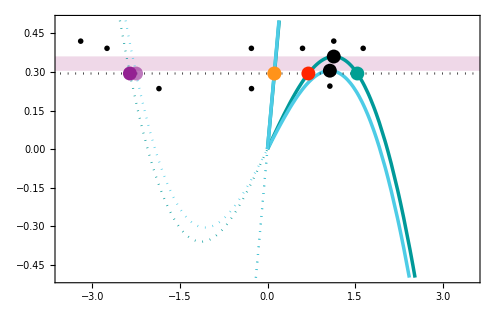

```mathematica
F2a=Show[Plot[{(Wpu[w,0]&&w>0),(Wpu[w,δn]&&w>0),(Wpv[w,0]&&w>0),(Wpv[w,δn]&&w>0),(Wpu[w,0]&&w<0),(Wpu[w,δn]&&w<0),(Wpv[w,0]&&w<0),(Wpv[w,δn]&&w<0),Wpu[ωIN,0],Wph[0],
Wph[δn]},{w,-20,20},Evaluate@plotStyle,Filling->{10->{11}},FillingStyle->{Opacity[0.3,color5]},PlotStyle->{{color1,Thickness[x]},{color3,Thickness[x]},{color1,Thickness[x]},{color3,Thickness[x]},{color1,Dotted},{color3,Dotted},{color1,Dotted},{color3,Dotted},{Black,Dotted},{Opacity[0.3,color5],Thickness[0.00001]},{Opacity[0.3,color5],Thickness[0.00001]}},FrameLabel->MaTeX[{"\\omega(\\text{PHz})","\\omega '(\\text{PHz})"},Magnification->1.5],FrameTicks->{{True,None},{True,None}},PlotRange-> {{-3.5,3.5},{-0.5,0.5}},ImageSize->500,Epilog->{Inset[MaTeX["\\omega_\\text{2u}",Magnification->m],{ω2u-4dy,Wpu[ω2u,0]+dy}],
Inset[MaTeX["\\omega_\\text{2ul}",Magnification->m],{ω2ur-0.1,Wpu[ωIN,0]+dy}],
Inset[MaTeX["\\omega_\\text{2ur}",Magnification->m],{ω2ul+0.1,Wpu[ωIN,0]+dy}],
Inset[MaTeX["\\omega_\\text{1u}",Magnification->m],{ω1u+4dy,Wpu[ω1u,δn]-0.6dy}],
Inset[MaTeX["\\omega_\\text{2v}",Magnification->m],{ω1v-4dy,Wpv[ω1v,δn]+dy}],Inset[MaTeX["\\text{(a)}",Magnification->m],{-3.2,0.42}],
Inset[MaTeX["\\omega_\\text{h}",Magnification->m],{whor[0],Wph[0]+0.06}],
Inset[MaTeX["\\omega_\\text{h-max}",Magnification->m],{whor[δn],Wph[δn]-0.06}],
Inset[MaTeX["\\omega_\\text{1v}",Magnification->m],{ω2v-4dy,Wpu[ωIN,0]-0.6dy}]}],

Graphics[{Black,PointSize[mm] ,Point[{whor[0],Wph[0]}]}],Graphics[{Black,PointSize[mm] ,Point[{whor[δn],Wph[δn]}]}],Graphics[{col11,PointSize[mm] ,Point[{ω1u,Wpu[ω1u,δn]}]}],
Graphics[{col14,PointSize[mm] ,Point[{ω1v,Wpv[ω1v,δn]}]}],Graphics[{col21,PointSize[mm] ,Point[{ω2u,Wpu[ω2u,0]}]}],
Graphics[{col22,PointSize[mm] ,Point[{ω2ul,Wpu[ωIN,0]}]}],
Graphics[{col23,PointSize[mm] ,Point[{ω2ur,Wpu[ω2ur,0]}]}],
Graphics[{col24,PointSize[mm] ,Point[{ω2v,Wpv[ω2v,0]}]}],GridLinesStyle->Directive[{Black,Dashed,Thickness[0.002]}]]
```

## Direction of travel.

dbp es la derivada de beta comóvil (pero con coordenadas (x,t)). o marco de laboratorio.

v_g=1/((∂β')/(∂ω))=1/∂_ω (β-u/c ω)→dbp
/////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////////
(∂ω_u')/(∂ω)→dwpu
(∂ω_v')/(∂ω)→dwpv
son las velocidades adimencionales en el marco comóvil (τ,ξ) contra y copropagante.

```mathematica
β0[w_,δ_]:=w/SOLL(√(1+w^2/Ω00^2)+δ);
Wpu0[w_,δ_]:=(w-uu β0[w,δ])ng00;
Wpv0[w_,δ_]:=(w+uu β0[w,δ])ng00;
```

```mathematica
vg[w_,δ_]:=ReplaceAll[1/D[β[ww,δ],ww],ww->w] (*Velocidad en marco de laboratorio*)
```

```mathematica
dbp[w_]=D[β[w,0],w]-u/SOL^2;
dwpu[w_,δ_]=-D[Wpu[w,δ],w] ;(*Velocidad de modos contrapropagantes en marco comovil*)
dwpv[w_,δ_]=-D[Wpv[w,δ],w];(*Velocidad de modos conpropagantes en marco comovil*)
vcomu[w_,δ_]=FullSimplify[D[Wpu0[w,δ],w]] (*Velocidad de modos contrapropagantes en marco comovil*)
vcomv[w_,δ_]=Simplify[D[Wpv0[w,δ],w]](*Velocidad de modos conpropagantes en marco comovil*)
```

ng00+(ng00 uu (-δ-(√(1+w^2/Ω00^2) (2 w^2+Ω00^2))/(w^2+Ω00^2)))/SOLL

ng00+(ng00 uu (δ+(√(1+w^2/Ω00^2) (2 w^2+Ω00^2))/(w^2+Ω00^2)))/SOLL

Velocidad adimencional del marco comovil
V_com=-dw/dw’=-ng00 (1(±uu (+δ+(√(1+w^2/Ω00^2) (2 w^2+Ω00^2))/(w^2+Ω00^2)))/SOLL)=-ng0±(dn+(√(1+w^2/Ω00^2) (2 w^2+Ω00^2))/(w^2+Ω00^2))

```mathematica
vlab=Simplify[1/D[β0[w,dnn],w]]
```

(SOLL √(1+w^2/Ω00^2) Ω00^2)/(2 w^2+(1+dnn √(1+w^2/Ω00^2)) Ω00^2)

```mathematica
invlab=Simplify[D[β0[w,dnn],w]]
```

(dnn+(√(1+w^2/Ω00^2) (2 w^2+Ω00^2))/(w^2+Ω00^2))/SOLL

Velocidad dimensional en marco de lab
V_lab=v_g=(SOL √(1+w^2/Ω00^2) Ω00^2)/(2 w^2+(1+dnn √(1+w^2/Ω00^2)) Ω00^2)=SOL/(dnn+(√(1+w^2/Ω00^2) (2 w^2+Ω00^2))/(w^2+Ω00^2))=c/(dnn+ √(1+w^2/Ω00^2)(2 w^2+Ω00^2)/(w^2+Ω00^2))

```mathematica
dwpu[ω1u,δn];
dwpu[ω2u,0];
dwpv[ω1v,δn];
dwpv[ω2v,0];
dwpu[ω2ul,0];
dwpu[ω2ur,0];
```

Esta es la misma gráfica que en el caso sónico. Sus velocidades asintóticas son +/- u.

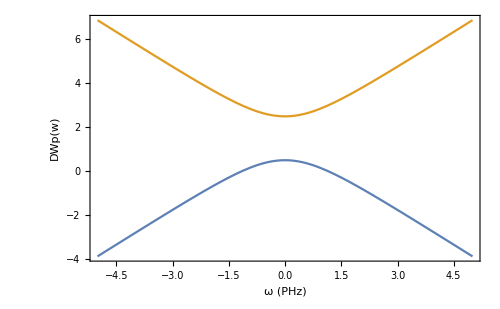

```mathematica
vp1=Plot[{-dwpu[w,0],-dwpv[w,0]},{w,-5,5},Frame->True,AspectRatio->1/GoldenRatio,ImageSize->500,FrameLabel->{"ω (PHz)","DWp(w)"},FrameTicksStyle->Directive[FontFamily->"Helvetica",20,Plain],
LabelStyle->Directive[FontFamily->"Helvetica",25]]
```

```mathematica
Limit[dwpu[w,0]/(ng0 dbp[w]),w->∞]
Limit[dwpv[w,0]/(ng0 dbp[w]),w->∞]
```

0.201406

-0.201406

Dejé la definición de ng pero no la uso.

```mathematica
wh=FindRoot[D[Wpu[w,0],w]==0,{w,1.5}][[1,2]];
whdn=FindRoot[D[Wpu[w,δn],w]==0,{w,1.5}][[1,2]];
```

```mathematica
Limit[vg[w,0],w->0]
Limit[vg[w,0],w->∞]
```

0.299792

0.

Esta gráfica es clave. La función vg está correcta. El límite de bajas frequencias w=0, da SOL. y w -> ∞ da 0. Correcto. En el lab, las velocidades solo son vg  y -vg para contra y coprop. Asintóticamente,  vg -> 0 para ambos. Esto es debido a la dispersión, la pendiente beta(w) tiende a ∞.

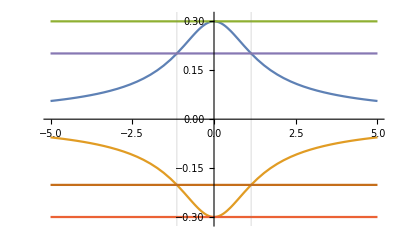

```mathematica
Plot[{vg[w,0],-vg[w,0],SOL,-SOL,u,-u},{w,-5,5},PlotRange->{-1.05,1.05} SOL,GridLines->{{-wh,wh},{}}]
```

En el comóvil, la vg’ (comóvil) es solo vg’(w)=vg(w)-u para contraprop y vg’(w)=-vg(w)-u para coprop. (Signo de u es por la dirección que elegimos.  a que contraprop cambia de signo (y dirección) entre (-wh,wh) y que coprop se mantiene negativa. Como vg -> 0 para altas frecuencias, aquí vg’ tiende a -u, la vel. del marco comóvil.(Falso. Se debe respetar la adición de velocidades de Einstein en este caso)

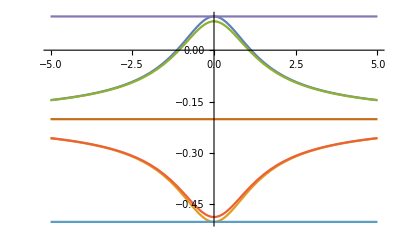

```mathematica
Plot[{vg[w,0]-u,-vg[w,0]-u,vg[w,δn]-u,-vg[w,δn]-u,SOL-u,-u,-SOL-u},{w,-5,5},PlotRange->All]
```

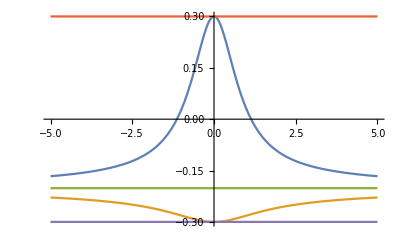

```mathematica
Plot[{(vg[w,0]-u)/(1-vg[w,0]u/SOL^2),(-vg[w,0]-u)/(1+vg[w,0]u/SOL^2),-u,SOL,-SOL},{w,-5,5},PlotRange->All]
```

Los cuatro modos se obtienen con dn y con 0.

```mathematica
v1u[w_]:=(vg[w,δn]-u)/(1-vg[w,0]u/SOL^2);
v2u[w_]:=(vg[w,0]-u)/(1-vg[w,0]u/SOL^2);
v1v[w_]:=(-vg[w,δn]-u)/(1+vg[w,0]u/SOL^2); 
v2v[w_]:=(-vg[w,0]-u)/(1+vg[w,0]u/SOL^2);
```

```mathematica
dv=0.2;m;
```

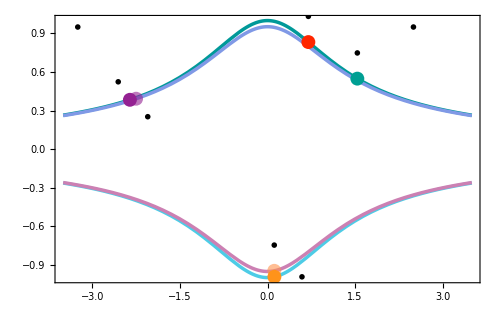

```mathematica
F3a=Show[Plot[{vg[w,0]/SOL,vg[w,δn]/SOL,-vg[w,0]/SOL,-vg[w,δn]/SOL},{w,-3.5,3.5},Evaluate@plotStyle,PlotStyle->{{color1,Thickness[x]},{color2,Thickness[x]},{color3,Thickness[x]},{color4,Thickness[x]}},FrameTicks->{{True,None},{None,None}},FrameLabel->MaTeX[{"","v_\\text{g}/c"},Magnification->m],ImageSize->500,PlotRange->All,Epilog->{Inset[MaTeX["\\omega_\\text{2ul}",Magnification->m],{ω2ur,vg[ω2ur,0]/SOL+dv}],
Inset[MaTeX["\\omega_\\text{2ur}",Magnification->m],{ω2ul,vg[ω2ul,0]/SOL+dv}],
Inset[MaTeX["\\omega_\\text{1u}",Magnification->m],{ω1u+0.2,vg[ω1u,δn]/SOL-0.7dv}],
Inset[MaTeX["\\omega_\\text{1v}",Magnification->m],{ω1v,-vg[ω1v,δn]/SOL+dv}],Inset[MaTeX["\\omega_\\text{2u}",Magnification->m],{ω2u-0.2,vg[ω2u,0]/SOL+0.7dv}],Inset[MaTeX["\\text{(a)}",Magnification->m],{-3.25,0.95}],
Inset[MaTeX["\\omega_\\text{2v}",Magnification->m],{5ω2v,-vg[ω2v,0]/SOL}],
Inset[MaTeX["\\text{Laboratory}",Magnification->m],{2.5,0.95}]}],Graphics[{col11,PointSize[0.02] ,Point[{ω1u,vg[ω1u,δn]/SOL}]}],
Graphics[{col21,PointSize[0.02] ,Point[{ω2u,vg[ω2u,0]/SOL}]}],
Graphics[{col14,PointSize[0.02] ,Point[{ω1v,-vg[ω1v,δn]/SOL}]}],
Graphics[{col24,PointSize[0.02] ,Point[{ω2v,-vg[ω2v,0]/SOL}]}],
Graphics[{col22,PointSize[0.02] ,Point[{ω2ul,vg[ω2ul,0]/SOL}]}],
Graphics[{col23,PointSize[0.02] ,Point[{ω2ur,vg[ω2ur,0]/SOL}]}],GridLines->{{},{}},GridLinesStyle->Directive[{Black,Dashed,Thickness[0.002]}]]
```

A diferencia del caso sónico, ahora las bajas frecuencias son las que cambian de dirección, esto es debido a que en el caso sónico la dispersión era anómala para obtener un BHL, su velocidad aumenta con la frecuencia. En este caso tenemos una dispersión normal, cuya velocidad disminuye con la frecuencia (como vimos hasta llegar a cero asintóticamente). Por tanto, la región de frecuencias que cambia de dirección se invierte, y es ahora, las bajas frecuencias. Pág. 69 tesis Gaona.

```mathematica
vl=Plot[{v1u[w]/SOL,v2u[w]/SOL,v1v[w]/SOL,v2v[w]/SOL},{w,-3.5,3.5},Evaluate@plotStyle,PlotStyle->{color2,color1,color4,color3},PlotRange->{{-3.5,3.5},{-1.3,1.1}},FrameLabel->MaTeX[{"\\omega(\\text{PHz})","v'/c"},Magnification->m],ImageSize->500,Epilog->{
Inset[MaTeX["\\omega_\\text{2ul}",Magnification->m],{ω2ur+0.1,v2u[ω2ur]/SOL+dv}],
Inset[MaTeX["\\omega_\\text{2ur}",Magnification->m],{ω2ul,v2u[ω2ul]/SOL-dv+0.1}],
Inset[MaTeX["\\omega_\\text{1u}",Magnification->m],{ω1u+0.1,v1u[ω1u]/SOL-dv+0.1}],
Inset[MaTeX["\\omega_\\text{1v}",Magnification->m],{ω1v+0.3,v1v[ω1v]/SOL+dv/2}],Inset[MaTeX["\\omega_\\text{2u}",Magnification->m],{ω2u-0.2,v2u[ω2u]/SOL+dv-0.05}],Inset[MaTeX["\\omega_\\text{h}",Magnification->m],{-wh-0.2,-1.1}],
Inset[MaTeX["\\omega_\\text{h}",Magnification->m],{wh+0.2,-1.1}],
Inset[MaTeX["\\text{(b)}",Magnification->m],{-3.1,.95}],
Inset[MaTeX["\\omega_\\text{2v}",Magnification->m],{ω2v+0.4,v2v[ω2v]/SOL-dv/2}]}];
```

```mathematica
vω1u=Graphics[{col11,PointSize[0.02] ,Point[{ω1u,v1u[ω1u]/SOL}]}];
vω2u=Graphics[{col21,PointSize[0.02] ,Point[{ω2u,v2u[ω2u]/SOL}]}];
vω1v=Graphics[{col14,PointSize[0.02] ,Point[{ω1v,v1v[ω1v]/SOL}]}];
vω2v=Graphics[{col24,PointSize[0.02] ,Point[{ω2v,v2v[ω2v]/SOL}]}];
vω2ul=Graphics[{col22,PointSize[0.02] ,Point[{ω2ul,v2u[ω2ul]/SOL}]}];
vω2ur=Graphics[{col23,PointSize[0.02] ,Point[{ω2ur,v2u[ω2ur]/SOL}]}];
```

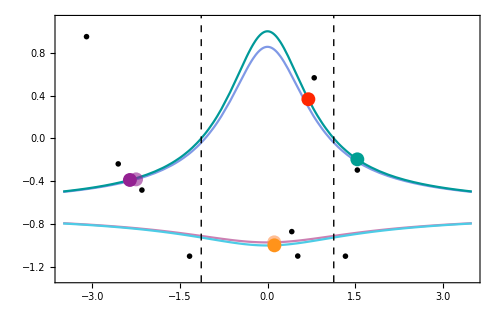

```mathematica
vCom=Show[vl,vω1u,vω2u,vω1v,vω2v,vω2ul,vω2ur,GridLines->{{-wh,wh},{}},GridLinesStyle->Directive[{Black,Dashed,Thickness[0.002]}]]
```

```mathematica
Export["Vel_comovil01.pdf",vCom]
```

Vel_comovil01.pdf

```mathematica
vωp1u=Graphics[{col11,PointSize[0.02] ,Point[{Wpu[ωIN,0],v1u[ω1u]/SOL}]}];
vωp2u=Graphics[{col21,PointSize[0.02] ,Point[{Wpu[ωIN,0],v2u[ω2u]/SOL}]}];
vωp2ul=Graphics[{col22,PointSize[0.02] ,Point[{Wpu[ωIN,0],v2u[ω2ul]/SOL}]}];
vωp2ur=Graphics[{col23,PointSize[0.02] ,Point[{Wpu[ωIN,0],v2u[ω2ur]/SOL}]}];
vωp1v=Graphics[{col14,PointSize[0.02] ,Point[{Wpu[ωIN,0],v1v[ω1v]/SOL}]}];
vωp2v=Graphics[{col24,PointSize[0.02] ,Point[{Wpu[ωIN,0],v2v[ω2v]/SOL}]}];
```

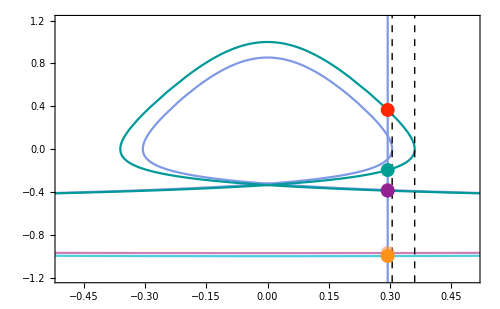

```mathematica
vpwp=ParametricPlot[{{Wpu[w,δn],v1u[w]/SOL},{Wpu[w,0],v2u[w]/SOL},{Wpv[w,δn],v1v[w]/SOL},{Wpv[w,0],v2v[w]/SOL},{Wpu[ωIN,0],w}},{w,-3,3},PlotRange-> {{-0.5,0.5},{-1.2,1.2}},Frame->True,AspectRatio->1/GoldenRatio,ImageSize->500,FrameLabel->MaTeX[{"\\omega'(\\text{PHz})","v'/c"},Magnification->m],Evaluate@plotStyle,PlotStyle->{color2,color1,color4,color3},FrameTicksStyle->Directive[FontFamily->"Helvetica",20,Plain],
LabelStyle->Directive[FontFamily->"Helvetica",25],GridLines->{{Wph[0],Wph[δn]},{}},GridLinesStyle->Directive[{Black,Dashed,Thickness[0.002]}]];
Show[vpwp,vωp1u,vωp2u,vωp2ul,vωp2ur,vωp1v,vωp2v]
```

```mathematica
F3b=Show[Plot[{dwpu[w,0],dwpu[w,δn],dwpv[w,0],dwpv[w,δn]},{w,-3.5,3.5},Evaluate@plotStyle,PlotStyle->{{color1,Thickness[x]},{color2,Thickness[x]},{color3,Thickness[x]},{color4,Thickness[x]}},FrameLabel->MaTeX[{"\\omega(\\text{PHz})","\\upsilon'"},Magnification->m],ImageSize->500,PlotRange->{{-3.5,3.5},{-ng0-5,-ng0+5}},FrameTicks->{{True,None},{True,None}},Epilog->{Inset[MaTeX["\\omega_\\text{2ul}",Magnification->m],{ω2ur,dwpu[ω2ur,0]+3.5dv}],
Inset[MaTeX["\\omega_\\text{2ur}",Magnification->m],{ω2ul,dwpu[ω2ul,0]-3dv}],
Inset[MaTeX["\\omega_\\text{1u}",Magnification->m],{ω1u+0.2,dwpu[ω1u,δn]-3dv}],
Inset[MaTeX["\\omega_\\text{1v}",Magnification->m],{ω1v+0.2,dwpv[ω1v,δn]-2dv}],Inset[MaTeX["\\omega_\\text{2u}",Magnification->m],{ω2u-0.2,dwpu[ω2u,0]+4dv}],Inset[MaTeX["\\text{(b)}",Magnification->m],{-3.18,3.0}],
Inset[MaTeX["\\omega_\\text{2v}",Magnification->m],{ω2v+0.1,dwpv[ω2v,0]+2.5dv}],
Inset[MaTeX["\\omega_\\text{h}",Magnification->m],{-wh-0.2,-6}],
Inset[MaTeX["\\omega_\\text{h}",Magnification->m],{wh+0.2,-6}],
Inset[MaTeX["\\text{Comoving}",Magnification->m],{2.5,3.0}]}],Graphics[{col11,PointSize[0.02] ,Point[{ω1u,dwpu[ω1u,δn]}]}],
Graphics[{col21,PointSize[0.02] ,Point[{ω2u,dwpu[ω2u,0]}]}],
Graphics[{col14,PointSize[0.02] ,Point[{ω1v,dwpv[ω1v,δn]}]}],
Graphics[{col24,PointSize[0.02] ,Point[{ω2v,dwpv[ω2v,0]}]}],
Graphics[{col22,PointSize[0.02] ,Point[{ω2ul,dwpu[ω2ul,0]}]}],
Graphics[{col23,PointSize[0.02] ,Point[{ω2ur,dwpu[ω2ur,0]}]}],GridLines->{{-wh,wh},{}},GridLinesStyle->Directive[{Black,Dashed,Thickness[0.002]}]];
```

ORGANIZAR IMAGEN

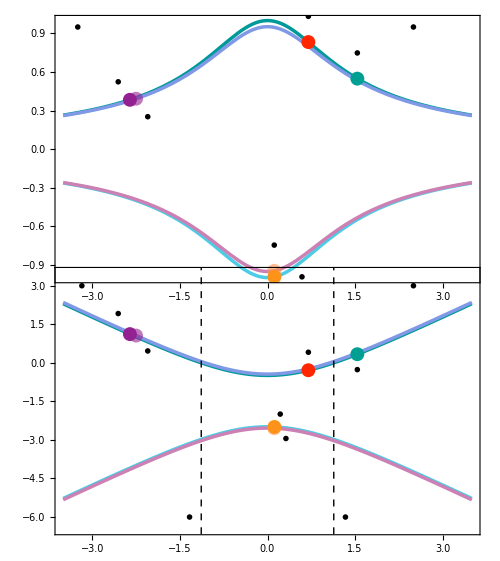

```mathematica
GraphicsGrid[{{F3a},{F3b}},Spacings->{-20,-57},ImageSize->500] (*Organizar*)
```

## Analytical solution

```mathematica
Simplify[w^2(1+w^2/Ω0n^2) -(w00+v *w)^2]
```

w^2-(v w+w00)^2+w^4/Ω0n^2

### Reducing to 3rd Order.

```mathematica
ce=(1-v^2)*Ω0n^2;
cf=-2*w00*v*Ω0n^2;
cg=-w00^2*Ω0n^2;
sol3=Solve[z^3+ce/2 z^2+(ce^2-4cg)/16 z-cf^2/64==0,z];
cp=√sol3[[1,1,2]]//Simplify;
cq=√sol3[[2,1,2]]//Simplify;
cr=√sol3[[3,1,2]]//Simplify;
sol4a=cp+cq+cr;
sol4b=cp-cq-cr;
sol4c=-cp+cq-cr;
sol4d=-cp-cq+cr;
sol4={sol4b,sol4a,sol4c,sol4d};
sol=-sol4;
```

Modos posibles por solución analítica. Para la región superluminica contrapropagantes (ω2ua,ω2ura,ω2ula), y copropagantes (ω2va). Para la región subluminica contrapropagantes (ω1ua,ω1ura,ω1ula), los dos ultimos son nuevas soluciones complejas, las cuales aparecen despues de pasar una vel transluminica.  Y existe solo un modo copropagante (ω1va)

```mathematica
ω2va=N@sol[[1]]/.{Ω0n->Ω0,v->ng0,w00->Wpu[ωIN,0]};
ω2ua=N@sol[[2]]/.{Ω0n->Ω0,v->ng0,w00->Wpu[ωIN,0]};
ω2ula=N@sol[[3]]/.{Ω0n->Ω0,v->ng0,w00->Wpu[ωIN,0]};
ω2ura=N@sol[[4]]/.{Ω0n->Ω0,v->ng0,w00->Wpu[ωIN,0]};

ω1va=N@sol[[1]]/.{Ω0n->Ω0,v->ng0+δn,w00->Wpu[ωIN,0]}; 
ω1ua=N@sol[[2]]/.{Ω0n->Ω0,v->ng0-δn,w00->Wpu[ωIN,0]};
ω1ula=N@sol[[3]]/.{Ω0n->Ω0,v->ng0-δn,w00->Wpu[ωIN,0]}; (*New*)
ω1ura=N@sol[[4]]/.{Ω0n->Ω0,v->ng0-δn,w00->Wpu[ωIN,0]}; (*New*)
```

```mathematica
solnump={ω2u,ω1u,ω1v,ω2v,ω2ul,ω2ur}
solana={ω2ua,ω1ua,ω1va,ω2va,ω2ula,ω2ura,ω1ula,ω1ura}//Chop
```

{-2.35697,-2.2513,0.115771,0.118091,1.53888,0.7}

{-2.35697,-2.2513,0.115771,0.118091,1.53888,0.7,1.23832,0.892482}

```mathematica
vmin=vtt-2δn;vmax=vtt+2δn;
n=0;
```

```mathematica
vtt
```

vtt

```mathematica
vmin
```

-0.1+vtt

```mathematica
pua=Plot[{Re/@sol[[2]]/.{Ω0n->Ω0,w00->Wpu[ωIN,0]},Im/@sol[[2]]/.{Ω0n->Ω0,w00->Wpu[ωIN,0]}},{v,vmin,vmax},Evaluate@plotStyle,PlotStyle->{color1,{color3,Dashed}},FrameLabel->MaTeX[{"","\\omega_\\text{u}"},Magnification->1.5],PlotRange->{{vmin,vmax},{-2.9,0.1}}, FrameTicks->{{True,None},{None,None}},Epilog->{
Inset[MaTeX["\\upsilon_t",Magnification->m],{vtt+0.02,-1.3}]}];
p1u=Graphics[{col11,PointSize[n] ,Point[{ng0-δn,ω1u}]}];
p2u=Graphics[{col21,PointSize[n] ,Point[{ng0,ω2u}]}];
a1=Show[pua,p1u,p2u,GridLines->{{vtt},{}},GridLinesStyle->Directive[{Black,Dotted,Thickness[0.002]}],AspectRatio->1];
```

Plot::plln: Limiting value -0.1+vtt in {v,-0.1+vtt,0.1+vtt} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Plot[{Re/@sol⟦2⟧/.{Ω0n→Ω0,w00→Wpu[ωIN,0]},Im/@sol⟦2⟧/.{Ω0n→Ω0,w00→Wpu[ωIN,0]}},{v,vmin,vmax},«4»,FrameTicks→{{True,None},{None,None}},Epilog→{Inset[MaTeX[\upsilon_t,Magnification→m],{vtt+0.02,-1.3}]}],,,«9»→«1»,GridLinesStyle→Directive[{GrayLevel[0],«1»,Thickness[0.002]}],AspectRatio→1].

Plot::plln: Limiting value -0.1+vtt in {v,-0.1+vtt,0.1+vtt} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Plot[{Re/@sol⟦2⟧/.{Ω0n→Ω0,w00→Wpu[ωIN,0]},Im/@sol⟦2⟧/.{Ω0n→Ω0,w00→Wpu[ωIN,0]}},{v,vmin,vmax},«4»,FrameTicks→{{True,None},{None,None}},Epilog→{Inset[MaTeX[\upsilon_t,Magnification→m],{vtt+0.02,-1.3}]}],,,«9»→«1»,GridLinesStyle→Directive[{GrayLevel[0],«1»,Thickness[0.002]}],AspectRatio→1].

```mathematica
pva=Plot[{Re/@sol[[1]]/.{Ω0n->Ω0,w00->Wpu[ωIN,0]},Im/@sol[[1]]/.{Ω0n->Ω0,w00->Wpu[ωIN,0]}},{v,vmin,vmax},Evaluate@plotStyle,PlotStyle->{color1,{color3,Dashed}},FrameLabel->MaTeX[{"\\upsilon(\\tau)","\\omega_\\text{v}"},Magnification->m],PlotRange->{{vmin,vmax},{-0.01,0.2}}, FrameTicks->{{True,None},{{-1.62,-1.53,-1.44,-1.35,-1.26},None}},ImageSize->500,Epilog->{
Inset[MaTeX["\\upsilon_t",Magnification->m],{vtt+0.02,0.09}]}];
p1v=Graphics[{col14,PointSize[n] ,Point[{ng0+δn,ω1v}]}];
p2v=Graphics[{col24,PointSize[n] ,Point[{ng0,ω2v}]}];
a2=Show[pva,p1v,p2v,GridLines->{{vtt},{}},GridLinesStyle->Directive[{Black,Dotted,Thickness[0.002]}],AspectRatio->1];
```

Plot::plln: Limiting value -0.1+vtt in {v,-0.1+vtt,0.1+vtt} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Plot[{Re/@sol⟦1⟧/.{Ω0n→Ω0,w00→Wpu[ωIN,0]},Im/@sol⟦1⟧/.{Ω0n→Ω0,w00→Wpu[ωIN,0]}},{v,vmin,vmax},«5»,ImageSize→500,Epilog→{Inset[MaTeX[\upsilon_t,Magnification→m],{vtt+0.02,0.09}]}],,,GridLines→«1»,GridLinesStyle→Directive[{GrayLevel[0],Dashing[{0,Small}],Thickness[0.002]}],AspectRatio→1].

Plot::plln: Limiting value -0.1+vtt in {v,-0.1+vtt,0.1+vtt} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Plot[{Re/@sol⟦1⟧/.{Ω0n→Ω0,w00→Wpu[ωIN,0]},Im/@sol⟦1⟧/.{Ω0n→Ω0,w00→Wpu[ωIN,0]}},{v,vmin,vmax},«5»,ImageSize→500,Epilog→{Inset[MaTeX[\upsilon_t,Magnification→m],{vtt+0.02,0.09}]}],,,GridLines→«1»,GridLinesStyle→Directive[{GrayLevel[0],Dashing[{0,Small}],Thickness[0.002]}],AspectRatio→1].

```mathematica
pula=Plot[{Re/@sol[[3]]/.{Ω0n->Ω0,w00->Wpu[ωIN,0]},Im/@sol[[3]]/.{Ω0n->Ω0,w00->Wpu[ωIN,0]}},{v,vmin,vmax},Evaluate@plotStyle,PlotStyle->{color1,{color3,Dashed}},FrameLabel->MaTeX[{"","\\omega_\\text{ur}"},Magnification->m],ImageSize->500,PlotRange->{{vmin,vmax},{-1.8,2.1}},FrameTicks->{{True,None},{None,None}},Epilog->{
Inset[MaTeX["\\upsilon_t",Magnification->m],{vtt+0.02,0.3}]}];
p2ul=Graphics[{col22,PointSize[n] ,Point[{ng0,ω2ul}]}];
p1ulr=Graphics[{col12,PointSize[n] ,Point[{ng0-δn,Re[ω1ula]}]}];
p1uli=Graphics[{col12,PointSize[n] ,Point[{ng0-δn,Im[ω1ula]}]}];
a3=Show[pula,p2ul,p1ulr,p1uli,GridLines->{{vtt},{}},GridLinesStyle->Directive[{Black,Dotted,Thickness[0.002]}],AspectRatio->1];
```

Plot::plln: Limiting value -0.1+vtt in {v,-0.1+vtt,0.1+vtt} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Plot[{Re/@sol⟦3⟧/.{Ω0n→Ω0,w00→Wpu[ωIN,0]},Im/@sol⟦3⟧/.{Ω0n→Ω0,w00→Wpu[ωIN,0]}},{v,vmin,vmax},«5»,FrameTicks→{{True,None},{None,None}},Epilog→{Inset[MaTeX[\upsilon_t,Magnification→m],{vtt+0.02,0.3}]}],,«3»,GridLinesStyle→Directive[{GrayLevel[0],Dashing[«1»],Thickness[0.002]}],AspectRatio→1].

Plot::plln: Limiting value -0.1+vtt in {v,-0.1+vtt,0.1+vtt} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Plot[{Re/@sol⟦3⟧/.{Ω0n→Ω0,w00→Wpu[ωIN,0]},Im/@sol⟦3⟧/.{Ω0n→Ω0,w00→Wpu[ωIN,0]}},{v,vmin,vmax},«5»,FrameTicks→{{True,None},{None,None}},Epilog→{Inset[MaTeX[\upsilon_t,Magnification→m],{vtt+0.02,0.3}]}],,«3»,GridLinesStyle→Directive[{GrayLevel[0],Dashing[«1»],Thickness[0.002]}],AspectRatio→1].

```mathematica
pura=Plot[{Re/@sol[[4]]/.{Ω0n->Ω0,w00->Wpu[ωIN,0]},Im/@sol[[4]]/.{Ω0n->Ω0,w00->Wpu[ωIN,0]}},{v,-2ng0,2ng0},Evaluate@plotStyle,PlotStyle->{color1,{color3,Dashed}},FrameLabel->MaTeX[{"\\upsilon(\\tau)","\\omega_\\text{ul}"},Magnification->m],FrameTicks->{{True,None},{{-1.62,-1.53,-1.44,-1.35,-1.26},None}},PlotRange->{{vmin,vmax},{-0.1,1.6}}, Epilog->{
Inset[MaTeX["\\upsilon_{t}",Magnification->m],{vtt+0.02,0.7}]}];
p2ur=Graphics[{col23,PointSize[n] ,Point[{ng0,ω2ur}]}];
p1urr=Graphics[{col13,PointSize[n] ,Point[{ng0-δn,Re[ω1ura]}]}];
p1uri=Graphics[{col13,PointSize[n] ,Point[{ng0-δn,Im[ω1ura]}]}];
a4=Show[pura,p2ur,p1urr,p1uri,GridLines->{{vtt},{}},GridLinesStyle->Directive[{Black,Dotted,Thickness[0.002]}],AspectRatio->1,ImageSize->500];
```

General::prng: Value of option PlotRange -> {{-0.1+vtt,0.1+vtt},{-0.1,1.6}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
pgrid=GraphicsGrid[{{a1,a3},{a4,a2}},Spacings->{5,-112},ImageSize->600]
```

Plot::plln: Limiting value -0.1+vtt in {v,-0.1+vtt,0.1+vtt} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Plot[{Re/@sol⟦2⟧/.{Ω0n→Ω0,w00→Wpu[ωIN,0]},Im/@sol⟦2⟧/.{Ω0n→Ω0,w00→Wpu[ωIN,0]}},{v,vmin,vmax},«4»,FrameTicks→{{True,None},{None,None}},Epilog→{Inset[MaTeX[\upsilon_t,Magnification→m],{vtt+0.02,-1.3}]}],,,«9»→«1»,GridLinesStyle→Directive[{GrayLevel[0],«1»,Thickness[0.002]}],AspectRatio→1].

Plot::plln: Limiting value -0.1+vtt in {v,-0.1+vtt,0.1+vtt} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Plot[{Re/@sol⟦3⟧/.{Ω0n→Ω0,w00→Wpu[ωIN,0]},Im/@sol⟦3⟧/.{Ω0n→Ω0,w00→Wpu[ωIN,0]}},{v,vmin,vmax},«5»,FrameTicks→{{True,None},{None,None}},Epilog→{Inset[MaTeX[\upsilon_t,Magnification→m],{vtt+0.02,0.3}]}],,«3»,GridLinesStyle→Directive[{GrayLevel[0],Dashing[«1»],Thickness[0.002]}],AspectRatio→1].

Plot::plln: Limiting value -0.1+vtt in {v,-0.1+vtt,0.1+vtt} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[Plot[{Re/@sol⟦1⟧/.{Ω0n→Ω0,w00→Wpu[ωIN,0]},Im/@sol⟦1⟧/.{Ω0n→Ω0,w00→Wpu[ωIN,0]}},{v,vmin,vmax},«5»,ImageSize→500,Epilog→{Inset[MaTeX[\upsilon_t,Magnification→m],{vtt+0.02,0.09}]}],,,GridLines→«1»,GridLinesStyle→Directive[{GrayLevel[0],Dashing[{0,Small}],Thickness[0.002]}],AspectRatio→1].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

-Graphics-

Soluciones analíticas para v1 =ng0-δn y v2 = ng0  en el plano complejo de ω.

Imagen anterior de otra forma

```mathematica
h=0.006;
```

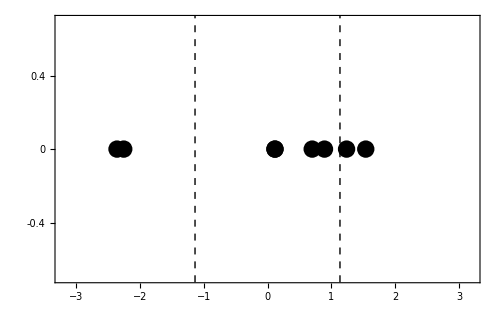

```mathematica
dt=0.1;dx=0.1;
pa0=Plot[{},{w,-3.5,3.5},PlotRange->{{-3.2,3.2},{-0.7,0.7}}, Evaluate@plotStyle,FrameLabel->MaTeX[{"\\text{Re}(\\omega)","\\text{Im}(\\omega)"},Magnification->1.8],ImageSize->500,Epilog->{
Inset[MaTeX["\\omega_\\text{2u}",Magnification->m],{Re[solana[[1]]],Im[solana[[1]]]+dt}],
Inset[MaTeX["\\omega_\\text{1u}",Magnification->m],{Re[solana[[2]]],Im[solana[[2]]]-dt}],
Inset[MaTeX["\\omega_\\text{1v}",Magnification->m],{Re[solana[[3]]]+1.5dx,Im[solana[[3]]]-dt}],
Inset[MaTeX["\\omega_\\text{2v}",Magnification->m],{Re[solana[[4]]]+1.5dx,Im[solana[[4]]]+dt}],
Inset[MaTeX["\\omega_\\text{2ul}",Magnification->m],{Re[solana[[5]]],Im[solana[[5]]]+dt}],
Inset[MaTeX["\\omega_\\text{2ur}",Magnification->m],{Re[solana[[6]]]+dx,Im[solana[[6]]]+dt}],
Inset[MaTeX["\\omega_\\text{1ul}",Magnification->m],{Re[solana[[7]]]-2dt,Im[solana[[7]]]-dt}],
Inset[MaTeX["\\omega_\\text{1ur}",Magnification->m],{Re[solana[[8]]]-2dt,Im[solana[[8]]]-dt}],
Inset[MaTeX["-\\omega_\\text{h}",Magnification->m],{-whor[0]-3dx,-0.6}],
Inset[MaTeX["\\omega_\\text{h}",Magnification->m],{whor[0]+3dx,-0.6}]}];

pω2u=Graphics[{Black,PointSize[0.025] ,Point[{Re[solana[[1]]],Im[solana[[1]]]}]}];
pω1u=Graphics[{Black,PointSize[0.025] ,Point[{Re[solana[[2]]],Im[solana[[2]]]}]}];
pω1v=Graphics[{Black,PointSize[0.025] ,Point[{Re[solana[[3]]],Im[solana[[3]]]}]}];
pω2v=Graphics[{Black,PointSize[0.025] ,Point[{Re[solana[[4]]],Im[solana[[4]]]}]}];
pω2ul=Graphics[{Black,PointSize[0.025] ,Point[{Re[solana[[5]]],Im[solana[[5]]]}]}];
pω2ur=Graphics[{Black,PointSize[0.025] ,Point[{Re[solana[[6]]],Im[solana[[6]]]}]}];
pω1ul=Graphics[{Black,PointSize[0.025] ,Point[{Re[solana[[7]]],Im[solana[[7]]]}]}];
pω1ur=Graphics[{Black,PointSize[0.025] ,Point[{Re[solana[[8]]],Im[solana[[8]]]}]}];


porig=Show[Plot[{},{w,-3.5,3.5},PlotRange->{{-3.2,3.2},{-0.7,0.7}}, Axes->True,Evaluate@plotStyle,FrameLabel->MaTeX[{"","\\text{Im}(\\omega)"},Magnification->1.8],Frame->{{True,True},{True,True}},Evaluate@plotStyle,GridLinesStyle->Directive[{Black,Dashed,Thickness[0.002]}],FrameTicks->{{{-0.8,-0.6,-0.4,-0.2,0,0.2,0.4,0.6},None},{None,None}},ImageSize->500],pω2u,pω1u,pω1v,pω2v,pω2ul,pω2ur,pω1ul,pω1ur,GridLines->{{-whor[0],whor[0]},{}},GridLinesStyle->Directive[{Black,Dashed,Thickness[0.002]}],ImageSize->500]
```

## Transluminical Velocity

Dados, Ω0 (escala de la dispersión) , ωIN (frecuencia de entrada ω_(2ur)) y ng0. Que velocidad se requiere para que ω_(2ul)=ω_(2ur)?.  Que representa este valor?. Como hacerlo?.
Dicha velocidad se denominara transluminica (vt), y determina el mínimo valor de velocidad para alcanzar el horizonte, se logra cuando ω_(2r)=ω_(2l), para velocidades mayores a vt, los modos ω_(2l), ω_(2r) se hacen complejos. Se realiza igualando las soluciones analiticas pertenecientes a dichos modos, i.e  sol[[3]]==sol[[4]].

```mathematica
vels=NSolve[sol[[4]]==sol[[3]]/.{Ω0n->Ω0,w00->Wpu[ωIN,0]},v]
```

NSolve::illcnd: Possible ill-conditioning detected in system. Likely cause is exact or approximate multiplicity. This may cause solutions to suffer from loss of precision. Use of sufficiently large WorkingPrecision may resolve this.

{{v→1.42817},{v→-1.42817}}

```mathematica
vtt=-1.42817;

fj=vels[[1,1]];
```

```mathematica
fj
```

v→1.42817

```mathematica
solvel=Solve[sol[[3]]==sol[[4]],v]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v→-√(1-w00^2/(3 Ω0n^2)+(2^(1/3) w00^4)/(3 (-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3))+(18 2^(1/3) w00^2 Ω0n^2)/(-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3)+1/(3 2^(1/3) Ω0n^4)(-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3))},{v→√(1-w00^2/(3 Ω0n^2)+(2^(1/3) w00^4)/(3 (-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3))+(18 2^(1/3) w00^2 Ω0n^2)/(-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3)+1/(3 2^(1/3) Ω0n^4)(-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3))},{v→-√(1-w00^2/(3 Ω0n^2)-w00^4/(3 2^(2/3) (-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3))+(ⅈ w00^4)/(2^(2/3) √3 (-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3))-(9 2^(1/3) w00^2 Ω0n^2)/(-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3)+(9 ⅈ 2^(1/3) √3 w00^2 Ω0n^2)/(-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3)-1/(6 2^(1/3) Ω0n^4)(-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3)-1/(2 2^(1/3) √3 Ω0n^4)ⅈ (-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3))},{v→√(1-w00^2/(3 Ω0n^2)-w00^4/(3 2^(2/3) (-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3))+(ⅈ w00^4)/(2^(2/3) √3 (-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3))-(9 2^(1/3) w00^2 Ω0n^2)/(-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3)+(9 ⅈ 2^(1/3) √3 w00^2 Ω0n^2)/(-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3)-1/(6 2^(1/3) Ω0n^4)(-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3)-1/(2 2^(1/3) √3 Ω0n^4)ⅈ (-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3))},{v→-√(1-w00^2/(3 Ω0n^2)-w00^4/(3 2^(2/3) (-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3))-(ⅈ w00^4)/(2^(2/3) √3 (-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3))-(9 2^(1/3) w00^2 Ω0n^2)/(-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3)-(9 ⅈ 2^(1/3) √3 w00^2 Ω0n^2)/(-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3)-1/(6 2^(1/3) Ω0n^4)(-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3)+1/(2 2^(1/3) √3 Ω0n^4)ⅈ (-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3))},{v→√(1-w00^2/(3 Ω0n^2)-w00^4/(3 2^(2/3) (-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3))-(ⅈ w00^4)/(2^(2/3) √3 (-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3))-(9 2^(1/3) w00^2 Ω0n^2)/(-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3)-(9 ⅈ 2^(1/3) √3 w00^2 Ω0n^2)/(-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3)-1/(6 2^(1/3) Ω0n^4)(-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3)+1/(2 2^(1/3) √3 Ω0n^4)ⅈ (-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3))}}

```mathematica
solvel[[1,1,2]]
```

-√(1-w00^2/(3 Ω0n^2)+(2^(1/3) w00^4)/(3 (-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3))+(18 2^(1/3) w00^2 Ω0n^2)/(-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3)+1/(3 2^(1/3) Ω0n^4)(-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20))^(1/3))

```mathematica
q3=-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20);
```

```mathematica
s= √(-64 w00^10 Ω0n^14+1296 w00^8 Ω0n^16-8748 w00^6 Ω0n^18+19683 w00^4 Ω0n^20);
FullSimplify[s]
```

√(-w00^4 Ω0n^14 (4 w00^2-27 Ω0n^2)^3)

```mathematica
FullSimplify[q3]
```

-2 w00^6 Ω0n^6+270 w00^4 Ω0n^8+729 w00^2 Ω0n^10+3 √3 √(-w00^4 Ω0n^14 (4 w00^2-27 Ω0n^2)^3)

```mathematica
Wpu[0,0]
```

0.

```mathematica
Ω0
```

1.8618

```mathematica
qq[w_]:=-2+270 Ω0^2/(Wpu[w,0])^2+729 Ω0^4/(Wpu[w,0])^4+(3^(3/2)Ω0)/(Wpu[w,0])√((27 Ω0^2/(Wpu[w,0])^2-4)^3);
```

```mathematica
qq[1]
```

1.12636×10^6

```mathematica
vt=√(1+w00^2/(3Ω0n^2)(q^(1/3)/2^(1/3)-1)+2^(1/3)/(3 q^(1/3))(w00^2/Ω0n^2+54))/.{Ω0n->Ω0,w00->Wpu[ωIN,0]}
ng0+vtt
```

√(1+0.0083181 (-1+q^(1/3)/2^(1/3))+22.6891/q^(1/3))

0.0603279

```mathematica
ng0
```

1.4885

```mathematica
δn
```

0.05

```mathematica
-ng0+δn
```

-1.4385

```mathematica
vtt
```

-1.42817

```mathematica
ng0
```

1.4885

```mathematica
-1.428+ng0
```

0.0604979

```mathematica
-ng0
```

-1.4885

```mathematica
vtt
```

-1.42817

```mathematica
vt;
vtt;
```

```mathematica
dnt=vt+ng0
```

1.4885+√(1+0.0083181 (-1+q^(1/3)/2^(1/3))+22.6891/q^(1/3))

-1.4825

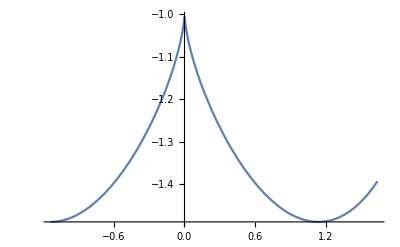

```mathematica
vttq[w_]:=-√(1+(Wpu[w,0])^2/(3Ω0^2)(qq[w]^(1/3)/2^(1/3)-1)+2^(1/3)/(3 qq[w]^(1/3))((Wpu[w,0])^2/Ω0^2+54))
vttq[1]
Plot[vttq[w],{w,-wh,wh+0.5},PlotRange->Automatic]
```

```mathematica
dnmin=-ng0+√(1+w00^2/(3Ω0n^2)(q^(1/3)/2^(1/3)-1)+2^(1/3)/(3 q^(1/3))(w00^2/Ω0n^2+54))/.{Ω0n->Ω0,w00->Wpu[ωIN,0]}
```

-1.4885+√(1+0.0083181 (-1+q^(1/3)/2^(1/3))+22.6891/q^(1/3))

Tenemos como formula analitica para la velocidad transluminica: vt=-√(1+((w̃)_0)^2/(3Ω0^2)(q^(1/3)/2^(1/3)-1)+2^(1/3)/(3 q^(1/3))(((w̃)_0)^2/Ω0^2+54)), con q=270 Ω0^2/((w̃)_0)^2+729 Ω0^4/((w̃)_0)^4+(3^(3/2)Ω0)/((w̃)_0)√((27 Ω0^2/((w̃)_0)^2-4)^3)-2.
La velocidad transluminica puede ser interpretada en el caso óptico como el minimo cambio en el índice de refracción tal que  ω_(2ul)=ω_(2ur), es decir δn_t=ng0+vt, tal que δn_t<δn_max.

## Sorting Analytic Solutions

```mathematica
Clear[solSort2,w21,w22,w23,w24]

solSort2[wpRe_/;wpRe<Wph[0],wpIm_]:=Module[{solT,ordT},
solT=sol/.{Ω0n->Ω0,v->ng0,w00->(wpRe+I wpIm)};
ordT=SortBy[solT,Re[#]&];
{ordT[[1]],ordT[[4]],ordT[[3]],ordT[[2]]}
]
solSort2[wpRe_/;Wph[0] <wpRe,wpIm_]:=Module[{solT,ordT,ordT2},
solT=sol/.{Ω0n->Ω0,v->ng0,w00->(wpRe+I wpIm)};
ordT=SortBy[solT,Re[#]&];
ordT2=SortBy[{ordT[[3]],ordT[[4]]},Im[#]&];
{ordT[[1]],ordT2[[1]],ordT2[[2]],ordT[[2]]}
]
w21[wpRe_,wpIm_]:=N@solSort2[wpRe,wpIm][[1]];
w22[wpRe_,wpIm_]:=N@solSort2[wpRe,wpIm][[2]];
w23[wpRe_,wpIm_]:=N@solSort2[wpRe,wpIm][[3]];
w24[wpRe_,wpIm_]:=N@solSort2[wpRe,wpIm][[4]];
```

```mathematica
{w21[Wpu[ωIN,0] ,0.],w22[Wpu[ωIN,0],0.],w23[Wpu[ωIN,0],0.],w24[Wpu[ωIN,0] ,0.]}//Chop
```

{-2.35697,1.53888,0.7,0.118091}

```mathematica
{ω2ua,ω2ula,ω2ura,ω2va}//Chop
```

{-2.35697,1.53888,0.7,0.118091}

```mathematica
Clear[solSort1,w11,w12,w13,w14];
solSort1[wpRe_/;0<=wpRe<Wph[δn],wpIm_]:=Module[{solT,ordT,solvT,ordvT},
solT=sol/.{Ω0n->Ω0,v->-ng0+δn,w00->(wpRe+I wpIm)};
solvT=sol/.{Ω0n->Ω0,v->-ng0-δn,w00->(wpRe+I wpIm)};
ordT=SortBy[solT,Re[#]&];
ordvT=SortBy[solvT,Re[#]&];
{ordT[[1]],ordT[[4]],ordT[[3]],ordvT[[2]]}
]
solSort1[wpRe_/;Wph[δn] <wpRe,wpIm_]:=Module[{solT,ordT,ordT2,solvT,ordvT,ordvT2},
solT=sol/.{Ω0n->Ω0,v->-ng0+δn,w00->(wpRe+I wpIm)};
solvT=sol/.{Ω0n->Ω0,v->-ng0+δn,w00->(wpRe+I wpIm)};
ordT=SortBy[solT,Re[#]&];
ordvT=SortBy[solvT,Re[#]&];
ordT2=SortBy[{ordT[[3]],ordT[[4]]},Im[#]&];
{ordT[[1]],ordT2[[1]],ordT2[[2]],ordvT[[2]]}
]
w11[wpRe_,wpIm_]:=N@solSort1[wpRe,wpIm][[1]];
w12[wpRe_,wpIm_]:=N@solSort1[wpRe,wpIm][[2]];
w13[wpRe_,wpIm_]:=N@solSort1[wpRe,wpIm][[3]];
w14[wpRe_,wpIm_]:=N@solSort1[wpRe,wpIm][[4]];
```

```mathematica
{w11[Wpu[ωIN,0],0.0],w12[Wpu[ωIN,0],.0],w13[Wpu[ωIN,0],.0],w14[Wpu[ωIN,0],.0]} //Chop

{ω1ua ,ω1ula,ω1ura,ω1va}//Chop
```

{-2.2513,1.23832,0.892482,0.115771}

{-2.2513,1.23832,0.892482,0.115771}

```mathematica
Clear[w0test,imww,dy, imw]
```

```mathematica
w0test=Wpu[ωIN,0];imww=0.1;dy=0.2;dx=0.15;imw=0; l=4; mag=1.8;
```

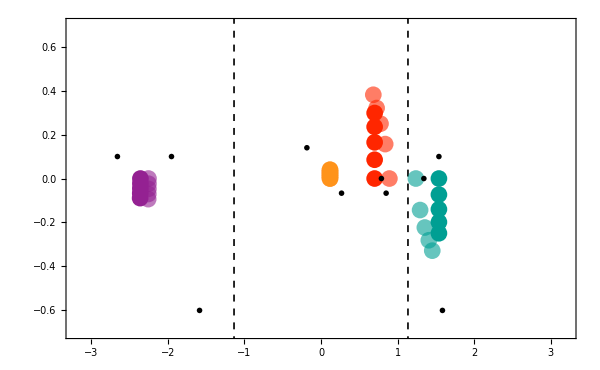

```mathematica
grafs1=Table[{Graphics[{col11,PointSize[0.02],Point[{Re@w11[w0test,imw],Im@w11[w0test,imw]}]}],
Graphics[{col12,PointSize[0.02],Point[{Re@w12[w0test,imw],Im@w12[w0test,imw]}]}],
Graphics[{col13,PointSize[0.02],Point[{Re@w13[w0test,imw],Im@w13[w0test,imw]}]}],
Graphics[{col14,PointSize[0.02],Point[{Re@w14[w0test,imw],Im@w14[w0test,imw]}]}]},
{imw,0,imww,imww/l}];

texts1={Inset[MaTeX["\\omega_\\text{1u}",Magnification->mag],{Re@w11[w0test,imw]+2dx,Im@w11[w0test,imw]+dy/2}],Inset[MaTeX["\\omega_\\text{1ul}",Magnification->mag],{Re@w13[w0test,imw]+3dx,Im@w13[w0test,imw]}],Inset[MaTeX["\\omega_\\text{1ur}",Magnification->mag],{Re@w12[w0test,imw]-3dx,Im@w12[w0test,imw]}],Inset[MaTeX["\\omega_\\text{1v}",Magnification->mag],{Re@w14[w0test,imww]-2dx,Im@w14[w0test,imw]+0.7dy}]};

grafs2=Table[{Graphics[{col21,PointSize[0.02],Point[{Re@w21[w0test,imw],Im@w21[w0test,imw]}]}],Graphics[{col22,PointSize[0.02],Point[{Re@w22[w0test,0],Im@w22[w0test,imw]}]}],Graphics[{col23,PointSize[0.02],Point[{Re@w23[w0test,0],Im@w23[w0test,imw]}]}],
Graphics[{col24,PointSize[0.02],Point[{Re@w24[w0test,imw],Im@w24[w0test,imw]}]}]},
{imw,0,imww,imww/l}];

mag;

texts2={Inset[MaTeX["\\omega_\\text{2u}",Magnification->mag],{Re@w21[w0test,imw]-2dx,Im@w21[w0test,imw]+dy/2}],Inset[MaTeX["\\omega_\\text{2ul}",Magnification->mag],{Re@w23[w0test,imw]+dx,Im@w23[w0test,imw]-dy/3}],Inset[MaTeX["\\omega_\\text{2ur}",Magnification->mag],{Re@w22[w0test,imw],Im@w22[w0test,imw]+dy/2}],Inset[MaTeX["\\omega_\\text{2v}",Magnification->mag],{Re@w24[w0test,imw]+dx,Im@w24[w0test,imw]-dy/3}],
Inset[MaTeX["-\\omega_\\text{h}",Magnification->mag],{-whor[0]-3dx,-0.6}],
Inset[MaTeX["\\omega_\\text{h}",Magnification->mag],{whor[0]+3dx,-0.6}]};

grafcomplex=Show[porig,Plot[{},{w,-3.5,3.5},PlotRange->{{-3.2,3.2},{-0.7,0.7}},FrameTicks->{{True,None},{True,None}},ImageSize->600,Evaluate@plotStyle,FrameLabel->MaTeX[ {"\\text{Re}(\\omega)","\\text{Im}(\\omega)"},Magnification->1.8]],grafs1,grafs2,GridLines->{{-whor[0],whor[0]},{}},GridLinesStyle->Directive[{Black,Dashed,Thickness[0.002]}],Epilog->{texts1,texts2}];
grafcomplex=Show[Plot[{},{w,-3.5,3.5},PlotRange->{{-3.2,3.2},{-0.7,0.7}},FrameTicks->{{True,None},{True,None}},ImageSize->600,Evaluate@plotStyle,FrameLabel->MaTeX[ {"\\text{Re}(\\omega)","\\text{Im}(\\omega)"},Magnification->1.8]],grafs1,grafs2,GridLines->{{-whor[0],whor[0]},{}},GridLinesStyle->Directive[{Black,Dashed,Thickness[0.002]}],Epilog->{texts1,texts2}]
```

```mathematica
|
```

## Root

```mathematica
r901adn005=0.34248+I 1*10^(-10);
```

```mathematica
r902adn005=0.342712+I 1*10^(-10);
```

```mathematica
r903adn005=0.342936+I 8.000098*10^(-6);
```

```mathematica
r904adn005=0.343154+I 8.000098*10^(-6);
```

```mathematica
r905adn005=0.343366+I 0.000016000096;
```

```mathematica
r906adn005=0.343572+I 0.000024000094;
```

```mathematica
r907adn005=0.343772+I 0.000024000094;
```

```mathematica
r908adn005=0.3443554+I 0.000018334;
```

```mathematica
r909adn005=0.34435754+I 0.000018334;
```

```mathematica
r809adn005=0.342004+I 1*10^(-10);
```

```mathematica
r808adn005=0.341752+I 1*10^(-10);
```

```mathematica
r807adn005=0.3415+I 1*10^(-10);
```

```mathematica
r806adn005=0.34126+I 1*10^(-10);
```

```mathematica
r805adn005=0.341+I 0.0000160098;
```

```mathematica
r804adn005=0.34074+I 0.0000180098;
```

```mathematica
r803adn005=0.340476+I 0.0000360096;
```

```mathematica
r802adn005=0.3401+I 0.0000380091;
```

```mathematica
r801adn005=0.339948+I 0.00004016;
```

```mathematica
r706adn005=0.338536+I 0.000026000074;
```

```mathematica
r707adn005=0.338832+I 0.000034000066;
```

```mathematica
r709adn005=0.3394+I 0.000042000058;
```

```mathematica
r708adn005=0.33913+I 0.00004000006;
```

```mathematica
r705adn005=0.338228+I 0.000018000082;
```

```mathematica
r704adn005=0.337916+I 0.00001000009;
```

```mathematica
r703adn005=0.337592+I 4.000096*10^(-6);
```

```mathematica
r702adn005=0.337258+I 10*10^(-10);
```

```mathematica
r701adn005=0.33692+I 10*10^(-10);
```

```mathematica
r609adn005=0.33622+I 0.000010000098;
```

```mathematica
r608adn005=0.335864+I 0.000020000096;
```

```mathematica
r607adn005=0.33551+I 0.000030000094;
```

```mathematica
r606adn005=0.33515+I 0.000040000092;
```

```mathematica
r605adn005=0.3344784+I 0.00005000009;
```

```mathematica
r604adn005=0.33442+I 0.000060000088;
```

```mathematica
r603adn005=0.33404+I 0.000070000086;
```

```mathematica
r602adn005=0.333664+I 0.0000700000859;
```

```mathematica
r601adn005=0.333274+I 0.000060000088;
```

```mathematica
r509adn005=0.332472+I 0.00005000009;
```

```mathematica
r508adn005=0.332062+I 0.000030000094;
```

```mathematica
r507adn005=0.33163+I 0.000020000096;
```

```mathematica
r506adn005=0.33119+I 0.000018000098;
```

```mathematica
r505adn005=0.3307444+I 1*10^(-10);
```

```mathematica
r504adn005=0.3302796+I 1*10^(-10);
```

```mathematica
r502adn005=0.329328+I 1.*10^(-10);
```

*r502adn005 = 0.32836 + I 0.0000150;

```mathematica
r501adn005=0.328846+I 1.200098*10^(-6);
```

```mathematica
r409adn005=0.327892+I 0.00003192;
```

```mathematica
r408adn005=0.327396+I 0.00004338;
```

```mathematica
r407adn005=0.32688+I 0.00005484;
```

```mathematica
r406adn005=0.326384+I 0.00006248;
```

```mathematica
r405adn005=0.325876+I 0.00006630;
```

```mathematica
r404adn005=0.325368+I 0.00006630;
```

```mathematica
r403adn005=0.32485+I 0.00005866;
```

```mathematica
r402adn005=0.323758+I 0.00004338;
```

```mathematica
r401adn005=0.323782+I 0.00002;
```

```mathematica
r309adn005=0.322668+I 1*10^(-9);
```

```mathematica
r308adn005=0.3222092+I 1*10^(-9);
```

```mathematica
r307adn005=0.321508+I 1*10^(-9);
```

```mathematica
r306adn005=0.32091+I 1*10^(-9);
```

```mathematica
r305adn005=0.320316+I 1.000000000002193*10^(-10);
```

```mathematica
r304adn005=0.319712+I 1*10^(-9);
```

```mathematica
r303adn005=0.319112+I 1*10^(-9);
```

```mathematica
r302adn005=0.318512+I 5.219*10^(-6);
```

```mathematica
r301adn005=0.317916+I 0.00003;
```

```mathematica
r202adn005=0.313270+I 62527/3125000000;
```

```mathematica
r203adn005=0.313272+I 1000207/25000000000;
```

```mathematica
r204adn005=0.31385+I 500081/10000000000;
```

```mathematica
r205adn005=0.31442+I 7599/125000000;
```

```mathematica
r206adn005=0.31501+I 35387/500000000;
```

```mathematica
r207adn005=0.31558+I 35387/500000000;
```

```mathematica
r208adn005=0.316154+I 0.000055;(**)
```

```mathematica
r209adn005=0.316736+I 1/20000;
```

```mathematica
r201adn005=0.312+ I 1/1000000;
```

```mathematica
r109adn005=0.31101+I 10^(-10);
```

```mathematica
r108adn005=0.310452+I 10^(-10);
```

```mathematica
r107adn005=0.309925+I 10^(-10);
```

```mathematica
r106adn005=0.309412+I 10^(-9);
```

```mathematica
r105adn005=0.30892+I 0.000014098;
```

```mathematica
r104adn005=0.308456+I 0.000028096;
```

```mathematica
r103adn005=0.308022+I 0.00004294;
```

```mathematica
r102adn005=0.3076134+I 0.0000514;
```

```mathematica
r101adn005=0.307232+I 0.000054;
```

```mathematica
r09adn005=0.306557+I 0.00005176;
```

```mathematica
r08adn005=0.3062644+I 0.00004368;
r07adn005=0.305999+I 0.00003856;
```

```mathematica
(***r07adn005=0.305999+I 0.00003856;***)
r7adn005=0.336576+I 0.000010000098;
```

```mathematica
r06adn005=0.305763+I 0.000028960;
```

```mathematica
r05adn005=0.3055592+I 0.00001936;
```

```mathematica
r04adn005=0.305388+I 0.00001168;
```

```mathematica
r03adn005=0.3052516+I 5.200048*10^(-6);
```

```mathematica
r02adn005=0.3051528+I 1.600084*10^(-6);
```

```mathematica
r1007adn005=0.345656+I 1*10^(-10);
```

```mathematica
r1006adn005=0.34548+I 1*10^(-10);
```

```mathematica
r1005adn005=0.345284+I 1*10^(-10);
```

```mathematica
r1004adn005=0.3451+I 8.0098*10^(-7);
```

```mathematica
r1003adn005=0.34492+I 8.098*10^(-7);
```

```mathematica
r1002adn005=0.34474+I 6.4084*10^(-6);
```

```mathematica
r1001adn005=0.34445468+I 0.000011272;
```

```mathematica
(*r1009adn005=0.34436+I 1*10^(-10);*)
```

```mathematica
r1009adn005=0.346004+I 1*10^(-10);
```

```mathematica
r1101adn005=0.34634+I 8.00006*10^(-6);
```

```mathematica
r1102adn005=0.346495+I 0.00001244;
```

```mathematica
r1103adn005=0.34665+I 0.00001642;
r1104adn005=0.3468004+I 0.0000204;
r1105adn005=0.346948+I 0.0000202;
```

```mathematica
r1106adn005=0.3470944+I 0.0000202;
```

```mathematica
r1107adn005=0.347238+I 0.0000194;
r1108adn005=0.34738+I 0.000016418;
r1109adn005=0.347522+I 0.000012836;
r1201adn005=0.347802+I 4.8076*10^(-6);
r1202adn005=0.347942+I 2.009*10^(-6);
```

```mathematica
r1203adn005=0.348079+I 1*10^(-8);
r1204adn005=0.34821504+I 1*10^(-10);
r1205adn005=0.348349+I 1*10^(-10);
r1206adn005=0.3484804+I 400021/250000000000;
r1207adn005=0.3486092+I 23027/5000000000;
r1208adn005=0.3487344+I 2023/250000000;
r1301adn005=0.349038+I 10^(-7);
```

```mathematica
r01adn005=0.3050926+I 1*10^(-6);
```

```mathematica
r1adn005=0.3068808+I 0.0000570;
r2adn005=0.3115624;
r3adn005=0.3173226+I 0.0000424;
r4adn005=0.3232314+I 0.0000152;
r5adn005=0.3283576+I 0.0000128;
r6adn005=0.3328976+I 0.0000612;
r8adn005=0.3396772+I 0.00004194;
r9adn005=0.342244+I 1*10^(-6);(*Dato dudoso*)
r10adn005=0.3443565+I 0.00001600006;
r11adn005=0.346174+I 2.400088*10^(-6);
(*r11adn005=0.3461716+I 2.09*10^(-6);*)
r12adn005=0.34776626+I 8.856*10^(-6);
r13adn005=0.3499765+I 0.0000145;(**)
r14adn005=0.3500635+I 9/3125000;
r15adn005=0.35102+I 0.000019;
r16adn005=0.32881+I 0.000046;(*Dato dudoso*)
r1601adn005=0.32906+I 0.0000400096;
r1605adn005=0.330056+I 0.0000200098;
r1608adn005=0.330796+I 1*10^(-8);
r17adn005=0.3525662+I 0.000014;
r18adn005=0.35320192+I 6.880*10^(-7);
r19adn005=0.35376+I 5*10^(-6);
r20adn005=0.3542527+5.025*^-6 ⅈ;
r30adn005=0.3571205+I 0;
r40adn005=0.3583177+I 3253/3125000000;
r50adn005=0.35892664+I 7049/2500000000;
r100adn005=0.35982408+I 1/500000000;
```

```mathematica
r01adn001=0.34888132+I 4049/50000000000;
```

```mathematica
r1adn001=0.3489624+I 1.098*10^(-6);
r2adn001=0.3491996+I 1.*10^(-7);(*Mejorar parte compleja*)
r3adn001=0.3495648+I 3.98*10^(-7);
r4adn001=0.35003+I 6.98*10^(-7);
r5adn001=0.3505516+I 2.98*10^(-7);
r505adn001=0.3508286+I 1*10^(-9);
r58adn001=0.350996+I 1.2094*10^(-6);
r6adn001=0.35110872+I 1.648*^-6;
r61adn001=0.3511644+I 1.6092*10^(-6);
r7adn001=0.35166928+I 4.098*10^(-7);
r8adn001=0.35221944+I 1.4086*10^(-6);
r9adn001=0.35274696+I 0; (*Dudosa parte im*)
r10adn001=0.35324376+I 23/12500000;
r11adn001=0.35369+I 0.00000200008;(*Dudosa parte im*)
r12adn001=0.35414+I 2.00098*10^(-6);
r13adn001=0.35454+I 9.6*^-7;
r14adn001=0.354906+I 1/25000000;
r15adn001=0.3552436+I 11/15625000;
r16adn001=0.35555292+I 71/500000000;
r17adn001=0.3558366+I 7/12500000;
r18adn001=0.35609816+I 1.009*10^(-7);
r19adn001=0.356337+I 6.04*10^(-7);
r20adn001=0.35655868+4.78*^-7 ⅈ;
```

```mathematica
r1008adn005=0.345832+I 1*10^(-10);
```

```mathematica
r8bdn005=0.304976+I 10^(-10);
r14bdn001=0.34678+I 1/250000000;(*im *)
r6adn01=0.3328976+I 0.0000612;
r10adn01=0.3401416+I 0.000119235;
r13bdn005=0.319695+I 0.00004869999;
r14bdn005=0.3489765+I 0.0000145;
r20bdn001=0.34908428+5.08*^-7 ⅈ;
r20adn003a=0.3549427+I 0.000002176;
r20bdn003b=0.340478+I 3.36*10^(-6);
r20bdn005=0.33726325+0.0000258 ⅈ;
r20cdn005=0.312921+0.0000116 ⅈ;
(*r20adn01=0.357+I 0.000005; 
r20bdn01=0.34504+I 0.000017;*)
r20adn01=0.353427+I 0.00001224;
r20bdn01=0.333575+I 0.00002128;
r20cdn01=0.264596+I 0.000172;
```

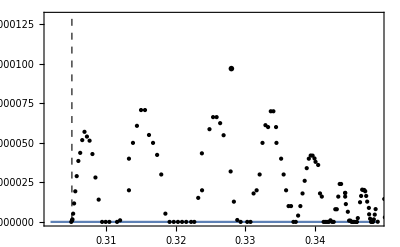

```mathematica
wri005=Plot[0,{x,0.302,0.349},PlotRange->{0,0.00013},Axes->True,Evaluate@plotStyle,FrameLabel->MaTeX[{"\\text{Re}(\\omega')","\\text{Im}(\\omega')"},Magnification->1.8],Frame->{{True,True},{True,True}},FrameTicks->{{True,None},{True,None}},

GridLines->{{Wph[0.05]},{}},Epilog->{Inset[MaTeX["\\delta\\text{n}=0.05",Magnification->m],{0.328,0.000097}],PointSize[Medium],
Black, Point[{{Re@r01adn005,Im@r01adn005}}],
Black, Point[{{Re@r1adn005,Im@r1adn005}}],
Black, Point[{{Re@r2adn005,Im@r2adn005}}],
Black, Point[{{Re@r3adn005,Im@r3adn005}}],
Black, Point[{{Re@r4adn005,Im@r4adn005}}],
Black,Point[{{Re@r5adn005,Im@r5adn005}}],
Black,Point[{{Re@r6adn005,Im@r6adn005}}],
Black,Point[{{Re@r8adn005,Im@r8adn005}}],
Black,Point[{{Re@r9adn005,Im@r9adn005}}],
Black,Point[{{Re@r10adn005,Im@r10adn005}}],
Black,Point[{{Re@r11adn005,Im@r11adn005}}],
Black,Point[{{Re@r12adn005,Im@r12adn005}}],
Black,Point[{{Re@r13adn005,Im@r13adn005}}],
Black,Point[{{Re@r14adn005,Im@r14adn005}}],
Black,Point[{{Re@r15adn005,Im@r15adn005}}],
Black,Point[{{Re@r17adn005,Im@r17adn005}}],
Black,Point[{{Re@r18adn005,Im@r18adn005}}],
Black,Point[{{Re@r19adn005,Im@r19adn005}}],
Black,Point[{{Re@r20adn005,Im@r20adn005}}],
Black,Point[{{Re@r30adn005,Im@r30adn005}}],
Black,Point[{{Re@r40adn005,Im@r40adn005}}],
Black,Point[{{Re@r50adn005,Im@r50adn005}}],
Black,Point[{{Re@r8bdn005,Im@r8bdn005}}],

Black,Point[{{Re@r1102adn005,Im@r1102adn005}}],
Black,Point[{{Re@r1103adn005,Im@r1103adn005}}],
Black,Point[{{Re@r1104adn005,Im@r1104adn005}}],
Black,Point[{{Re@r1105adn005,Im@r1105adn005}}],
Black,Point[{{Re@r1106adn005,Im@r1106adn005}}],
Black,Point[{{Re@r1107adn005,Im@r1107adn005}}],
Black,Point[{{Re@r1108adn005,Im@r1108adn005}}],
Black,Point[{{Re@r1109adn005,Im@r1109adn005}}],
Black,Point[{{Re@r1201adn005,Im@r1201adn005}}],
Black,Point[{{Re@r1202adn005,Im@r1202adn005}}],
Black,Point[{{Re@r1203adn005,Im@r1203adn005}}],
Black,Point[{{Re@r1204adn005,Im@r1204adn005}}],
Black,Point[{{Re@r1205adn005,Im@r1205adn005}}],
Black,Point[{{Re@r1206adn005,Im@r1206adn005}}],
Black,Point[{{Re@r1207adn005,Im@r1207adn005}}],
Black,Point[{{Re@r1208adn005,Im@r1208adn005}}],
Black,Point[{{Re@r1301adn005,Im@r1301adn005}}],
Black,Point[{{Re@r1009adn005,Im@r1009adn005}}],
Black,Point[{{Re@r1001adn005,Im@r1001adn005}}],
Black,Point[{{Re@r1002adn005,Im@r1002adn005}}],
Black,Point[{{Re@r1003adn005,Im@r1003adn005}}],
Black,Point[{{Re@r1004adn005,Im@r1004adn005}}],
Black,Point[{{Re@r1005adn005,Im@r1005adn005}}],
Black,Point[{{Re@r1006adn005,Im@r1006adn005}}],
Black,Point[{{Re@r1007adn005,Im@r1007adn005}}],

Black,Point[{{Re@r1009adn005,Im@r1009adn005}}],
Black,Point[{{Re@r1009adn005,Im@r1009adn005}}],
Black,Point[{{Re@r01adn005,Im@r01adn005}}],
Black,Point[{{Re@r02adn005,Im@r02adn005}}],
Black,Point[{{Re@r03adn005,Im@r03adn005}}],
Black,Point[{{Re@r04adn005,Im@r04adn005}}],
Black,Point[{{Re@r05adn005,Im@r05adn005}}],
Black,Point[{{Re@r06adn005,Im@r06adn005}}],
Black,Point[{{Re@r07adn005,Im@r07adn005}}],
Black,Point[{{Re@r08adn005,Im@r08adn005}}],
Black,Point[{{Re@r09adn005,Im@r09adn005}}],
Black,Point[{{Re@r101adn005,Im@r101adn005}}],
Black,Point[{{Re@r102adn005,Im@r102adn005}}],
Black,Point[{{Re@r103adn005,Im@r103adn005}}],
Black,Point[{{Re@r104adn005,Im@r104adn005}}],
Black,Point[{{Re@r105adn005,Im@r105adn005}}],
Black,Point[{{Re@r106adn005,Im@r106adn005}}],
Black,Point[{{Re@r107adn005,Im@r107adn005}}],
Black,Point[{{Re@r108adn005,Im@r108adn005}}],
Black,Point[{{Re@r209adn005,Im@r209adn005}}],
Black,Point[{{Re@r208adn005,Im@r208adn005}}],
Black,Point[{{Re@r207adn005,Im@r207adn005}}],
Black,Point[{{Re@r206adn005,Im@r206adn005}}],
Black,Point[{{Re@r205adn005,Im@r205adn005}}],
Black,Point[{{Re@r204adn005,Im@r204adn005}}],
Black,Point[{{Re@r203adn005,Im@r203adn005}}],
Black,Point[{{Re@r202adn005,Im@r202adn005}}],
Black,Point[{{Re@r201adn005,Im@r201adn005}}],
Black,Point[{{Re@r301adn005,Im@r301adn005}}],
Black,Point[{{Re@r302adn005,Im@r302adn005}}],
Black,Point[{{Re@r303adn005,Im@r303adn005}}],
Black,Point[{{Re@r304adn005,Im@r304adn005}}],
Black,Point[{{Re@r305adn005,Im@r305adn005}}],
Black,Point[{{Re@r306adn005,Im@r306adn005}}],
Black,Point[{{Re@r307adn005,Im@r307adn005}}],
Black,Point[{{Re@r308adn005,Im@r308adn005}}],
Black,Point[{{Re@r309adn005,Im@r309adn005}}],
Black,Point[{{Re@r401adn005,Im@r401adn005}}],
Black,Point[{{Re@r402adn005,Im@r402adn005}}],
Black,Point[{{Re@r403adn005,Im@r403adn005}}],
Black,Point[{{Re@r404adn005,Im@r404adn005}}],
Black,Point[{{Re@r405adn005,Im@r405adn005}}],
Black,Point[{{Re@r406adn005,Im@r406adn005}}],
Black,Point[{{Re@r407adn005,Im@r407adn005}}],
Black,Point[{{Re@r409adn005,Im@r409adn005}}],
Black,Point[{{Re@r501adn005,Im@r501adn005}}],
Black,Point[{{Re@r502adn005,Im@r502adn005}}],
Black,Point[{{Re@r504adn005,Im@r504adn005}}],
Black,Point[{{Re@r505adn005,Im@r505adn005}}],
Black,Point[{{Re@r506adn005,Im@r506adn005}}],
Black,Point[{{Re@r507adn005,Im@r507adn005}}],
Black,Point[{{Re@r508adn005,Im@r508adn005}}],
Black,Point[{{Re@r509adn005,Im@r509adn005}}],
Black,Point[{{Re@r601adn005,Im@r601adn005}}],
Black,Point[{{Re@r602adn005,Im@r602adn005}}],
Black,Point[{{Re@r603adn005,Im@r603adn005}}],
Black,Point[{{Re@r604adn005,Im@r604adn005}}],
Black,Point[{{Re@r605adn005,Im@r605adn005}}],
Black,Point[{{Re@r606adn005,Im@r606adn005}}],
Black,Point[{{Re@r607adn005,Im@r607adn005}}],
Black,Point[{{Re@r608adn005,Im@r608adn005}}],
Black,Point[{{Re@r609adn005,Im@r609adn005}}],
Black,Point[{{Re@r701adn005,Im@r701adn005}}],
Black,Point[{{Re@r702adn005,Im@r702adn005}}],
Black,Point[{{Re@r703adn005,Im@r703adn005}}],
Black,Point[{{Re@r704adn005,Im@r704adn005}}],
Black,Point[{{Re@r705adn005,Im@r705adn005}}],
Black,Point[{{Re@r7adn005,Im@r7adn005}}],
Black,Point[{{Re@r706adn005,Im@r706adn005}}],
Black,Point[{{Re@r707adn005,Im@r707adn005}}],
Black,Point[{{Re@r708adn005,Im@r708adn005}}],
Black,Point[{{Re@r709adn005,Im@r709adn005}}],
Black,Point[{{Re@r801adn005,Im@r801adn005}}],
Black,Point[{{Re@r802adn005,Im@r802adn005}}],
Black,Point[{{Re@r803adn005,Im@r803adn005}}],
Black,Point[{{Re@r804adn005,Im@r804adn005}}],
Black,Point[{{Re@r805adn005,Im@r805adn005}}],
Black,Point[{{Re@r806adn005,Im@r806adn005}}],
Black,Point[{{Re@r807adn005,Im@r807adn005}}],
Black,Point[{{Re@r808adn005,Im@r808adn005}}],
Black,Point[{{Re@r809adn005,Im@r809adn005}}],
Black,Point[{{Re@r901adn005,Im@r901adn005}}],
Black,Point[{{Re@r902adn005,Im@r902adn005}}],
Black,Point[{{Re@r903adn005,Im@r903adn005}}],
Black,Point[{{Re@r904adn005,Im@r904adn005}}],
Black,Point[{{Re@r905adn005,Im@r905adn005}}],
Black,Point[{{Re@r906adn005,Im@r906adn005}}],
Black,Point[{{Re@r907adn005,Im@r907adn005}}],
Black,Point[{{Re@r908adn005,Im@r908adn005}}],
Black,Point[{{Re@r909adn005,Im@r909adn005}}]
}]
```

```mathematica
color1
```

RGBColor[0, 0.6, 0.6]

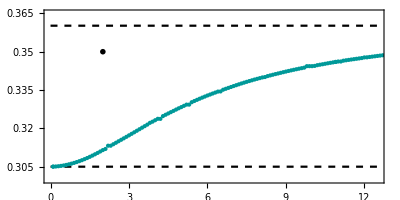

```mathematica
wrt005=Plot[{Wph[0.05],Wph[0]},{x,0,12.5},PlotRange->{0.30,0.365},AspectRatio->0.5,Axes->True,FrameTicks->{{{0.305,0.320,0.335,0.350,0.365},None},{None,None}},Evaluate@plotStyle,FrameLabel->MaTeX[{"","\\text{Re}(\\omega')"},Magnification->1.8],PlotStyle->{{Black,Dashed}},Epilog->{Inset[MaTeX["\\delta\\text{n}=0.05",Magnification->m],{2,0.35}],PointSize[Medium],
color1, Point[{{0.1,Re@r01adn005}}],
color1, Point[{{1,Re@r1adn005}}],
color1, Point[{{2,Re@r2adn005}}],
color1, Point[{{3,Re@r3adn005}}],
color1, Point[{{4,Re@r4adn005}}],
color1,Point[{{5,Re@r5adn005}}],
color1,Point[{{6,Re@r6adn005}}],
color1,Point[{{8,Re@r8adn005}}],
color1,Point[{{9,Re@r9adn005}}],
color1,Point[{{10,Re@r10adn005}}],
color1,Point[{{11,Re@r11adn005}}],
color1,Point[{{12,Re@r12adn005}}],
color1,Point[{{13,Re@r13adn005}}],
color1,Point[{{14,Re@r14adn005}}],
color1,Point[{{15,Re@r15adn005}}],
color2,Point[{{16,Re@r16adn005}}],
color1,Point[{{16.1,Re@r1601adn005}}],
color1,Point[{{16.5,Re@r1605adn005}}],
color1,Point[{{16.8,Re@r1608adn005}}],
color1,Point[{{17,Re@r17adn005}}],
color1,Point[{{18,Re@r18adn005}}],
color1,Point[{{19,Re@r19adn005}}],
color1,Point[{{20,Re@r20adn005}}],
color1,Point[{{30,Re@r30adn005}}],
color1,Point[{{40,Re@r40adn005}}],
color1,Point[{{50,Re@r50adn005}}],
color1,Point[{{13,Re@r13bdn005}}],
color1,Point[{{14,Re@r14bdn005}}],
color1,Point[{{20,Re@r20bdn005}}],
color1,Point[{{100,Re@r100adn005}}],
color1,Point[{{11.7,Re@r1107adn005}}],
color1,Point[{{11.8,Re@r1108adn005}}],
color1,Point[{{11.9,Re@r1109adn005}}],
color1,Point[{{11.6,Re@r1106adn005}}],
color1,Point[{{11.5,Re@r1105adn005}}],
color1,Point[{{11.4,Re@r1104adn005}}],
color1,Point[{{11.3,Re@r1103adn005}}],
color1,Point[{{11.2,Re@r1102adn005}}],
color1,Point[{{11.1,Re@r1101adn005}}],
color1,Point[{{12.1,Re@r1201adn005}}],
color1,Point[{{12.2,Re@r1202adn005}}],
color1,Point[{{12.3,Re@r1203adn005}}],
color1,Point[{{12.4,Re@r1204adn005}}],
color1,Point[{{12.5,Re@r1205adn005}}],
color1,Point[{{12.6,Re@r1206adn005}}],
color1,Point[{{12.7,Re@r1207adn005}}],
color1,Point[{{12.8,Re@r1208adn005}}],
color1,Point[{{13.1,Re@r1301adn005}}],
color1,Point[{{10.9,Re@r1009adn005}}],
color1,Point[{{10.1,Re@r1001adn005}}],
color1,Point[{{10.2,Re@r1002adn005}}],
color1,Point[{{10.3,Re@r1003adn005}}],
color1,Point[{{10.4,Re@r1004adn005}}],
color1,Point[{{10.5,Re@r1005adn005}}],
color1,Point[{{10.6,Re@r1006adn005}}],
color1,Point[{{10.7,Re@r1007adn005}}],
color1,Point[{{10.8,Re@r1008adn005}}],
color1,Point[{{10.9,Re@r1009adn005}}],
color1,Point[{{0.1,Re@r01adn005}}],
color1,Point[{{0.2,Re@r02adn005}}],
color1,Point[{{0.3,Re@r03adn005}}],
color1,Point[{{0.4,Re@r04adn005}}],
color1,Point[{{0.5,Re@r05adn005}}],
color1,Point[{{0.6,Re@r06adn005}}],
color1,Point[{{0.7,Re@r07adn005}}],
color1,Point[{{0.8,Re@r08adn005}}],
color1,Point[{{0.9,Re@r09adn005}}],
color1,Point[{{1.1,Re@r101adn005}}],
color1,Point[{{1.2,Re@r102adn005}}],
color1,Point[{{1.3,Re@r103adn005}}],
color1,Point[{{1.4,Re@r104adn005}}],
color1,Point[{{1.5,Re@r105adn005}}],
color1,Point[{{1.6,Re@r106adn005}}],
color1,Point[{{1.7,Re@r107adn005}}],
color1,Point[{{1.8,Re@r108adn005}}],
color1,Point[{{1.9,Re@r109adn005}}],
color1,Point[{{2.1,Re@r201adn005}}],
color1,Point[{{2.2,Re@r202adn005}}],
color1,Point[{{2.3,Re@r203adn005}}],
color1,Point[{{2.4,Re@r204adn005}}],
color1,Point[{{2.5,Re@r205adn005}}],
color1,Point[{{2.6,Re@r206adn005}}],
color1,Point[{{2.7,Re@r207adn005}}],
color1,Point[{{2.8,Re@r208adn005}}],
color1,Point[{{2.9,Re@r209adn005}}],
color1,Point[{{3.1,Re@r301adn005}}],
color1,Point[{{3.2,Re@r302adn005}}],
color1,Point[{{3.3,Re@r303adn005}}],
color1,Point[{{3.4,Re@r304adn005}}],
color1,Point[{{3.5,Re@r305adn005}}],
color1,Point[{{3.6,Re@r306adn005}}],
color1,Point[{{3.7,Re@r307adn005}}],
color1,Point[{{3.8,Re@r308adn005}}],
color1,Point[{{3.9,Re@r309adn005}}],
color1,Point[{{4.1,Re@r401adn005}}],
color1,Point[{{4.2,Re@r402adn005}}],
color1,Point[{{4.3,Re@r403adn005}}],
color1,Point[{{4.4,Re@r404adn005}}],
color1,Point[{{4.5,Re@r405adn005}}],
color1,Point[{{4.6,Re@r406adn005}}],
color1,Point[{{4.7,Re@r407adn005}}],
color1,Point[{{4.8,Re@r408adn005}}],
color1,Point[{{4.9,Re@r409adn005}}],
color1,Point[{{5.1,Re@r501adn005}}],
color1,Point[{{5.2,Re@r502adn005}}],
color1,Point[{{5.3,Re@r502adn005}}],(**)
color1,Point[{{5.4,Re@r504adn005}}],
color1,Point[{{5.5,Re@r505adn005}}],
color1,Point[{{5.6,Re@r506adn005}}],
color1,Point[{{5.7,Re@r507adn005}}],
color1,Point[{{5.8,Re@r508adn005}}],
color1,Point[{{5.9,Re@r509adn005}}],
color1,Point[{{6.1,Re@r601adn005}}],
color1,Point[{{6.2,Re@r602adn005}}],
color1,Point[{{6.3,Re@r603adn005}}],
color1,Point[{{6.4,Re@r604adn005}}],
color1,Point[{{6.5,Re@r605adn005}}],
color1,Point[{{6.6,Re@r606adn005}}],
color1,Point[{{6.7,Re@r607adn005}}],
color1,Point[{{6.8,Re@r608adn005}}],
color1,Point[{{6.9,Re@r609adn005}}],
color1,Point[{{7.1,Re@r701adn005}}],
color1,Point[{{7.2,Re@r702adn005}}],
color1,Point[{{7.3,Re@r703adn005}}],
color1,Point[{{7.4,Re@r704adn005}}],
color1,Point[{{7.5,Re@r705adn005}}],
color1,Point[{{7.6,Re@r706adn005}}],
color1,Point[{{7.7,Re@r707adn005}}],
color1,Point[{{7.8,Re@r708adn005}}],
color1,Point[{{7.9,Re@r709adn005}}],
color1,Point[{{8.1,Re@r801adn005}}],
color1,Point[{{8.2,Re@r802adn005}}],
color1,Point[{{8.3,Re@r803adn005}}],
color1,Point[{{8.4,Re@r804adn005}}],
color1,Point[{{8.5,Re@r805adn005}}],
color1,Point[{{8.6,Re@r806adn005}}],
color1,Point[{{8.7,Re@r807adn005}}],
color1,Point[{{8.8,Re@r808adn005}}],
color1,Point[{{8.9,Re@r809adn005}}],
color1,Point[{{9.1,Re@r901adn005}}],
color1,Point[{{9.2,Re@r902adn005}}],
color1,Point[{{9.3,Re@r903adn005}}],
color1,Point[{{9.4,Re@r904adn005}}],
color1,Point[{{9.5,Re@r905adn005}}],
color1,Point[{{9.6,Re@r906adn005}}],
color1,Point[{{9.7,Re@r907adn005}}],
color1,Point[{{9.8,Re@r908adn005}}],
color1,Point[{{9.9,Re@r909adn005}}],
color1,Point[{{7,Re@r7adn005}}]

}]
```

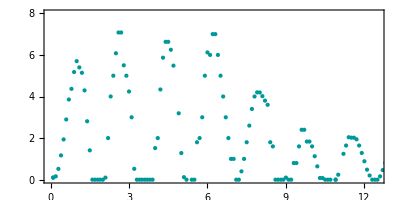

```mathematica
wit005=Plot[-1,{x,0,12.5},PlotRange->{0,8},
Axes->True,Evaluate@plotStyle,AspectRatio->0.5,FrameLabel->MaTeX[{"\\tau_c(\\text{fs})","\\text{Im}(\\omega')[10^{-5}]"},Magnification->1.8],Frame->{{True,True},{True,True}},FrameTicks->{{True,None},{True,None}},
Epilog->{PointSize[Medium],
color1, Point[{{0.1,10^5Im@r01adn005}}],
color1, Point[{{1,10^5Im@r1adn005}}],
color1, Point[{{2,10^5Im@r2adn005}}],
color1, Point[{{3,10^5Im@r3adn005}}],
color1, Point[{{4,10^5Im@r4adn005}}],
color1,Point[{{5,10^5Im@r5adn005}}],
color1,Point[{{6,10^5Im@r6adn005}}],
color1,Point[{{8,10^5Im@r8adn005}}],
color1,Point[{{9,10^5Im@r9adn005}}],
color1,Point[{{10,10^5Im@r10adn005}}],
color1,Point[{{11,10^5Im@r11adn005}}],
color1,Point[{{12,10^5Im@r12adn005}}],
color1,Point[{{13,10^5Im@r13adn005}}],
color1,Point[{{14,10^5Im@r14adn005}}],
color1,Point[{{15,10^5Im@r15adn005}}],
color1,Point[{{16,10^5Im@r16adn005}}],
color1,Point[{{16.1,10^5Im@r1601adn005}}],
color1,Point[{{16.5,10^5Im@r1605adn005}}],
color1,Point[{{16.8,10^5Im@r1608adn005}}],
color1,Point[{{17,10^5Im@r17adn005}}],
color1,Point[{{18,10^5Im@r18adn005}}],
color1,Point[{{19,10^5Im@r19adn005}}],
color1,Point[{{20,10^5Im@r20adn005}}],
color1,Point[{{30,10^5Im@r30adn005}}],
color1,Point[{{40,10^5Im@r40adn005}}],
color1,Point[{{50,10^5Im@r50adn005}}],
color1,Point[{{100,10^5Im@r100adn005}}],
color1,Point[{{11.7,10^5Im@r1107adn005}}],
color1,Point[{{11.8,10^5Im@r1108adn005}}],
color1,Point[{{11.9,10^5Im@r1109adn005}}],
color1,Point[{{11.6,10^5Im@r1106adn005}}],
color1,Point[{{11.5,10^5Im@r1105adn005}}],
color1,Point[{{11.4,10^5Im@r1104adn005}}],
color1,Point[{{11.3,10^5Im@r1103adn005}}],
color1,Point[{{11.2,10^5Im@r1102adn005}}],
color1,Point[{{12.1,10^5Im@r1201adn005}}],
color1,Point[{{12.2,10^5Im@r1202adn005}}],
color1,Point[{{12.3,10^5Im@r1203adn005}}],
color1,Point[{{12.4,10^5Im@r1204adn005}}],
color1,Point[{{12.5,10^5Im@r1205adn005}}],
color1,Point[{{12.6,10^5Im@r1206adn005}}],
color1,Point[{{12.7,10^5Im@r1207adn005}}],
color1,Point[{{12.8,10^5Im@r1208adn005}}],
color1,Point[{{10.9,10^5Im@r1009adn005}}],
color1,Point[{{10.1,10^5Im@r1001adn005}}],
color1,Point[{{10.2,10^5Im@r1002adn005}}],
color1,Point[{{10.3,10^5Im@r1003adn005}}],
color1,Point[{{10.4,10^5Im@r1004adn005}}],
color1,Point[{{10.5,10^5Im@r1005adn005}}],
color1,Point[{{10.6,10^5Im@r1006adn005}}],
color1,Point[{{10.7,10^5Im@r1007adn005}}],
color1,Point[{{10.9,10^5Im@r1009adn005}}],
color1,Point[{{0.1,10^5Im@r01adn005}}],
color1,Point[{{0.2,10^5Im@r02adn005}}],
color1,Point[{{0.3,10^5Im@r03adn005}}],
color1,Point[{{0.4,10^5Im@r04adn005}}],
color1,Point[{{0.5,10^5Im@r05adn005}}],
color1,Point[{{0.6,10^5Im@r06adn005}}],
color1,Point[{{0.7,10^5Im@r07adn005}}],
color1,Point[{{0.8,10^5Im@r08adn005}}],
color1,Point[{{0.9,10^5Im@r09adn005}}],
color1,Point[{{1.1,10^5Im@r101adn005}}],
color1,Point[{{1.2,10^5Im@r102adn005}}],
color1,Point[{{1.3,10^5Im@r103adn005}}],
color1,Point[{{1.4,10^5Im@r104adn005}}],
color1,Point[{{1.5,10^5Im@r105adn005}}],
color1,Point[{{1.6,10^5Im@r106adn005}}],
color1,Point[{{1.7,10^5Im@r107adn005}}],
color1,Point[{{1.8,10^5Im@r108adn005}}],
color1,Point[{{1.9,10^5Im@r109adn005}}],
color1,Point[{{2.1,10^5Im@r201adn005}}],
color1,Point[{{2.2,10^5Im@r202adn005}}],
color1,Point[{{2.3,10^5Im@r203adn005}}],
color1,Point[{{2.4,10^5Im@r204adn005}}],
color1,Point[{{2.5,10^5Im@r205adn005}}],
color1,Point[{{2.6,10^5Im@r206adn005}}],
color1,Point[{{2.7,10^5Im@r207adn005}}],
color1,Point[{{2.8,10^5Im@r208adn005}}],
color1,Point[{{2.9,10^5Im@r209adn005}}],
color1,Point[{{3.1,10^5Im@r301adn005}}],
color1,Point[{{3.2,10^5Im@r302adn005}}],
color1,Point[{{3.3,10^5Im@r303adn005}}],
color1,Point[{{3.4,10^5Im@r304adn005}}],
color1,Point[{{3.5,10^5Im@r305adn005}}],
color1,Point[{{3.6,10^5Im@r306adn005}}],
color1,Point[{{3.7,10^5Im@r307adn005}}],
color1,Point[{{3.8,10^5Im@r308adn005}}],
color1,Point[{{3.9,10^5Im@r309adn005}}],
color1,Point[{{4.1,10^5Im@r401adn005}}],
color1,Point[{{4.2,10^5Im@r402adn005}}],
color1,Point[{{4.3,10^5Im@r403adn005}}],
color1,Point[{{4.4,10^5Im@r404adn005}}],
color1,Point[{{4.5,10^5Im@r405adn005}}],
color1,Point[{{4.6,10^5Im@r406adn005}}],
color1,Point[{{4.7,10^5Im@r407adn005}}],
color1,Point[{{4.9,10^5Im@r409adn005}}],
color1,Point[{{5.1,10^5Im@r501adn005}}],
color1,Point[{{5.2,10^5Im@r502adn005}}],
color1,Point[{{5.4,10^5Im@r504adn005}}],
color1,Point[{{5.5,10^5Im@r505adn005}}],
color1,Point[{{5.6,10^5Im@r506adn005}}],
color1,Point[{{5.7,10^5Im@r507adn005}}],
color1,Point[{{5.8,10^5Im@r508adn005}}],
color1,Point[{{5.9,10^5Im@r509adn005}}],
color1,Point[{{6.1,10^5Im@r601adn005}}],
color1,Point[{{6.2,10^5Im@r602adn005}}],
color1,Point[{{6.3,10^5Im@r603adn005}}],
color1,Point[{{6.4,10^5Im@r604adn005}}],
color1,Point[{{6.5,10^5Im@r605adn005}}],
color1,Point[{{6.6,10^5Im@r606adn005}}],
color1,Point[{{6.7,10^5Im@r607adn005}}],
color1,Point[{{6.8,10^5Im@r608adn005}}],
color1,Point[{{6.9,10^5Im@r609adn005}}],
color1,Point[{{7,10^5Im@r7adn005}}],
color1,Point[{{7.1,10^5Im@r701adn005}}],
color1,Point[{{7.2,10^5Im@r702adn005}}],
color1,Point[{{7.3,10^5Im@r703adn005}}],
color1,Point[{{7.4,10^5Im@r704adn005}}],
color1,Point[{{7.5,10^5Im@r705adn005}}],
color1,Point[{{7.6,10^5Im@r706adn005}}],
color1,Point[{{7.7,10^5Im@r707adn005}}],
color1,Point[{{7.8,10^5Im@r708adn005}}],
color1,Point[{{7.9,10^5Im@r709adn005}}],
color1,Point[{{8.1,10^5Im@r801adn005}}],
color1,Point[{{8.2,10^5Im@r802adn005}}],
color1,Point[{{8.3,10^5Im@r803adn005}}],
color1,Point[{{8.4,10^5Im@r804adn005}}],
color1,Point[{{8.5,10^5Im@r805adn005}}],
color1,Point[{{8.6,10^5Im@r806adn005}}],
color1,Point[{{8.7,Im@r807adn005}}],
color1,Point[{{8.8,10^5Im@r808adn005}}],
color1,Point[{{8.9,Im@r809adn005}}],
color1,Point[{{9.1,10^5Im@r901adn005}}],
color1,Point[{{9.2,10^5Im@r902adn005}}],
color1,Point[{{9.3,10^5Im@r903adn005}}],
color1,Point[{{9.4,10^5Im@r904adn005}}],
color1,Point[{{9.5,10^5Im@r905adn005}}],
color1,Point[{{9.6,10^5Im@r906adn005}}],
color1,Point[{{9.7,10^5Im@r907adn005}}],
color1,Point[{{9.8,10^5Im@r908adn005}}],
color1,Point[{{9.9,10^5Im@r909adn005}}]}]
```

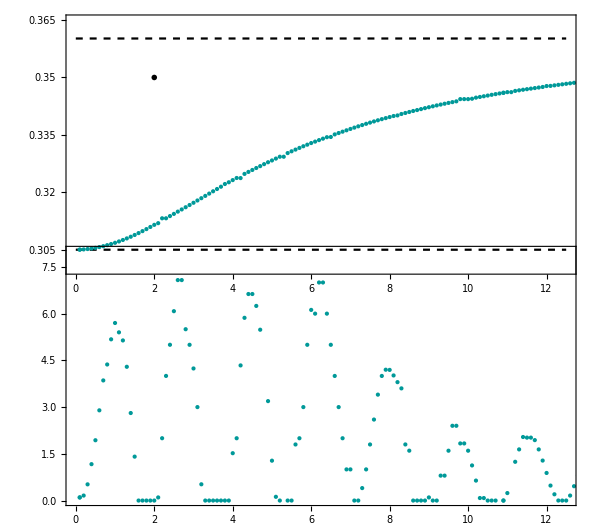

```mathematica
p6=GraphicsGrid[{{wrt005},{wit005}},Spacings->{-80
,-41},ImageSize->600]
```

```mathematica
Export["P.pdf",p6]
```

P.pdf

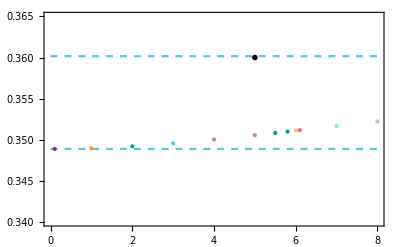

```mathematica
wrt001=Plot[{Wph[0.01],Wph[0.0]},{x,0.,8},PlotRange->{0.340,0.365},Axes->True,Evaluate@plotStyle,FrameLabel->MaTeX[{"\\tau_c","\\text{Re}(\\omega')"},Magnification->1.8],PlotStyle->{{color3,Dashed}},Frame->{{True,True},{True,True}},FrameTicks->{{True,None},{True,None}},Epilog->{Inset[MaTeX["\\delta\\text{n}=0.01",Magnification->m],{5,0.36}],PointSize[Medium],
col21, Point[{{0.1,Re@r01adn001}}],
col24, Point[{{1,Re@r1adn001}}],
col22, Point[{{2,Re@r2adn001}}],
color3, Point[{{3,Re@r3adn001}}],
color4, Point[{{4,Re@r4adn001}}],
color5, Point[{{5,Re@r5adn001}}],
color1, Point[{{5.5,Re@r505adn001}}],
color1, Point[{{5.8,Re@r58adn001}}],
col14, Point[{{6,Re@r6adn001}}],
Red, Point[{{6.1,Re@r61adn001}}],
color3, Point[{{7,Re@r7adn001}}],
color4, Point[{{8,Re@r8adn001}}],
color5, Point[{{9,Re@r9adn001}}],
col13, Point[{{10,Re@r10adn001}}],
color1, Point[{{11,Re@r11adn001}}],
color1, Point[{{12,Re@r12adn001}}],
col12, Point[{{13,Re@r13adn001}}],
col11, Point[{{14,Re@r14adn001}}],
col24, Point[{{15,Re@r16adn001}}],
color2, Point[{{16,Re@r16adn001}}],
color3, Point[{{17,Re@r17adn001}}],
color1, Point[{{18,Re@r18adn001}}],
col11, Point[{{19,Re@r19adn001}}],
Cyan,Point[{{20,Re@r20adn001}}],
color1,Point[{{20,Re@r20bdn001}}],
color1,Point[{{14,Re@r14bdn001}}]}]
```

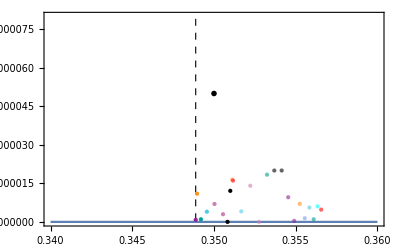

```mathematica
wir001=Plot[0,{x,0.34,0.36},PlotRange->{0,8*10^(-6)},Axes->True,Evaluate@plotStyle,FrameLabel->MaTeX[{"\\text{Re}(\\omega')","\\text{Im}(\\omega')"},Magnification->1.8],Frame->{{True,True},{True,True}},FrameTicks->{{True,None},{True,None}},

GridLines->{{Wph[0.01]},{}},Epilog->{Inset[MaTeX["\\delta\\text{n}=0.01",Magnification->m],{0.35,5*10^(-6)}],PointSize[Medium],
col21, Point[{{Re@r01adn001,Im@r01adn001}}],
col24, Point[{{Re@r1adn001,Im@r1adn001}}],
col22, Point[{{Re@r2adn001,Im@r2adn001}}],
color3, Point[{{Re@r3adn001,Im@r3adn001}}],
color4, Point[{{Re@r4adn001,Im@r4adn001}}],
color5, Point[{{Re@r5adn001,Im@r5adn001}}],
color1, Point[{{Re@r505adn001,Im@r505adn001}}],
color1, Point[{{Re@r58adn001,Im@r58adn001}}],
col14, Point[{{Re@r6adn001,Im@r6adn001}}],
Red, Point[{{Re@r61adn001,Im@r61adn001}}],
color3, Point[{{Re@r7adn001,Im@r7adn001}}],
color4, Point[{{Re@r8adn001,Im@r8adn001}}],
color5, Point[{{Re@r9adn001,Im@r9adn001}}],
col12, Point[{{Re@r10adn001,Im@r10adn001}}],
color1, Point[{{Re@r11adn001,Im@r11adn001}}],
color1, Point[{{Re@r12adn001,Im@r12adn001}}],
col11, Point[{{Re@r13adn001,Im@r13adn001}}],
col21, Point[{{Re@r14adn001,Im@r14adn001}}],
col24,Point[{{Re@r15adn001,Im@r15adn001}}],
color2,Point[{{Re@r16adn001,Im@r16adn001}}],
color3,Point[{{Re@r17adn001,Im@r17adn001}}],
color1,Point[{{Re@r18adn001,Im@r18adn001}}],
Cyan,Point[{{Re@r19adn001,Im@r19adn001}}],
Red,Point[{{Re@r20adn001,Im@r20adn001}}]}]
```

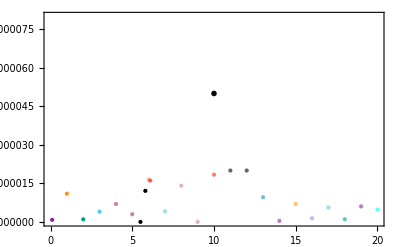

-Graphics-

Export::noopen: Cannot open P.pdf.

$Failed

```mathematica
wit001=Plot[-1,{x,0.,20},PlotRange->{0,8*10^(-6)},
Axes->True,Evaluate@plotStyle,FrameLabel->MaTeX[{"\\tau_c","\\text{Im}(\\omega')"},Magnification->1.8],Frame->{{True,True},{True,True}},FrameTicks->{{True,None},{True,None}},
Epilog->{Inset[MaTeX["\\delta\\text{n}=0.01",Magnification->m],{10,5*10^(-6)}],PointSize[Medium],
col21, Point[{{0.1,Im@r01adn001}}],
col24, Point[{{1,Im@r1adn001}}],
col22, Point[{{2,Im@r2adn001}}],
color3, Point[{{3,Im@r3adn001}}],
color4, Point[{{4,Im@r4adn001}}],
color5, Point[{{5,Im@r5adn001}}],
color1, Point[{{5.5,Im@r505adn001}}],
color1, Point[{{5.8,Im@r58adn001}}],
col14, Point[{{6,Im@r6adn001}}],
Red, Point[{{6.1,Im@r61adn001}}],
color3, Point[{{7,Im@r7adn001}}],
color4, Point[{{8,Im@r8adn001}}],
color5, Point[{{9,Im@r9adn001}}],
col13, Point[{{10,Im@r10adn001}}],
color1, Point[{{11,Im@r11adn001}}],
color1, Point[{{12,Im@r12adn001}}],
col12, Point[{{13,Im@r13adn001}}],
col11, Point[{{14,Im@r14adn001}}],
col24, Point[{{15,Im@r15adn001}}],
color2, Point[{{16,Im@r16adn001}}],
color3, Point[{{17,Im@r17adn001}}],
color1, Point[{{18,Im@r18adn001}}],
col11, Point[{{19,Im@r19adn001}}],
Cyan,Point[{{20,Im@r20adn001}}]}]
```

## Phase matching Re(W’)

### W’ Real que cumple la condición de resonancia y Error porcentual

```mathematica
w2ul[Wre_]:=sol[[3]]/.{Ω0n->Ω0,v->-ng0,w00->Wre};
w2ur[Wre_]:=sol[[4]]/.{Ω0n->Ω0,v->-ng0,w00->Wre};
Deltawt[wp_,tc_]:=(Re[w2ul[wp]]-Re[w2ur[wp]]) tc
```

Frecuencia en el marco comovil que cumplen la condición de resonancia siendo completamente real

```mathematica
wp6a=FindRoot[Deltawt[wp,6]==Pi,{wp,0.33}][[1,2]]
r10adn01=0.3401416+I 0.000119235;
r10adn005=0.3443571+I 0.000039615;
r10adn001=0.35324376+I 23/12500000;
```

0.334176

```mathematica
wp13a=FindRoot[Deltawt[wp,13]==Pi,{wp,0.35}][[1,2]]
r13adn005=0.3489765+I 0.0000145;
```

0.354602

```mathematica
wp13b=FindRoot[Deltawt[wp,13]==3Pi,{wp,0.33}][[1,2]]
r13bdn005=0.319695+I 0.00004869999;
```

0.310624

```mathematica
wp20a=FindRoot[Deltawt[wp,20]==Pi,{wp,0.356}][[1,2]]
r20adn001=0.35655868+4.78*^-7 ⅈ;
r20bdn001=0.34908428+5.08*^-7 ⅈ;
r20adn005=0.3542527+5.025*^-6 ⅈ;
r20bdn005=0.33726325+0.0000258 ⅈ;
r20cdn005=0.312921+0.0000116 ⅈ;
```

0.357813

```mathematica
wp20b=FindRoot[Deltawt[wp,20]==3Pi,{wp,0.34}][[1,2]]
r20bdn001=0.34908428+5.08*^-7 ⅈ;
r20bdn005=0.33726325+0.0000258 ⅈ;
```

0.33909

```mathematica
wp20c=FindRoot[Deltawt[wp,20]==5Pi,{wp,0.31}][[1,2]]
r20cdn005=0.312921+0.0000116 ⅈ;
```

0.302145

Error porcentual entre la frecuencia real que cumple la condición de resonancia (Error<7%)

```mathematica
error10adn001=Abs[(Re[r10adn001]-wp10a)]*100/Re[wp10a]
error10adn01=Abs[(Re[r10adn01]-wp10a)]*100/Re[wp10a]
error10adn005=Abs[(Re[r10adn005]-wp10a)]*100/Re[wp10a]
```

(100 Abs[0.353244-wp10a])/Re[wp10a]

(100 Abs[0.340142-wp10a])/Re[wp10a]

(100 Abs[0.344357-wp10a])/Re[wp10a]

```mathematica
error13adn005=Abs[(Re[r13adn005]-wp13a)]*100/Re[wp13a]
```

1.58647

```mathematica
error13bdn005=Abs[(Re[r13bdn005]-wp13b)]*100/Re[wp13b]
```

2.92025

```mathematica
error20adn005=Abs[(Re[r20adn005]-wp20a)]*100/Re[wp20a]
error20adn001=Abs[(Re[r20adn001]-wp20a)]*100/Re[wp20a]
```

0.994983

0.350518

```mathematica
error20bdn005=Abs[(Re[r20bdn005]-wp20b)]*100/Re[wp20b]
error20bdn001=Abs[(Re[r20bdn001]-wp20b)]*100/Re[wp20b]
```

0.538586

2.94752

### Comparando resultados con modelo simple, para δn=0.05 y tc=6,13,20

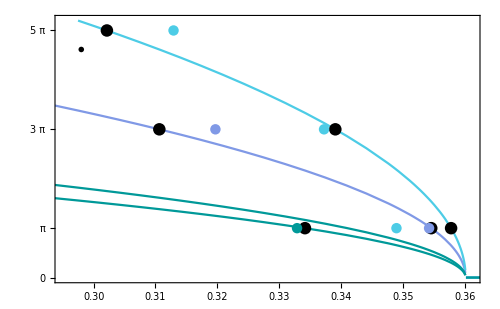

```mathematica
phase=Show[Plot[{Deltawt[w,6],Deltawt[w,13],Deltawt[w,20],Deltawt[w,7]},{w,0,1},PlotPoints->300,PlotStyle->{color1,color2,color3},PlotRange->{{Wph[0.05]-0.01,Wph[0]+0.001},{0,5.2π}},ImageSize->500,GridLinesStyle->Directive[{color1,Thickness[0.002]}],GridLines->{{},{π,3π,5π}},Evaluate@plotStyle,FrameLabel->MaTeX[{"\\omega_R^{'}","\\tau_\\text{c}(\\omega_\\text{2ul}-\\omega_\\text{2ur})"},Magnification->1.8], FrameTicks->{{{0,π,3π,5π},None},{None,None}},Epilog->{Inset[MaTeX["\\text{(a)}",Magnification->1.8],{0.298,14.5}]}],Graphics[{color1,PointSize[0.018],Point/@{{Re@wp13a,π},{Re@wp13b,3π},{Re@wp6a,π},{Re@wp20a,π},{Re@wp20b,3π},{Re@wp20c,5π}}}],Graphics[{color1,PointSize[0.015],Point[{Re@r6adn005,π}],color3,PointSize[0.015],Point[{Re@Re@r13adn005,π}],color2,PointSize[0.015],Point[{Re@r20adn005,π}],color2,PointSize[0.015],Point[{Re@r13bdn005,3π}],color3,PointSize[0.015],Point[{Re@r20bdn005,3π}],color3,PointSize[0.015],Point[{Re@r20cdn005,5π}]}]]
```

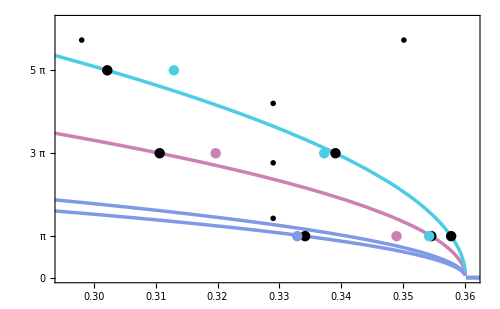

```mathematica
a=Show[Plot[{Deltawt[w,6],Deltawt[w,13],Deltawt[w,20],Deltawt[w,7]},{w,0,1},PlotRange->{{0.295,Wph[0]+0.001},{0,6.2π}},PlotPoints->300,ImageSize->500,PlotStyle->{{color2,Thickness[x]},{color4,Thickness[x]},{color3,Thickness[x]}},PlotRange->{{Wph[0.05]-0.01,Wph[0]+0.001},{0,5.2π}},GridLinesStyle->Directive[{color1,Thickness[0.002]}],GridLines->{{},{π,3π,5π}},Evaluate@plotStyle,FrameLabel->MaTeX[{"","\\tau_\\text{c}(\\omega_\\text{2ul}-\\omega_\\text{2ur})"},Magnification->1.8], FrameTicks->{{{0,π,3π,5π},None},{None,None}},Epilog->{Inset[MaTeX["\\text{(a)}",Magnification->1.8],{0.298,18}],
Inset[MaTeX["\\tau_c=13\\text{\,fs}",Magnification->1.8],{0.329,Deltawt[0.335,13]+2.}],
Inset[MaTeX["\\tau_c=6\\text{\,fs}",Magnification->1.8],{0.329,Deltawt[0.335,6]+1.4}],
Inset[MaTeX["\\delta\\text{n}_\\text{max}=0.05",Magnification->1.8],{Wph[0]-0.01,18}],Inset[MaTeX["\\tau_c=20\\text{\,fs}",Magnification->1.8],{0.329,Deltawt[0.335,20]+2.9}]}],Graphics[{color1,PointSize[0.015],Point/@{{Re@wp13a,π},{Re@wp13b,3π},{Re@wp6a,π},{Re@wp20a,π},{Re@wp20b,3π},{Re@wp20c,5π}}}],Graphics[{color2,PointSize[0.015],Point[{Re@r6adn005,π}],color4,Point[{Re@Re@r13adn005,π}],Point[{Re@r13bdn005,3π}],color3,Point[{Re@r20adn005,π}],Point[{Re@r20bdn005,3π}],Point[{Re@r20cdn005,5π}]}]]
```

### Comparando resultados con modelo simple, para δn=0.01, δn=0.05 y tc=20

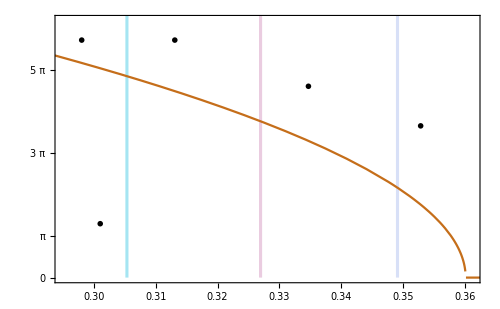

```mathematica
phase=Plot[{Deltawt[w,20]},{w,0,1},PlotStyle->{color6},PlotPoints->300,ImageSize->500,PlotRange->{{0.295,Wph[0]+0.001},{0,6.2π}},ImageSize->500,GridLinesStyle->Directive[{color1,Thickness[0.002]}],GridLines->{{},{π,3π,5π}},FrameLabel->MaTeX[{"\\omega_R^{'}(\\text{PHz})","\\tau_c(\\omega_\\text{2ul}-\\omega_\\text{2ur})"},Magnification->1.8],Evaluate@plotStyle,FrameTicks->{{{0,π,3π,5π},None},{Automatic,None}},Epilog->{
Inset[MaTeX["\\delta\\text{n}_\\text{max}\\hspace{-1mm}=\\hspace{-1mm}0.01",Magnification->1.8],{Wph[0.01]+0.004,11.5}],
Inset[MaTeX["\\delta\\text{n}_\\text{max}\\hspace{-1mm}=\\hspace{-1mm}0.03",Magnification->1.8],{Wph[0.03]+0.008,14.5}],Inset[MaTeX["\\tau_{\\text{c}}\\text{=20}\\text{\,fs}",Magnification->1.8],{0.301,1.3Pi}],Inset[MaTeX["\\delta\\text{n}_\\text{max}\\hspace{-1mm}=\\hspace{-1mm}0.05",Magnification->1.8],{Wph[0.05]+0.008,18}],Inset[MaTeX["\\text{(b)}",Magnification->1.8],{0.298,18}]},
Prolog->{Opacity[0.3,color2],Rectangle[{Wph[0.01],0},{Wph[0.01]+.0005,7π}],
Opacity[0.4,color4],Rectangle[{Wph[0.03],0},{Wph[0.03]+.0005,7π}],
Opacity[0.5,color3],Rectangle[{Wph[0.05],0},{Wph[0.05]+.0005,7π}]}]
```

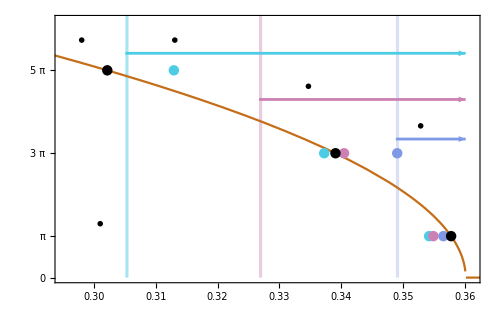

```mathematica
b=Show[phase,
Graphics[{PointSize[0.015],color3,Point[{Re@r20adn005,π}],Point[{Re@r20bdn005,3π}],Point[{Re@r20cdn005,5π}],color4,Point[{Re@r20adn003a,π}],Point[{Re@r20bdn003b,3π}],color2,Point[{Re@r20adn001,π}],PointSize[0.015],Point[{Re@r20bdn001,3π}]}],Graphics[{color1,PointSize[0.015],Point/@{{Re@wp20a,π},{Re@wp20b,3π},{Re@wp20c,5π}}}],Graphics[{Thickness[0.004],color3,Arrow[{{Wph[0.05],17},{Wph[0.0],17}}]}],
Graphics[{Thickness[0.004],color4,Arrow[{{Wph[0.03],13.5},{Wph[0.0],13.5}}]}],
Graphics[{Thickness[0.004],color2,Arrow[{{Wph[0.01],10.5},{Wph[0.0],10.5}}]}]]
```

```mathematica
s1=GraphicsGrid[{{a},{b}},Spacings->{0,-51},ImageSize->600] (*Organizar*)
```

-Graphics-

```mathematica
Export["F8.pdf",s1]
```

F8.pdf

### Comparando resultados con modelo simple, para δn=0.01, δn=0.05 y tc=13

```mathematica
fa=Plot[{Deltawt[w,13]},{w,Wph[0.01],Wph[0]},PlotStyle->{color1,Thickness[x]},PlotRange->{{0.295,Wph[0]+0.001},{0,4π}},ImageSize->500,GridLines->{{Wph[0],{Wph[0.01],color1},{Wph[0.05],color5},{Wph[0.1],color4}},{π,3π,5π}},FrameLabel->MaTeX[{"\\omega_R^{'}","\\text{13}(\\omega_\\text{2ul}-\\omega_\\text{2ur})"},Magnification->1.8],Evaluate@plotStyle,FrameTicks->{{{0,π,3π,5π},None},{Automatic,None}},Epilog->{
Inset[MaTeX["\\delta\\text{n}_\\text{max}=0.01",Magnification->1.5],{Wph[0.01],1}],Inset[MaTeX["\\delta\\text{n}_\\text{max}=0.05",Magnification->1.5],{Wph[0.05],1}],Inset[MaTeX["\\text{(b)}",Magnification->m],{0.298,12}]}];
fb=Plot[{Deltawt[w,13]},{w,Wph[0.05],Wph[0.01]},PlotStyle->{color4,Thickness[x]},PlotRange->{{0.295,Wph[0]+0.001},{0,4π}},ImageSize->500,GridLines->{{Wph[0],{Wph[0.01],color1},{Wph[0.05],color5},{Wph[0.1],color4}},{π,3π,5π}},FrameLabel->MaTeX[{"\\omega_R^{'}","\\text{13}(\\omega_\\text{2ul}-\\omega_\\text{2ur})"},Magnification->1.8],Evaluate@plotStyle,FrameTicks->{{{0,π,3π,5π},None},{Automatic,None}}];
```

```mathematica
fc=Plot[{Deltawt[w,13]},{w,0,Wph[0.05]},PlotStyle->{color2,Thickness[x]},PlotRange->{{0.295,Wph[0]+0.001},{0,4π}},ImageSize->500,GridLines->{{Wph[0],{Wph[0.01],color1},{Wph[0.05],color5},{Wph[0.1],color4}},{π,3π,5π}},FrameLabel->MaTeX[{"\\omega_R^{'}","\\text{13}(\\omega_\\text{2ul}-\\omega_\\text{2ur})"},Magnification->1.8],Evaluate@plotStyle,FrameTicks->{{{0,π,3π,5π},None},{Automatic,None}}];
```

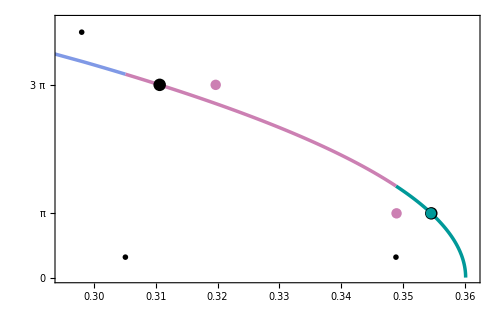

```mathematica
phase13=Show[fa,fb,fc,Plot[{},{w,0,1},PlotStyle->{color2,Thickness[x]},PlotRange->{{0.295,Wph[0]+0.001},{0,4π}},ImageSize->500,GridLines->{{Wph[0],{Wph[0.01],color1},{Wph[0.05],color5},{Wph[0.1],color4}},{π,3π,5π}},FrameLabel->MaTeX[{"\\omega_R^{'}","\\text{13}(\\omega_\\text{2ul}-\\omega_\\text{2ur})"},Magnification->1.8],Evaluate@plotStyle,FrameTicks->{{{0,π,3π,5π},None},{Automatic,None}}],Graphics[{color1,PointSize[0.018],Point/@{{Re@wp13a,π},{Re@wp13b,3π}}}],Graphics[{color1,PointSize[0.015],Point[{Re@r13adn001,π}],color4,PointSize[0.015],Point[{Re@r13bdn005,3π}],color4,PointSize[0.015],Point[{Re@r13adn005,π}]}]]
```

### Comparando resultados con modelo simple, para δn=0.01, δn=0.05 y tc=6,13

```mathematica
fa13=Plot[{Deltawt[w,13]},{w,Wph[0.01],Wph[0]},PlotStyle->{color1,Thickness[x]},PlotRange->{{Wph[0.05]-0.01,Wph[0]+0.001},{0,4π}},ImageSize->530,GridLines->{{Wph[0],{Wph[0.01],color1},{Wph[0.05],color5},{Wph[0.1],color4}},{π,3π,5π}},FrameLabel->MaTeX[{"\\omega_R^{'}","\\tau_c(\\omega_\\text{2ul}-\\omega_\\text{2ur})"},Magnification->1.8],Evaluate@plotStyle,FrameTicks->{{{0,π,3π,5π},None},{Automatic,None}},Epilog->{
Inset[MaTeX["\\delta\\text{n}_\\text{max}=0.01",Magnification->1.8],{Wph[0.01]+0.001,11}],Inset[MaTeX["\\delta\\text{n}_\\text{max}=0.05",Magnification->1.8],{Wph[0.05]+0.001,11}],
Inset[MaTeX["\\tau_c=13",Magnification->1.8],{0.328,Deltawt[0.335,13]+2.1}],
Inset[MaTeX["\\tau_c=6",Magnification->1.8],{0.328,Deltawt[0.335,6]+1.2}],
Inset[MaTeX["\\text{(b)}",Magnification->1.8],{0.298,12}]}];
fb13=Plot[{Deltawt[w,13]},{w,Wph[0.05],Wph[0.01]},PlotStyle->{color4,Thickness[x]},PlotRange->{{0.295,Wph[0]+0.001},{0,4π}}];
fc13=Plot[{Deltawt[w,13]},{w,0,Wph[0.05]},PlotStyle->{color2,Thickness[x]},PlotRange->{{0.295,Wph[0]+0.001},{0,4π}}];
```

```mathematica
fa6=Plot[{Deltawt[w,6]},{w,Wph[0.01],Wph[0]},PlotStyle->{color1,Thickness[x]},PlotRange->{{0.295,Wph[0]+0.001},{0,4π}}];
fb6=Plot[{Deltawt[w,6]},{w,Wph[0.05],Wph[0.01]},PlotStyle->{color4,Thickness[x]},PlotRange->{{0.295,Wph[0]+0.001},{0,4π}}];
fc6=Plot[{Deltawt[w,6]},{w,0,Wph[0.05]},PlotStyle->{color2,Thickness[x]},PlotRange->{{0.295,Wph[0]+0.001},{0,4π}}];
```

```mathematica
phase6and13=Show[fa13,fb13,fc13,fa6,fb6,fc6,Plot[{},{w,0,1},PlotStyle->{color2,Thickness[x]},PlotRange->{{0.295,Wph[0]+0.001},{0,4π}},ImageSize->600,GridLines->{{Wph[0],{Wph[0.01],color1},{Wph[0.05],color5},{Wph[0.1],color4}},{π,3π,5π}},FrameLabel->MaTeX[{"\\omega_R^{'}","\\text{13}(\\omega_\\text{2ul}-\\omega_\\text{2ur})"},Magnification->1.8],Evaluate@plotStyle,FrameTicks->{{{0,π,3π,5π},None},{Automatic,None}}],Graphics[{color1,PointSize[0.018],Point/@{{Re@wp6a,π},{Re@wp13a,π},{Re@wp13b,3π}}}],Graphics[{color1,PointSize[0.015],Point[{Re@r6adn001,π}],color4,PointSize[0.015],Point[{Re@r6adn005,π}],color4,PointSize[0.015],Point[{Re@r13bdn005,3π}],color1,PointSize[0.015],Point[{Re@r13adn001,π}]}]];
```

```mathematica
Export["F8.pdf",s1]
```

F8.pdf

### Parametric space dn vs tc

```mathematica
mi=2;
```

```mathematica
raiz1=Abs@Table[{tc,FindRoot[Deltawt[w,tc]==π,{w,(*tc/20 Wph[0]*)Wph[0]}]⟦1,2⟧},{tc,0.1,80,0.1}];
raiz3=Abs@Table[{tc,FindRoot[Deltawt[w,tc]==3π,{w,(*tc/20 Wph[0]*)Wph[0]}]⟦1,2⟧},{tc,0.1,80,0.1}];
raiz5=Abs@Table[{tc,FindRoot[Deltawt[w,tc]==5π,{w,(*tc/20 Wph[0]*)Wph[0]}]⟦1,2⟧},{tc,0.1,80,0.1}];
raiz7=Abs@Table[{tc,FindRoot[Deltawt[w,tc]==7π,{w,(*tc/20 Wph[0]*)Wph[0]}]⟦1,2⟧},{tc,0.1,80,0.1}];
raiz9=Abs@Table[{tc,FindRoot[Deltawt[w,tc]==9π,{w,(*tc/20 Wph[0]*)Wph[0]}]⟦1,2⟧},{tc,0.1,80,0.1}];
raiz11=Abs@Table[{tc,FindRoot[Deltawt[w,tc]==11π,{w,(*tc/20 Wph[0]*)Wph[0]}]⟦1,2⟧},{tc,0.1,80,0.1}];
raiz13=Abs@Table[{tc,FindRoot[Deltawt[w,tc]==13π,{w,(*tc/20 Wph[0]*)Wph[0]}]⟦1,2⟧},{tc,0.1,80,0.1}];
raiz15=Abs@Table[{tc,FindRoot[Deltawt[w,tc]==15π,{w,(*tc/20 Wph[0]*)Wph[0]}]⟦1,2⟧},{tc,0.1,80,0.1}];
raiz17=Abs@Table[{tc,FindRoot[Deltawt[w,tc]==17π,{w,(*tc/20 Wph[0]*)Wph[0]}]⟦1,2⟧},{tc,0.1,80,0.1}];
raiz19=Abs@Table[{tc,FindRoot[Deltawt[w,tc]==19π,{w,(*tc/20 Wph[0]*)Wph[0]}]⟦1,2⟧},{tc,0.1,80,0.1}];
raiz21=Abs@Table[{tc,FindRoot[Deltawt[w,tc]==21π,{w,(*tc/20 Wph[0]*)Wph[0]}]⟦1,2⟧},{tc,0.1,80,0.1}];
raiz23=Abs@Table[{tc,FindRoot[Deltawt[w,tc]==23π,{w,(*tc/20 Wph[0]*)Wph[0]}]⟦1,2⟧},{tc,0.1,80,0.1}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

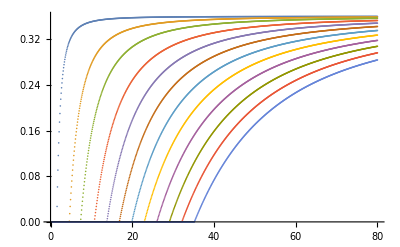

```mathematica
ListPlot[{raiz1,raiz3,raiz5,raiz7,raiz9,raiz11,raiz13,raiz15,raiz17,raiz19,raiz21,raiz23}]
```

```mathematica
q=270 Ω0n^2/w00^2+729 Ω0n^4/w00^4+(3^(3/2)Ω0n)/w00 √((27 Ω0n^2/(w00)^2-4)^3)-2;
```

```mathematica
dnmin1=ng0-√(1+w00^2/(3Ω0n^2)(q^(1/3)/2^(1/3)-1)+2^(1/3)/(3 q^(1/3))(w00^2/Ω0n^2+54))/.{Ω0n->Ω0,w00->raiz1⟦All,2⟧};
dnmin3=ng0-√(1+w00^2/(3Ω0n^2)(q^(1/3)/2^(1/3)-1)+2^(1/3)/(3 q^(1/3))(w00^2/Ω0n^2+54))/.{Ω0n->Ω0,w00->raiz3⟦All,2⟧};
dnmin5=ng0-√(1+w00^2/(3Ω0n^2)(q^(1/3)/2^(1/3)-1)+2^(1/3)/(3 q^(1/3))(w00^2/Ω0n^2+54))/.{Ω0n->Ω0,w00->raiz5⟦All,2⟧};
dnmin7=ng0-√(1+w00^2/(3Ω0n^2)(q^(1/3)/2^(1/3)-1)+2^(1/3)/(3 q^(1/3))(w00^2/Ω0n^2+54))/.{Ω0n->Ω0,w00->raiz7⟦All,2⟧};
dnmin9=ng0-√(1+w00^2/(3Ω0n^2)(q^(1/3)/2^(1/3)-1)+2^(1/3)/(3 q^(1/3))(w00^2/Ω0n^2+54))/.{Ω0n->Ω0,w00->raiz9⟦All,2⟧};
dnmin11=ng0-√(1+w00^2/(3Ω0n^2)(q^(1/3)/2^(1/3)-1)+2^(1/3)/(3 q^(1/3))(w00^2/Ω0n^2+54))/.{Ω0n->Ω0,w00->raiz11⟦All,2⟧};
dnmin13=ng0-√(1+w00^2/(3Ω0n^2)(q^(1/3)/2^(1/3)-1)+2^(1/3)/(3 q^(1/3))(w00^2/Ω0n^2+54))/.{Ω0n->Ω0,w00->raiz13⟦All,2⟧};
dnmin15=ng0-√(1+w00^2/(3Ω0n^2)(q^(1/3)/2^(1/3)-1)+2^(1/3)/(3 q^(1/3))(w00^2/Ω0n^2+54))/.{Ω0n->Ω0,w00->raiz15⟦All,2⟧};dnmin17=ng0-√(1+w00^2/(3Ω0n^2)(q^(1/3)/2^(1/3)-1)+2^(1/3)/(3 q^(1/3))(w00^2/Ω0n^2+54))/.{Ω0n->Ω0,w00->raiz17⟦All,2⟧};dnmin19=ng0-√(1+w00^2/(3Ω0n^2)(q^(1/3)/2^(1/3)-1)+2^(1/3)/(3 q^(1/3))(w00^2/Ω0n^2+54))/.{Ω0n->Ω0,w00->raiz19⟦All,2⟧};dnmin21=ng0-√(1+w00^2/(3Ω0n^2)(q^(1/3)/2^(1/3)-1)+2^(1/3)/(3 q^(1/3))(w00^2/Ω0n^2+54))/.{Ω0n->Ω0,w00->raiz21⟦All,2⟧};
dnmin23=ng0-√(1+w00^2/(3Ω0n^2)(q^(1/3)/2^(1/3)-1)+2^(1/3)/(3 q^(1/3))(w00^2/Ω0n^2+54))/.{Ω0n->Ω0,w00->raiz23⟦All,2⟧};
```

```mathematica
cl=color1
```

RGBColor[0, 0.6, 0.6]

```mathematica
col12
```

RGBColor[0, 0.625, 0.578, 0.6]

```mathematica
r=0.004;yf=0.15;xf=22;
```

```mathematica
dntc1=ListLinePlot[{{raiz1⟦All,1⟧,dnmin1}ᵀ,{raiz3⟦All,1⟧,dnmin3}ᵀ},PlotRange->{{0,xf},{0,yf}},PlotStyle->{{color1,Thickness[r]},{color1,Thickness[r]}},Filling->{1->{2}},FillingStyle->{Opacity[0.9,col12]},FillingStyle->{Opacity[0.7,col14]},FrameLabel->MaTeX[{"\\tau_{\\text{c}}(\\text fs)","\\delta \\text{n}_{\\text{max}}"},Magnification->1.8]];

dntc2=ListLinePlot[{{raiz3⟦All,1⟧,dnmin3}ᵀ,{raiz5⟦All,1⟧,dnmin5}ᵀ},PlotRange->{{0,xf},{0,yf}},PlotStyle->{{color1,Thickness[r]},{color1,Thickness[r]}},Filling->{1->{2}},FillingStyle->{Opacity[0.7,col12]},FrameLabel->MaTeX[{"\\tau_{\\text{c}}(\\text fs)","\\delta \\text{n}_{\\text{max}}"},Magnification->1.8]];
dntc3=ListLinePlot[{{raiz5⟦All,1⟧,dnmin5}ᵀ,{raiz7⟦All,1⟧,dnmin7}ᵀ},PlotRange->{{0,xf},{0,yf}},PlotStyle->{{color1,Thickness[r]},{color1,Thickness[r]}},Filling->{1->{2}},FillingStyle->{Opacity[0.5,col12]},FillingStyle->{Opacity[0.2,col14]},FrameLabel->MaTeX[{"\\tau_{\\text{c}}(\\text fs)","\\delta \\text{n}_{\\text{max}}"},Magnification->1.8]];
dntc4=ListLinePlot[{{raiz7⟦All,1⟧,dnmin7}ᵀ,{raiz9⟦All,1⟧,dnmin9}ᵀ},PlotRange->{{0,xf},{0,yf}},PlotStyle->{{color1,Thickness[r]},{color1,Thickness[r]}},Filling->{1->{2}},FillingStyle->{Opacity[0.3,col12]},FillingStyle->{Opacity[0.2,col14]},FrameLabel->MaTeX[{"\\tau_{\\text{c}}(\\text fs)","\\delta \\text{n}_{\\text{max}}"},Magnification->1.8]];
dntc5=ListLinePlot[{{raiz9⟦All,1⟧,dnmin9}ᵀ,{raiz11⟦All,1⟧,dnmin11}ᵀ},PlotRange->{0,0.2},PlotStyle->{{color1,Thickness[r]},{color1,Thickness[r]}},Filling->{1->{2}},FillingStyle->{Opacity[0.1,col12]},FillingStyle->{Opacity[0.2,col14]},FrameLabel->MaTeX[{"\\tau_{\\text{c}}(\\text fs)","\\delta \\text{n}_{\\text{max}}"},Magnification->1.8]];
dntc5=ListLinePlot[{{raiz11⟦All,1⟧,dnmin9}ᵀ,{raiz13⟦All,1⟧,dnmin13}ᵀ},PlotRange->{{0,xf},{0,yf}},PlotStyle->{{color1,Thickness[r]},{color1,Thickness[r]}},Filling->{1->{2}},FillingStyle->{Opacity[0.1,col12]},FillingStyle->{Opacity[0.2,col14]},FrameLabel->MaTeX[{"\\tau_{\\text{c}}(\\text fs)","\\delta \\text{n}_{\\text{max}}"},Magnification->1.8]];
dntc1=ListLinePlot[{{raiz1⟦All,1⟧,dnmin1}ᵀ,{raiz3⟦All,1⟧,dnmin3}ᵀ},PlotRange->{{0,xf},{0,yf}},PlotStyle->{{color1,Thickness[r]},{color1,Thin}},Filling->{1->{2}},FillingStyle->{Opacity[0.25,cl]},FillingStyle->{Opacity[0.7,col14]},FrameLabel->MaTeX[{"\\tau_{\\text{c}}(\\text fs)","\\delta \\text{n}_{\\text{max}}"},Magnification->1.8]];

dntc2=ListLinePlot[{{raiz3⟦All,1⟧,dnmin3}ᵀ,{raiz5⟦All,1⟧,dnmin5}ᵀ},PlotRange->{{0,xf},{0,yf}},PlotStyle->{{color1,Thickness[r]},{color1,Thickness[r]}},Filling->{1->{2}},FillingStyle->{Opacity[0.35,cl]},FrameLabel->MaTeX[{"\\tau_{\\text{c}}(\\text fs)","\\delta \\text{n}_{\\text{max}}"},Magnification->1.8]];
dntc3=ListLinePlot[{{raiz5⟦All,1⟧,dnmin5}ᵀ,{raiz7⟦All,1⟧,dnmin7}ᵀ},PlotRange->{{0,0.2},{0,24}},PlotStyle->{{color1,Thickness[r]},{color1,Thickness[r]}},Filling->{1->{2}},FillingStyle->{Opacity[0.5,cl]},FillingStyle->{Opacity[0.2,col14]},FrameLabel->MaTeX[{"\\tau_{\\text{c}}(\\text fs)","\\delta \\text{n}_{\\text{max}}"},Magnification->1.8]];
dntc4=ListLinePlot[{{raiz7⟦All,1⟧,dnmin7}ᵀ,{raiz9⟦All,1⟧,dnmin9}ᵀ},PlotRange->{{0,xf},{0,yf}},PlotStyle->{{color1,Thickness[r]},{color1,Thickness[r]}},Filling->{1->{2}},FillingStyle->{Opacity[0.7,cl]},FillingStyle->{Opacity[0.2,col14]},FrameLabel->MaTeX[{"\\tau_{\\text{c}}(\\text fs)","\\delta \\text{n}_{\\text{max}}"},Magnification->1.8]];
dntc5=ListLinePlot[{{raiz9⟦All,1⟧,dnmin9}ᵀ,{raiz11⟦All,1⟧,dnmin11}ᵀ},PlotRange->{{0,xf},{0,yf}},PlotStyle->{{color1,Thickness[r]},{color1,Thickness[r]}},Filling->{1->{2}},FillingStyle->{Opacity[0.9,cl]},FillingStyle->{Opacity[0.2,col14]},FrameLabel->MaTeX[{"\\tau_{\\text{c}}(\\text fs)","\\delta \\text{n}_{\\text{max}}"},Magnification->1.8]];
dntc6=ListLinePlot[{{raiz11⟦All,1⟧,dnmin11}ᵀ,{raiz13⟦All,1⟧,dnmin13}ᵀ},PlotRange->{{0,xf},{0,yf}},PlotStyle->{{color1,Thickness[r]},{color1,Thickness[r]}},Filling->{1->{2}},FillingStyle->{Opacity[1,cl]},FillingStyle->{Opacity[0.2,col14]},FrameLabel->MaTeX[{"\\tau_{\\text{c}}(\\text fs)","\\delta \\text{n}_{\\text{max}}"},Magnification->1.8]];
```

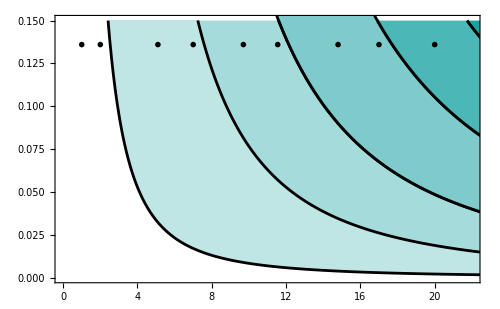

```mathematica
dntcn=Show[dntc1,dntc2,dntc3,dntc4,dntc5,dntc6,Evaluate@plotStyle,ImageSize->500,Epilog->{
Inset[MaTeX["\\text{0}",Magnification->mi],{1.,0.008*17}],Inset[MaTeX["\\text{1}",Magnification->mi],{5.1,0.008*17}],Inset[MaTeX["\\text{2}",Magnification->mi],{9.7,0.008*17}],Inset[MaTeX["\\text{3}",Magnification->mi],{14.8,0.008*17}],Inset[MaTeX["\\text{4}",Magnification->mi],{20.,0.008*17}],Inset[MaTeX["\\text{V}'_0",Magnification->mi*0.6],{2.,0.008*17}],Inset[MaTeX["\\text{V}'_1",Magnification->mi*0.6],{7,0.008*17}],Inset[MaTeX["\\text{V}'_2",Magnification->mi*0.6],{11.55,0.008*17}],Inset[MaTeX["\\text{V}'_3",Magnification->mi*0.6],{17.,0.008*17}](*,Inset[MaTeX["\\text{1}",Magnification->mi2],{5.5,0.01}],Inset[MaTeX["\\text{1}",Magnification->mi2],{5.5,0.05}],Inset[MaTeX["\\text{1}",Magnification->mi2],{13.5,0.01}],Inset[MaTeX["\\text{2}",Magnification->mi2],{13.5,0.05}],Inset[MaTeX["\\text{2}",Magnification->mi2],{20.5,0.01}],Inset[MaTeX["\\text{3}",Magnification->mi2],{20.5,0.05}]*)}]
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts}"}]
MaTeX["\\color{red}\\sqrt{x}"]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{color,txfonts}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

-Graphics-

```mathematica
dntcn=Show[dntc1,dntc2,dntc3,dntc4,dntc5,dntc6,Evaluate@plotStyle,ImageSize->500,Epilog->{
Inset[MaTeX["\\text{0}",Magnification->mi],{1.,0.008*17}],Inset[MaTeX["\\text{1}",Magnification->mi],{5.1,0.008*17}],Inset[MaTeX["\\text{2}",Magnification->mi],{9.7,0.008*17}],Inset[MaTeX["\\text{3}",Magnification->mi],{14.8,0.008*17}],Inset[MaTeX["\\text{4}",Magnification->mi],{20.,0.008*17}],Inset[MaTeX["\\color{red}\\text{V}'_0",Magnification->mi*0.7],{2.,0.008*17}],Inset[MaTeX["\\color{red}\\text{V}'_1",Magnification->mi*0.7],{7,0.008*17}],Inset[MaTeX["\\color{red}\\text{V}'_2",Magnification->mi*0.7],{11.55,0.008*17}],Inset[MaTeX["\\color{red}\\text{V}'_3",Magnification->mi*0.7],{17.,0.008*17}](*,Inset[MaTeX["\\text{1}",Magnification->mi2],{5.5,0.01}],Inset[MaTeX["\\text{1}",Magnification->mi2],{5.5,0.05}],Inset[MaTeX["\\text{1}",Magnification->mi2],{13.5,0.01}],Inset[MaTeX["\\text{2}",Magnification->mi2],{13.5,0.05}],Inset[MaTeX["\\text{2}",Magnification->mi2],{20.5,0.01}],Inset[MaTeX["\\text{3}",Magnification->mi2],{20.5,0.05}]*)}]
```

-Graphics-

```mathematica
dnf[t_,v0_]=v0/(0.5 Wph[0] t^2);
```

```mathematica
dnf[10,.02]
```

0.0011106

```mathematica
Wph[0]
```

0.360165

```mathematica
data01={raiz1⟦All,1⟧,dnmin1}ᵀ;
data03={raiz3⟦All,1⟧,dnmin3}ᵀ;
data05={raiz5⟦All,1⟧,dnmin5}ᵀ;
data07={raiz7⟦All,1⟧,dnmin7}ᵀ;
data09={raiz9⟦All,1⟧,dnmin9}ᵀ;
data011={raiz11⟦All,1⟧,dnmin11}ᵀ;
data013={raiz11⟦All,1⟧,dnmin13}ᵀ;
data015={raiz11⟦All,1⟧,dnmin15}ᵀ;
data017={raiz11⟦All,1⟧,dnmin17}ᵀ;
data019={raiz11⟦All,1⟧,dnmin19}ᵀ;
data021={raiz11⟦All,1⟧,dnmin21}ᵀ;data023={raiz11⟦All,1⟧,dnmin23}ᵀ;
```

```mathematica
data1=Take[data01,-780];
data3=Take[data03,-737];
data5=Take[data05,-700];
data7=Take[data07,-653];
data9=Take[data09,-612];
data11=Take[data011,-570];
data13=Take[data013,-525];
data15=Take[data015,-485];
data17=Take[data017,-441];
data19=Take[data019,-400];
data21=Take[data021,-359];
data23=Take[data023,-312];
```

```mathematica
v01=FindFit[data1,dnf[t,v0],v0,t][[1,2]];
v03=FindFit[data3,dnf[t,v0],v0,t][[1,2]];
v05=FindFit[data5,dnf[t,v0],v0,t][[1,2]];
v07=FindFit[data7,dnf[t,v0],v0,t][[1,2]];
v09=FindFit[data9,dnf[t,v0],v0,t][[1,2]];
v011=FindFit[data11,dnf[t,v0],v0,t][[1,2]];
v013=FindFit[data13,dnf[t,v0],v0,t][[1,2]];
v015=FindFit[data15,dnf[t,v0],v0,t][[1,2]];
v017=FindFit[data19,dnf[t,v0],v0,t][[1,2]];
v021=FindFit[data21,dnf[t,v0],v0,t][[1,2]];
v023=FindFit[data23,dnf[t,v0],v0,t][[1,2]];




{v01,v03,v05,v07,v09,v011}
```

{0.156369,1.4025,3.59486,7.64138,12.6435,18.8944}

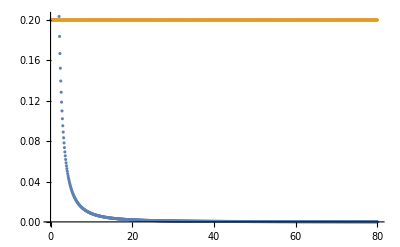

```mathematica
ListPlot[{Take[data01,-780],Table[{k,0.2},{k,0,80,0.1}]},PlotRange->All]
```

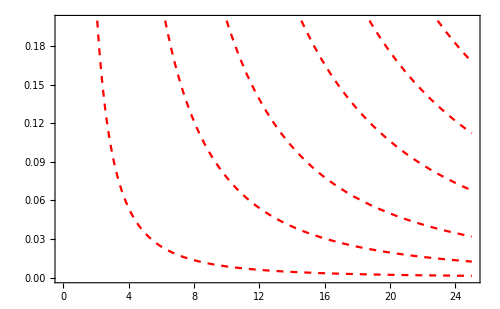

```mathematica
vn=Plot[{dnf[t,v01],dnf[t,v03],dnf[t,v05],dnf[t,v07],dnf[t,v09],dnf[t,v011]},{t,0,25},PlotRange->{{0,25},{0,0.2}},Evaluate@plotStyle,PlotStyle->{{Red,Dashed}},ImageSize->500]
```

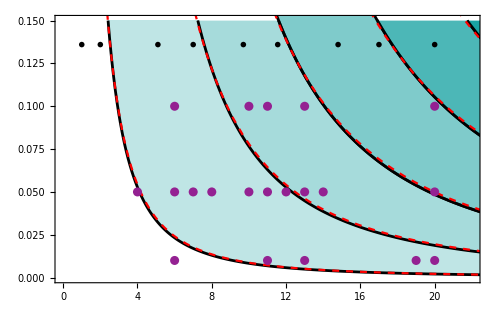

```mathematica
Show[dntcn,vn,
Graphics[{col21,PointSize[0.013],Point[{6,0.01}],Point[{6,0.05}],Point[{13,0.05}],Point[{4,0.05}],Point[{7,0.05}],Point[{8,0.05}],Point[{11,0.05}],Point[{12,0.05}],Point[{14,0.05}],Point[{11,0.01}],Point[{10,0.1}],Point[{11,0.1}],Point[{20,0.01}],Point[{20,0.05}],Point[{13,0.01}],Point[{6,0.1}],Point[{10,0.05}],Point[{13,0.1}],Point[{19,0.01}],Point[{20,0.1}]}]]
```

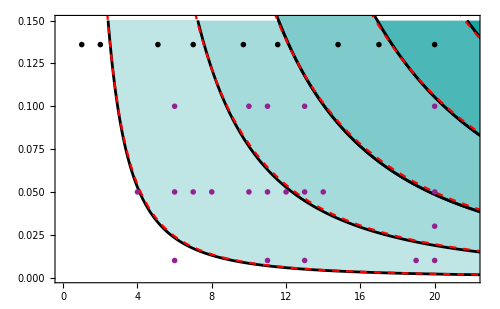

```mathematica
parspace=Show[dntcn,vn,
ListPlot[{{
{6,0.01},{6,0.05},{4,0.05},{7,0.05},{8,0.05},{11,0.01},{13,0.01},{6,0.1},{10,0.05},{19,0.01}},
{{10,0.1},{11,0.1},{13,0.1},{11,0.05},{20,.03},{12,0.05},{13,0.05},{14,0.05},{20,0.01}},
{{20,0.05},{20,0.1}} },PlotMarkers->{{"1",15},{"2",15},{"3",15}},PlotStyle->col21]]
```

```mathematica
Export["parspace.pdf",parspace]
```

parspace.pdf

### New V parameter

```mathematica
dnf2[t_,v0_]=v0^2/(2 (1.1711717962840988) (Wph[0])^2 t^2);
```

```mathematica
dnf2[4,.483445]
```

0.0480752

```mathematica
β[whor[0],0]SOL/whor[0]
```

1.17117

```mathematica
v012=FindFit[data1,dnf2[t,v0],v0,t]⟦1,2⟧;
v032=FindFit[data3,dnf2[t,v0],v0,t]⟦1,2⟧;
v052=FindFit[data5,dnf2[t,v0],v0,t]⟦1,2⟧;
v072=FindFit[data7,dnf2[t,v0],v0,t]⟦1,2⟧;
v092=FindFit[data9,dnf2[t,v0],v0,t]⟦1,2⟧;
v0112=FindFit[data11,dnf2[t,v0],v0,t]⟦1,2⟧;
v0113=FindFit[data13,dnf2[t,v0],v0,t]⟦1,2⟧;
v0115=FindFit[data15,dnf2[t,v0],v0,t]⟦1,2⟧;
v0117=FindFit[data17,dnf2[t,v0],v0,t]⟦1,2⟧;
v0119=FindFit[data19,dnf2[t,v0],v0,t]⟦1,2⟧;
v0121=FindFit[data21,dnf2[t,v0],v0,t]⟦1,2⟧;
v0123=FindFit[data11,dnf2[t,v0],v0,t]⟦1,2⟧;
{v012,v032,v052,v072,v092,v0112}/v012
```

{1.,2.99485,4.79474,6.99053,8.99204,10.9924}

```mathematica
Ajuste13puntos
```

Ajuste13puntos

```mathematica
dat={{1,2,3,4,5,6,7,8,9,10,11,12},{v012,v032,v052,v072,v092,v0112,v0113,v0115,v0117,v0119,v0121,v0123}}ᵀ;
```

```mathematica
model=FindFit[dat,m2 xx +b3,{m2,b3},xx]
```

{m2→0.793669,b3→0.482572}

```mathematica
m2 xx +b3/.model
```

0.482572+0.793669 xx

```mathematica
m2 {1,2,3,4,5,6} +b3/.model
{v012,v032,v052,v072,v092,v0112}
```

{1.27624,2.06991,2.86358,3.65725,4.45091,5.24458}

{0.513649,1.53831,2.46282,3.59068,4.61875,5.64622}

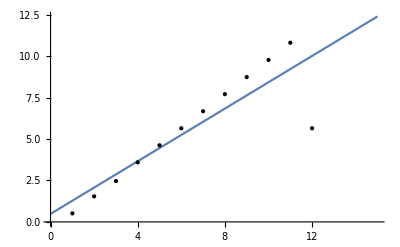

```mathematica
Plot[m2 xx +b3/.model,{xx,0,15},Epilog->{PointSize->0.02,Point/@dat}]
```

```mathematica
Ajuste11 puntos
```

Ajuste11 puntos

```mathematica
dat0={{1,2,3,4,5,6,7,8,9,10,11},{v012,v032,v052,v072,v092,v0112,v0113,v0115,v0117,v0119,v0121}}ᵀ;
```

```mathematica
model0=FindFit[dat0,m0 xx +b0,{m0,b0},xx]
```

{m0→1.03151,b0→-0.548063}

```mathematica
f[m_]:=1.03151(m+1)-0.548063
g[m_]:=1.03151m-0.548063
f[2]
```

2.54647

```mathematica
m0 {1,2,3,4,5,6,7,8,9,10,11} +b0/.model0
{v012,v032,v052,v072,v092,v0112,v0113,v0115,v0117,v0119,v0121}
```

{0.483445,1.51495,2.54646,3.57797,4.60947,5.64098,6.67249,7.704,8.7355,9.76701,10.7985}

{0.513649,1.53831,2.46282,3.59068,4.61875,5.64622,6.67083,7.70331,8.73248,9.7678,10.806}

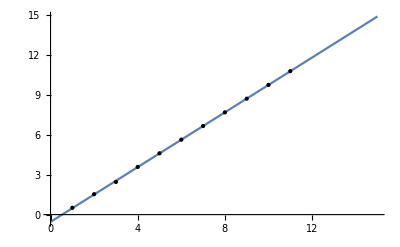

```mathematica
Plot[{m0 xx +b0/.model0},{xx,0,15},Epilog->{PointSize->0.02,Point/@dat0}]
```

```mathematica
Ajuste6 puntos
```

Ajuste6 puntos

```mathematica
dat6={{1,2,3,4,5,6},{v012,v032,v052,v072,v092,v0112}}ᵀ;
```

```mathematica
model6=FindFit[dat6,m6 xx +b6,{m6,b6},xx]
```

{m6→1.02949,b6→-0.541468}

```mathematica
m6 {1,2,3,4,5,6} +b6/.model6
{v012,v032,v052,v072,v092,v0112}
```

{0.488019,1.51751,2.54699,3.57648,4.60597,5.63546}

{0.513649,1.53831,2.46282,3.59068,4.61875,5.64622}

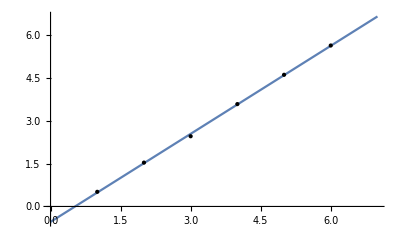

```mathematica
Plot[m6 xx +b6/.model6,{xx,0,7},Epilog->{PointSize->0.02,Point/@dat6}]
```

## Particular solution

### Plot the solution ψ τ_c=6, δn=0.01,a (B)

```mathematica
r6a001=0.35110872+I 1.648*^-6;
```

```mathematica
wTest=0.35110872+I 1.648*^-6
tc
```

0.351109+1.648×10^-6 ⅈ

6

Calculo de las amplitudes en la región I dadas c1=1 y c2=ρ.  (Recordar que a1=a2=0)

```mathematica
a1t=a1/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a2t=a2/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a3t=a3/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a4t=a4/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
```

0.0000500774-0.000596577 ⅈ

-1.11022×10^-16+0. ⅈ

-415.266-397.433 ⅈ

-9.0882+5.25622 ⅈ

```mathematica
c1t=1
c2t=rho4[Re[wTest],Im[wTest]]
c3t=0
c4t=0
```

1

-503.491-277.278 ⅈ

0

0

w11 (ω_(1u))⟶ Im<0.  a1=0. Decae en la región III. c1=1
w12 (ω_(1ur))⟶ Im<0. a2=0. Decae en la región III. c2=ρ
w13 (ω_(1ul))⟶ Im>0. a3=Free. Decae en la regiónIII. c3=0
w14 (ω_(1v))⟶ Im>0. a4=Free. Decae en la regiónIII. c3=0
w21 (ω_(2u))⟶  Estado confinado
w22 (ω_(2ur))⟶ Estado confinado 
w23 (ω_(2ul))⟶  Estado confinado 
w24 (ω_(2v))⟶  Estado confinado

```mathematica
{w11[Re[wTest],Im[wTest]],w12[Re[wTest],Im[wTest]],w13[Re[wTest],Im[wTest]],w14[Re[wTest],Im[wTest]]}
{w21[Re[wTest],Im[wTest]],w22[Re[wTest],Im[wTest]],w23[Re[wTest],Im[wTest]],w24[Re[wTest],Im[wTest]]}
```

{-2.38622-1.42359×10^-6 ⅈ,1.12239-0.0766649 ⅈ,1.12234+0.0766656 ⅈ,0.140368+6.57358×10^-7 ⅈ}

{-2.40683-1.41047×10^-6 ⅈ,1.28718-0.0000136879 ⅈ,0.978715+0.0000144384 ⅈ,0.140931+6.59973×10^-7 ⅈ}

Calculo de las amplitudes en la región I. 
Forma1:ψ_I=ψ_I
Forma 2:  ψ_I=(Jump^-1.P_L.Jump)ψ_III

```mathematica
amp1t={0a1t , 0a2t,a3t,a4t};
ψ1t[τ_]=(amp1t.solsub/.wrule[Re[wTest],Im[wTest]])
amp1t2=ijump.propaL.jump.{c1t,c2t,c3t,c4t};
ψ1t2[τ_]=Chop[amp1t2.solsub/.wrule[Re[wTest],Im[wTest]]]
```

(0.+0. ⅈ)-(9.0882-5.25622 ⅈ) ⅇ^((6.57358×10^-7-0.140368 ⅈ) τ)-(415.266+397.433 ⅈ) ⅇ^((0.0766656-1.12234 ⅈ) τ)

(0.0000500774-0.000596577 ⅈ) ⅇ^((-1.42359×10^-6+2.38622 ⅈ) τ)-(9.0882-5.25622 ⅈ) ⅇ^((6.57358×10^-7-0.140368 ⅈ) τ)-(415.266+397.433 ⅈ) ⅇ^((0.0766656-1.12234 ⅈ) τ)

Calculo de las amplitudes en la región II. 
Forma1: ψ_II=(P_L.Jump)ψ_III
Forma 2: ψ_II=(Jump)ψ_I

```mathematica
amp2t=jump.{0a1t ,0a2t,a3t,a4t}//Simplify;
amp2t2=propaL.jump.{c1t, c2t,c3t,c4t};
ψ2t[τ_]=amp2t.solsup/.wrule[Re[wTest],Im[wTest]]
ψ2t2[τ_]=amp2t2.solsup/.wrule[Re[wTest],Im[wTest]]
```

(-53.6807-243.09 ⅈ) ⅇ^((-0.0000136879-1.28718 ⅈ) τ)-(0.328403+0.410417 ⅈ) ⅇ^((-1.41047×10^-6+2.40683 ⅈ) τ)+(7.28597+23.5399 ⅈ) ⅇ^((6.59973×10^-7-0.140931 ⅈ) τ)-(377.631+172.216 ⅈ) ⅇ^((0.0000144384-0.978715 ⅈ) τ)

(-53.6807-243.09 ⅈ) ⅇ^((-0.0000136879-1.28718 ⅈ) τ)-(0.328354+0.411002 ⅈ) ⅇ^((-1.41047×10^-6+2.40683 ⅈ) τ)+(7.28598+23.5398 ⅈ) ⅇ^((6.59973×10^-7-0.140931 ⅈ) τ)-(377.631+172.216 ⅈ) ⅇ^((0.0000144384-0.978715 ⅈ) τ)

```mathematica
Abs[ψ1t[0]]
Abs[ψ2t[0]]
Abs[ψ1t2[0]]
Abs[ψ2t2[0]]
```

577.822

577.822

577.823

577.823

La funciones en la región III, estaran desfasadas debido al salto entre la región II y III en una cantidad tc. Esto se corrige con el cambio ψ_III(τ)⟶ψ_III(τ-tc) o teniendo en cuenta dicha fase.  ψ_III=(Jump^-1.P_L1.P_R.Jump)ψ_I

```mathematica
propaR1=DiagonalMatrix[{Exp[-I w1sub tc],Exp[-I w2sub tc],Exp[-I w3sub tc],Exp[-I w4sub tc]}];
propaL1=DiagonalMatrix[{Exp[I w1sub tc],Exp[I w2sub tc],Exp[I w3sub tc],Exp[I w4sub tc]}];
```

```mathematica
amp3t=Simplify[propaL1.ijump.propaR.amp2t]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t[τ_]=amp3t.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
amp3t2=Simplify[propaL1.{c1t,c2t,c3t,c4t}]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t2[τ_]=amp3t2.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
```

(-526.247-743.022 ⅈ) ⅇ^((-0.0766649-1.12239 ⅈ) τ)-(0.17933+0.983234 ⅈ) ⅇ^((-1.42359×10^-6+2.38622 ⅈ) τ)+(0.0000221529+0.000122366 ⅈ) ⅇ^((6.57358×10^-7-0.140368 ⅈ) τ)+(0.000213803-0.000112241 ⅈ) ⅇ^((0.0766656-1.12234 ⅈ) τ)

(-526.247-743.022 ⅈ) ⅇ^((-0.0766649-1.12239 ⅈ) τ)-(0.179206+0.98382 ⅈ) ⅇ^((-1.42359×10^-6+2.38622 ⅈ) τ)

```mathematica
Abs[ψ2t[tc]]
Abs[ψ2t2[tc]]
Abs[ψ3t[tc]]
Abs[ψ3t2[tc]]
```

573.917

573.917

573.917

«1 more identical outputs»

```mathematica
ψ[τ_]:=Piecewise[{{ψ3t[τ],τ≥tc},{ψ2t[τ],0<τ<tc},{ψ1t[τ],τ≤0}}]
ψ2[τ_]:=Piecewise[{{ψ3t2[τ],τ≥tc},{ψ2t2[τ],0<τ<tc},{ψ1t2[τ],τ≤0}}]
```

Norma del estado ∫n^2|ψ|^2 ⅆx=1,  se integra entre -20tc y 20tc para realizar más rapido el calculo.
Por lo cual n=1/ √(∫| ψ |^2ⅆx)

```mathematica
Norma=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-20tc,20tc}]
```

6.81275×10^6+0. ⅈ

```mathematica
NormaI=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-20tc,0}]
```

2.15656×10^6+0. ⅈ

```mathematica
NormaI=Integrate[ψ1t[x]*Conjugate[ψ1t[x]],{x,-20tc,0}]/Norma (*Propabilidad de encontrar el campo en la zona I*)
NormaII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,0,tc}]/Norma(*Propabilidad de encontrar el campo en la zona II*)
NormaIII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,tc,20tc}]/Norma(*Propabilidad de encontrar el campo en la zona III*)
```

0.316548+0. ⅈ

0.367179+0. ⅈ

0.316273+0. ⅈ

```mathematica
NormaI+NormaII+NormaIII(*Propabilidad de encontrar el campo en todo el espacio es aprox 1*)
```

1.+0. ⅈ

```mathematica
n=1/Sqrt[Norma]
```

0.000383123+0. ⅈ

Para este estado existe una probabilidad del 36% de encontrar el campo dentro de la cavidad y 64% de encontrarlo fuera.

0.000383334+0. ⅈ

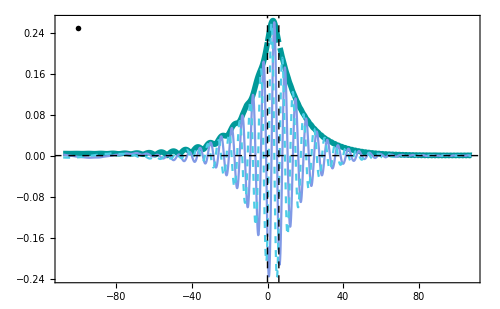

```mathematica
phi20dn001=Plot[{Abs[ψ[z]]n,Re[ψ[z]]n,Im[ψ[z]]n},{z,-18tc,18tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi_0(\\tau)|"},Magnification->1.8],PlotStyle->{{Thickness[0.008],color1},{{},color2},{Dashed,color3}},Evaluate@plotStyle,ImageSize->500,Epilog->{Inset[MaTeX["\\text{(a)}",Magnification->1.8],{-100,0.25}]}]
```

```mathematica
Export["phi_tc20_dn001.pdf",phi20dn001]
```

phi_tc20_dn001.pdf

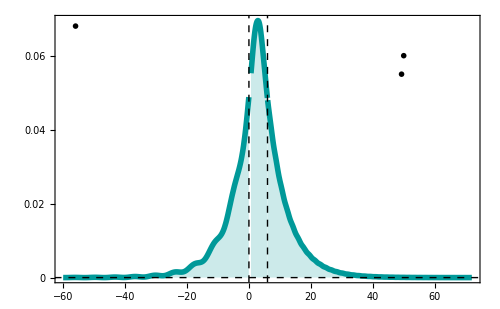

```mathematica
phi26adn001=Plot[{Abs[ψ2[z]]^2n^2},{z,-10tc,12tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi_0(\\tau)|^2"},Magnification->1.8],PlotStyle->{{Thickness[0.008],color1}},Filling->Axis,Evaluate@plotStyle,FrameTicks->{{{0,0.02,0.04,0.06},None},{Automatic,None}},ImageSize->500,Epilog->{Inset[MaTeX["\\text{(a)}",Magnification->1.8],{-56,0.068}],Inset[MaTeX["\\tau_\\text{c}=6",Magnification->1.6],{50,0.06}],Inset[MaTeX["\\delta \\text{n}_{\\text{max}}=0.01",Magnification->1.6],{49.3,0.055}]}]
```

Continuity of the absolute value of ψ (color1), ψ’(color1),ψ’’ (green), ψ’’’ (purple). As expected, only the first three are zero at the borders of the cavity

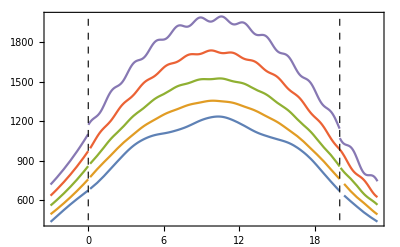

```mathematica
Plot[{Abs[ψ[z]],Abs[ψ'[z]],Abs[ψ''[z]],Abs[ψ'''[z]],Abs[ψ''''[z]]},{z,-3,tc+3},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau","Continuity"},Magnification->1.5],Evaluate@plotStyle]
```

Details of the continuity in the borders of the cavity

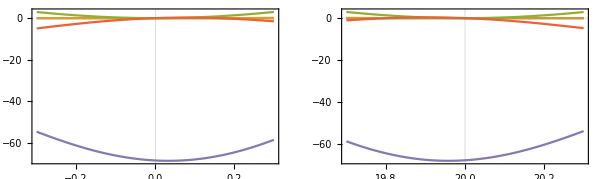

```mathematica
GraphicsRow[{
Plot[{Abs[ψ1t[z]]-Abs[ψ2t[z]],Abs[ψ1t'[z]]-Abs[ψ2t'[z]],Abs[ψ1t''[z]]-Abs[ψ2t''[z]],Abs[ψ1t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ1t''''[z]]-Abs[ψ2t''''[z]]},{z,-0.3,0.3},GridLines->{{0,tc},{}},Frame->True,Axes->False,PlotRange->All],
Plot[{Abs[ψ3t[z]]-Abs[ψ2t[z]],Abs[ψ3t'[z]]-Abs[ψ2t'[z]],Abs[ψ3t''[z]]-Abs[ψ2t''[z]],Abs[ψ3t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ3t''''[z]]-Abs[ψ2t''''[z]]},{z,tc-0.3,tc+.3},GridLines->{{0,tc},{0}},Frame->True,Axes->False,PlotRange->All]},ImageSize->600]
```

### Plot the solution ψ τ_c=6, δn=0.05,a (B)

```mathematica
wTest=0.3328972+0.0000615 ⅈ
tc
```

0.332897+0.0000615 ⅈ

6

Calculo de las amplitudes en la región I dadas c1=1 y c2=ρ.  (Recordar que a1=a2=0)

```mathematica
a1t=a1/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a2t=a2/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a3t=a3/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a4t=a4/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
```

0.000348-0.000232082 ⅈ

0.-5.55112×10^-17 ⅈ

-95.2804-47.4052 ⅈ

-13.4454+7.7418 ⅈ

```mathematica
c1t=1
c2t=rho4[Re[wTest],Im[wTest]]
c3t=0
c4t=0
```

1

-66.161-83.4298 ⅈ

0

0

```mathematica
Abs[c2t]^2+Abs[1]^2
```

11338.8

```mathematica
Abs[a1t]^2+Abs[a2t]^2+Abs[a3t]^2+Abs[a4t]^2
```

11566.3

w11 (ω_(1u))⟶ Im<0.  a1=Free. Decae en la región I. c1=0 
w12 (ω_(1ur))⟶ Im<0. a2=Free. Decae en la región I. c2=0
w13 (ω_(1ul))⟶ Im>0. a3=0. Decae en la regiónIII. c3=1
w14 (ω_(1v))⟶ Im>0. a4=0. Decae en la regiónIII. c3=ρ
w21 (ω_(2u))⟶  Estado confinado
w22 (ω_(2ur))⟶ Estado confinado 
w23 (ω_(2ul))⟶  Estado confinado 
w24 (ω_(2v))⟶  Estado confinado

```mathematica
{w11[Re[wTest],Im[wTest]],w12[Re[wTest],Im[wTest]],w13[Re[wTest],Im[wTest]],w14[Re[wTest],Im[wTest]]}
{w21[Re[wTest],Im[wTest]],w22[Re[wTest],Im[wTest]],w23[Re[wTest],Im[wTest]],w24[Re[wTest],Im[wTest]]}
```

{-2.28721-0.0000559958 ⅈ,1.07572-0.273969 ⅈ,1.07512+0.274 ⅈ,0.131012+0.0000241564 ⅈ}

{-2.39114-0.0000533584 ⅈ,1.39696-0.000290067 ⅈ,0.860545+0.000318788 ⅈ,0.133636+0.0000246374 ⅈ}

Calculo de las amplitudes en la región I. 
Forma1:ψ_I=ψ_I
Forma 2:  ψ_I=(Jump^-1.P_L.Jump)ψ_III

```mathematica
amp1t={0a1t , 0a2t,a3t,a4t};
ψ1t[τ_]=(amp1t.solsub/.wrule[Re[wTest],Im[wTest]])
amp1t2=ijump.propaL.jump.{c1t,c2t,c3t,c4t};
ψ1t2[τ_]=Chop[amp1t2.solsub/.wrule[Re[wTest],Im[wTest]]]
```

(0.+0. ⅈ)-(13.4454-7.7418 ⅈ) ⅇ^((0.0000241564-0.131012 ⅈ) τ)-(95.2804+47.4052 ⅈ) ⅇ^((0.274-1.07512 ⅈ) τ)

(0.000348-0.000232082 ⅈ) ⅇ^((-0.0000559958+2.28721 ⅈ) τ)-(13.4454-7.7418 ⅈ) ⅇ^((0.0000241564-0.131012 ⅈ) τ)-(95.2804+47.4052 ⅈ) ⅇ^((0.274-1.07512 ⅈ) τ)

Calculo de las amplitudes en la región II. 
Forma1: ψ_II=(P_L.Jump)ψ_III
Forma 2: ψ_II=(Jump)ψ_I

```mathematica
amp2t=jump.{0a1t ,0a2t,a3t,a4t}//Simplify;
amp2t2=propaL.jump.{c1t, c2t,c3t,c4t};
ψ2t[τ_]=amp2t.solsup/.wrule[Re[wTest],Im[wTest]]
ψ2t2[τ_]=amp2t2.solsup/.wrule[Re[wTest],Im[wTest]]
```

(7.81923-48.5105 ⅈ) ⅇ^((-0.000290067-1.39696 ⅈ) τ)-(0.290145+0.399282 ⅈ) ⅇ^((-0.0000533584+2.39114 ⅈ) τ)+(3.81722+23.6113 ⅈ) ⅇ^((0.0000246374-0.133636 ⅈ) τ)-(120.072+14.3649 ⅈ) ⅇ^((0.000318788-0.860545 ⅈ) τ)

(7.81933-48.5106 ⅈ) ⅇ^((-0.000290067-1.39696 ⅈ) τ)-(0.289831+0.399491 ⅈ) ⅇ^((-0.0000533584+2.39114 ⅈ) τ)+(3.8174+23.6112 ⅈ) ⅇ^((0.0000246374-0.133636 ⅈ) τ)-(120.072+14.3647 ⅈ) ⅇ^((0.000318788-0.860545 ⅈ) τ)

```mathematica
Abs[ψ1t[0]]
Abs[ψ2t[0]]
Abs[ψ1t2[0]]
Abs[ψ2t2[0]]
```

115.734

115.734

115.734

«1 more identical outputs»

La funciones en la región III, estaran desfasadas debido al salto entre la región II y III en una cantidad tc. Esto se corrige con el cambio ψ_III(τ)⟶ψ_III(τ-tc) o teniendo en cuenta dicha fase.  ψ_III=(Jump^-1.P_L1.P_R.Jump)ψ_I

```mathematica
propaR1=DiagonalMatrix[{Exp[-I w1sub tc],Exp[-I w2sub tc],Exp[-I w3sub tc],Exp[-I w4sub tc]}];
propaL1=DiagonalMatrix[{Exp[I w1sub tc],Exp[I w2sub tc],Exp[I w3sub tc],Exp[I w4sub tc]}];
```

```mathematica
amp3t=Simplify[propaL1.ijump.propaR.amp2t]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t[τ_]=amp3t.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
amp3t2=Simplify[propaL1.{c1t,c2t,c3t,c4t}]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t2[τ_]=amp3t2.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
```

(-263.846-483.739 ⅈ) ⅇ^((-0.273969-1.07572 ⅈ) τ)+(0.401915-0.915873 ⅈ) ⅇ^((-0.0000559958+2.28721 ⅈ) τ)-(0.000234443-0.000391936 ⅈ) ⅇ^((0.0000241564-0.131012 ⅈ) τ)+(0.0000651083-0.0000156426 ⅈ) ⅇ^((0.274-1.07512 ⅈ) τ)

(-263.846-483.74 ⅈ) ⅇ^((-0.273969-1.07572 ⅈ) τ)+(0.402335-0.91586 ⅈ) ⅇ^((-0.0000559958+2.28721 ⅈ) τ)

```mathematica
Abs[ψ2t[tc]]
Abs[ψ2t2[tc]]
Abs[ψ3t[tc]]
Abs[ψ3t2[tc]]
```

105.861

105.861

105.861

«1 more identical outputs»

```mathematica
ψ[τ_]:=Piecewise[{{ψ3t[τ],τ≥tc},{ψ2t[τ],0<τ<tc},{ψ1t[τ],τ≤0}}]
ψ2[τ_]:=Piecewise[{{ψ3t2[τ],τ≥tc},{ψ2t2[τ],0<τ<tc},{ψ1t2[τ],τ≤0}}]
```

Norma del estado ∫n^2|ψ|^2 ⅆx=1,  se integra entre -10tc y 10tc para realizar más rapido el calculo.
Por lo cual n=1/ √(∫| ψ |^2ⅆx)

```mathematica
Norma=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-100tc,100tc}]
Norma1=Integrate[ψ[x]*Conjugate[ψ[x]],{x,-20tc,20tc}]
```

342384.+0. ⅈ

2.96539×10^20+0. ⅈ

```mathematica
NormaI=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-100tc,0}]
```

160854.+0. ⅈ

```mathematica
NormaI=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-100tc,0}]/Norma (*Propabilidad de encontrar el campo en la zona I*)
NormaII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,0,tc}]/Norma(*Propabilidad de encontrar el campo en la zona II*)
NormaIII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,tc,100tc}]/Norma(*Propabilidad de encontrar el campo en la zona III*)
```

0.469806+0. ⅈ

0.468235+0. ⅈ

0.0619595+0. ⅈ

```mathematica
NormaI+NormaII+NormaIII(*Propabilidad de encontrar el campo en todo el espacio es aprox 1*)
```

1.+0. ⅈ

Para este estado existe una probabilidad del 47% de encontrar el campo dentro de la cavidad y 53% de encontrarlo fuera.

```mathematica
n=1/Sqrt[Norma]
```

0.001709+0. ⅈ

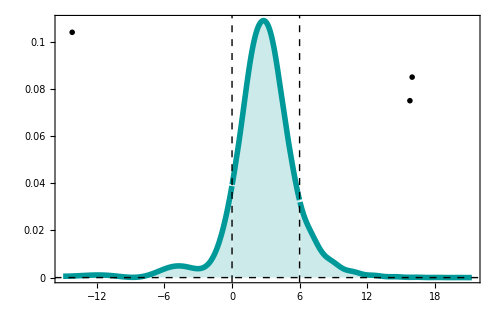

```mathematica
phi26adn001=Plot[{Abs[ψ2[z]]^2n^2},{z,-2.5tc,3.55tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi_0(\\tau)|^2"},Magnification->1.8],PlotStyle->{{Thickness[0.008],color1}},Filling->Axis,Evaluate@plotStyle,FrameTicks->{{{0,0.02,0.04,0.06,0.08,0.1,0.2},None},{Automatic,None}},ImageSize->500,Epilog->{Inset[MaTeX["\\text{(e)}",Magnification->1.8],{-14.2,0.104}],Inset[MaTeX["\\tau_\\text{c}=6",Magnification->1.6],{16,0.085}],Inset[MaTeX["\\delta \\text{n}_{\\text{max}}=0.05",Magnification->1.6],{15.8,0.075}]}]
```

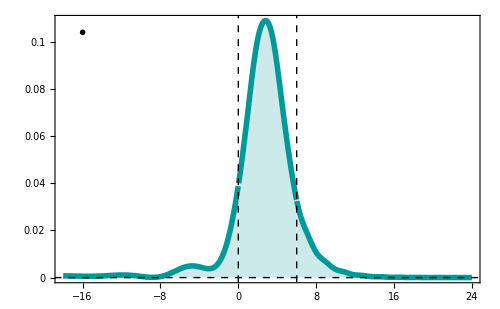

```mathematica
phi26adn005=Plot[{Abs[ψ2[z]]^2n^2},{z,-3tc,4tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi_0(\\tau)|^2"},Magnification->1.8],PlotStyle->{{Thickness[0.008],color1}},Filling->Axis,Evaluate@plotStyle,FrameTicks->{{{0,0.02,0.04,0.06,0.08,0.1,0.2},None},{Automatic,None}},ImageSize->500,Epilog->{Inset[MaTeX["\\text{(e)}",Magnification->1.8],{-16,0.104}],Inset[MaTeX["\\tau_\\text{c}=6",Magnification->1.6],{50,0.06}],Inset[MaTeX["\\delta \\text{n}_{\\text{max}}=0.01",Magnification->1.6],{49.3,0.055}]}]
```

```mathematica
Export["phi2_tc6a_dn005.pdf",phi26adn005]
```

phi2_tc20b_dn0.05.pdf

Continuity of real (color1) , imaginary (color1) and  absolute value (green) of ψ

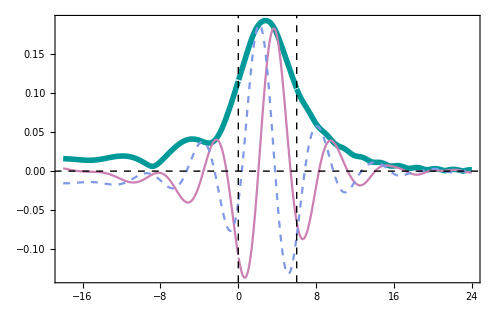

```mathematica
phi6adn005=Plot[{Abs[ψ2[z]]n,Re[ψ2[z]]n,Im[ψ2[z]]n},{z,-3tc,4tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi(\\tau)|"},Magnification->1.5],PlotStyle->{{Thickness[0.008],color1},{{},color5},{Dashed,color4}},Evaluate@plotStyle,ImageSize->500]
```

```mathematica
Export["phi_tc6a_dn005.pdf",phi6adn005]
```

phi_tc20b_dn005.pdf

Continuity of the absolute value of ψ (color1), ψ’(color1),ψ’’ (green), ψ’’’ (purple). As expected, only the first three are zero at the borders of the cavity

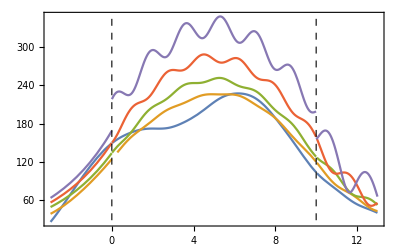

```mathematica
Plot[{Abs[ψ[z]],Abs[ψ'[z]],Abs[ψ''[z]],Abs[ψ'''[z]],Abs[ψ''''[z]]},{z,-3,tc+3},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau","Continuity"},Magnification->1.5],Evaluate@plotStyle]
```

Details of the continuity in the borders of the cavity

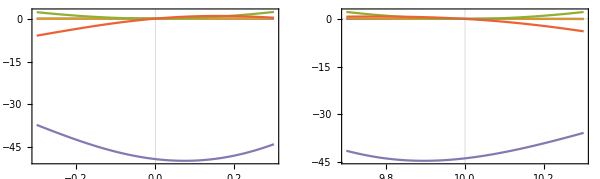

```mathematica
GraphicsRow[{
Plot[{Abs[ψ1t[z]]-Abs[ψ2t[z]],Abs[ψ1t'[z]]-Abs[ψ2t'[z]],Abs[ψ1t''[z]]-Abs[ψ2t''[z]],Abs[ψ1t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ1t''''[z]]-Abs[ψ2t''''[z]]},{z,-0.3,0.3},GridLines->{{0,tc},{}},Frame->True,Axes->False,PlotRange->All],
Plot[{Abs[ψ3t[z]]-Abs[ψ2t[z]],Abs[ψ3t'[z]]-Abs[ψ2t'[z]],Abs[ψ3t''[z]]-Abs[ψ2t''[z]],Abs[ψ3t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ3t''''[z]]-Abs[ψ2t''''[z]]},{z,tc-0.3,tc+.3},GridLines->{{0,tc},{0}},Frame->True,Axes->False,PlotRange->All]},ImageSize->600]
```

```mathematica
ContourPlot[Abs[1/a1/.wrule[wpRe,wpIm]/.ρ->rho4[wpRe,wpIm]]^(1/4),{wpRe,0.31,0.33},{wpIm,0,0.002},PlotLegends->Automatic,PlotPoints->10,FrameLabel->{"Re(W')","Im(W')"},ColorFunction->ColorData["color1GreenYellow"],Contours->{Automatic,10}]
```

### Plot the solution ψ τ_c=13, δn=0.01,a (B)

```mathematica
r13adn001=0.35454+I 9.6*^-7;
```

```mathematica
wTest=0.35454+I 9.6*^-7
tc
```

0.35454+9.6×10^-7 ⅈ

13

Calculo de las amplitudes en la región I dadas c1=1 y c2=ρ.  (Recordar que a1=a2=0)

```mathematica
a1t=a1/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a2t=a2/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a3t=a3/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a4t=a4/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
```

0.00461464-0.00644896 ⅈ

0.+0. ⅈ

493.981-364.465 ⅈ

2.31716+3.57749 ⅈ

```mathematica
c1t=1
c2t=rho4[Re[wTest],Im[wTest]]
c3t=0
c4t=0
```

1

-454.175-413.158 ⅈ

0

0

w11 (ω_(1u))⟶ Im<0.  a1=Free. Decae en la región I. c1=0 
w12 (ω_(1ur))⟶ Im<0. a2=Free. Decae en la región I. c2=0
w13 (ω_(1ul))⟶ Im>0. a3=0. Decae en la regiónIII. c3=1
w14 (ω_(1v))⟶ Im>0. a4=0. Decae en la regiónIII. c3=ρ
w21 (ω_(2u))⟶  Estado confinado
w22 (ω_(2ur))⟶ Estado confinado 
w23 (ω_(2ul))⟶  Estado confinado 
w24 (ω_(2v))⟶  Estado confinado

```mathematica
{w11[Re[wTest],Im[wTest]],w12[Re[wTest],Im[wTest]],w13[Re[wTest],Im[wTest]],w14[Re[wTest],Im[wTest]]}
{w21[Re[wTest],Im[wTest]],w22[Re[wTest],Im[wTest]],w23[Re[wTest],Im[wTest]],w24[Re[wTest],Im[wTest]]}
```

{-2.38918-8.27147×10^-7 ⅈ,1.12316-0.122133 ⅈ,1.12314+0.122134 ⅈ,0.141737+3.82902×10^-7 ⅈ}

{-2.40976-8.19558×10^-7 ⅈ,1.25523-0.0000101646 ⅈ,1.01222+0.0000105998 ⅈ,0.142305+3.84424×10^-7 ⅈ}

Calculo de las amplitudes en la región I. 
Forma1:ψ_I=ψ_I
Forma 2:  ψ_I=(Jump^-1.P_L.Jump)ψ_III

```mathematica
amp1t={0a1t , 0a2t,a3t,a4t};
ψ1t[τ_]=(amp1t.solsub/.wrule[Re[wTest],Im[wTest]])
amp1t2=ijump.propaL.jump.{c1t,c2t,c3t,c4t};
ψ1t2[τ_]=Chop[amp1t2.solsub/.wrule[Re[wTest],Im[wTest]]]
```

(0.+0. ⅈ)+(2.31716+3.57749 ⅈ) ⅇ^((3.82902×10^-7-0.141737 ⅈ) τ)+(493.981-364.465 ⅈ) ⅇ^((0.122134-1.12314 ⅈ) τ)

(0.00461464-0.00644896 ⅈ) ⅇ^((-8.27147×10^-7+2.38918 ⅈ) τ)+(2.31716+3.57749 ⅈ) ⅇ^((3.82902×10^-7-0.141737 ⅈ) τ)+(493.981-364.465 ⅈ) ⅇ^((0.122134-1.12314 ⅈ) τ)

Calculo de las amplitudes en la región II. 
Forma1: ψ_II=(P_L.Jump)ψ_III
Forma 2: ψ_II=(Jump)ψ_I

```mathematica
amp2t=jump.{0a1t ,0a2t,a3t,a4t}//Simplify;
amp2t2=propaL.jump.{c1t, c2t,c3t,c4t};
ψ2t[τ_]=amp2t.solsup/.wrule[Re[wTest],Im[wTest]]
ψ2t2[τ_]=amp2t2.solsup/.wrule[Re[wTest],Im[wTest]]
```

(334.581+124.537 ⅈ) ⅇ^((-0.0000101646-1.25523 ⅈ) τ)+(0.512737-0.231748 ⅈ) ⅇ^((-8.19558×10^-7+2.40976 ⅈ) τ)-(20.381-16.3966 ⅈ) ⅇ^((3.84424×10^-7-0.142305 ⅈ) τ)+(181.585-501.59 ⅈ) ⅇ^((0.0000105998-1.01222 ⅈ) τ)

(334.582+124.536 ⅈ) ⅇ^((-0.0000101646-1.25523 ⅈ) τ)+(0.517262-0.23807 ⅈ) ⅇ^((-8.19558×10^-7+2.40976 ⅈ) τ)-(20.3805-16.3959 ⅈ) ⅇ^((3.84424×10^-7-0.142305 ⅈ) τ)+(181.584-501.588 ⅈ) ⅇ^((0.0000105998-1.01222 ⅈ) τ)

```mathematica
Abs[ψ1t[0]]
Abs[ψ2t[0]]
Abs[ψ1t2[0]]
Abs[ψ2t2[0]]
```

613.638

613.638

613.646

613.646

La funciones en la región III, estaran desfasadas debido al salto entre la región II y III en una cantidad tc. Esto se corrige con el cambio ψ_III(τ)⟶ψ_III(τ-tc) o teniendo en cuenta dicha fase.  ψ_III=(Jump^-1.P_L1.P_R.Jump)ψ_I

```mathematica
propaR1=DiagonalMatrix[{Exp[-I w1sub tc],Exp[-I w2sub tc],Exp[-I w3sub tc],Exp[-I w4sub tc]}];
propaL1=DiagonalMatrix[{Exp[I w1sub tc],Exp[I w2sub tc],Exp[I w3sub tc],Exp[I w4sub tc]}];
```

```mathematica
amp3t=Simplify[propaL1.ijump.propaR.amp2t]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t[τ_]=amp3t.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
amp3t2=Simplify[propaL1.{c1t,c2t,c3t,c4t}]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t2[τ_]=amp3t2.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
```

(2802.13-1082.6 ⅈ) ⅇ^((-0.122133-1.12316 ⅈ) τ)+(0.930967+0.35403 ⅈ) ⅇ^((-8.27147×10^-7+2.38918 ⅈ) τ)+(0.000228589+0.00129216 ⅈ) ⅇ^((3.82902×10^-7-0.141737 ⅈ) τ)+(0.000584505-0.000147905 ⅈ) ⅇ^((0.122134-1.12314 ⅈ) τ)

(2802.13-1082.61 ⅈ) ⅇ^((-0.122133-1.12316 ⅈ) τ)+(0.937124+0.349027 ⅈ) ⅇ^((-8.27147×10^-7+2.38918 ⅈ) τ)

```mathematica
Abs[ψ2t[tc]]
Abs[ψ2t2[tc]]
Abs[ψ3t[tc]]
Abs[ψ3t2[tc]]
```

613.243

613.243

613.243

«1 more identical outputs»

```mathematica
ψ[τ_]:=Piecewise[{{ψ3t[τ],τ≥tc},{ψ2t[τ],0<τ<tc},{ψ1t[τ],τ≤0}}]
ψ2[τ_]:=Piecewise[{{ψ3t2[τ],τ≥tc},{ψ2t2[τ],0<τ<tc},{ψ1t2[τ],τ≤0}}]
```

Norma del estado ∫n^2|ψ|^2 ⅆx=1,  se integra entre -10tc y 10tc para realizar más rapido el calculo.
Por lo cual n=1/ √(∫| ψ |^2ⅆx)

```mathematica
Norma=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-10tc,10tc}]
```

1.16041×10^7+0. ⅈ

```mathematica
NormaI=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-10tc,0}]
```

1.55035×10^6+0. ⅈ

```mathematica
NormaI=Integrate[ψ1t[x]*Conjugate[ψ1t[x]],{x,-10tc,0}]/Norma (*Propabilidad de encontrar el campo en la zona I*)
NormaII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,0,tc}]/Norma(*Propabilidad de encontrar el campo en la zona II*)
NormaIII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,tc,10tc}]/Norma(*Propabilidad de encontrar el campo en la zona III*)
```

0.133603+0. ⅈ

0.733412+0. ⅈ

0.132984+0. ⅈ

```mathematica
NormaI+NormaII+NormaIII(*Propabilidad de encontrar el campo en todo el espacio es aprox 1*)
```

1.+0. ⅈ

Para este estado dn=0.01 tc=13a existe una probabilidad del 74% de encontrar el campo dentro de la cavidad y 16% de encontrarlo fuera.

```mathematica
n=1/Sqrt[Norma]
```

0.000293558+0. ⅈ

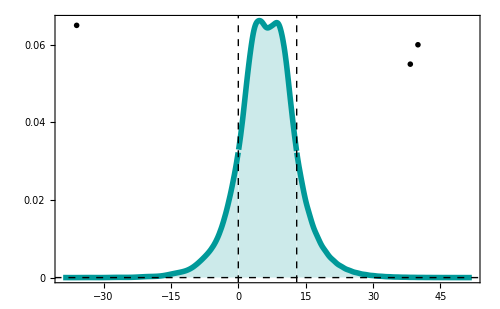

```mathematica
phi213adn001=Plot[{Abs[ψ2[z]]^2n^2},{z,-3tc,4tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi_0(\\tau)|^2"},Magnification->1.8],PlotStyle->{{Thickness[0.008],color1}},Evaluate@plotStyle,ImageSize->500,PlotStyle->{{Thickness[0.008],color1}},Filling->Axis,Evaluate@plotStyle,FrameTicks->{{{0,0.02,0.04,0.06},None},{Automatic,None}},ImageSize->500,Epilog->{Inset[MaTeX["\\text{(b)}",Magnification->1.8],{-36,0.065}],Inset[MaTeX["\\tau_\\text{c}=13",Magnification->1.6],{40,0.06}],Inset[MaTeX["\\delta \\text{n}_{\\text{max}}=0.01",Magnification->1.6],{38.3,0.055}]}]
```

```mathematica
Export["phi2_tc13a_dn001.pdf",phi213adn001]
```

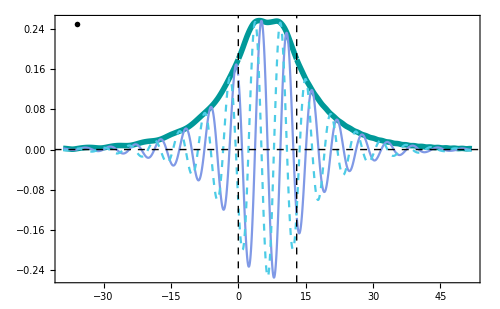

```mathematica
phi13adn001=Plot[{Abs[ψ2[z]]n,Re[ψ2[z]]n,Im[ψ2[z]]n},{z,-3tc,4tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi_0(\\tau)|"},Magnification->1.8],PlotStyle->{{Thickness[0.008],color1},{{},color2},{Dashed,color3}},Evaluate@plotStyle,ImageSize->500,Epilog->{Inset[MaTeX["\\text{(b)}",Magnification->1.8],{-36,0.25}]}]
```

```mathematica
Export["phi_tc13a_dn001.pdf",phi213adn001]
```

Continuity of the absolute value of ψ (color1), ψ’(color1),ψ’’ (green), ψ’’’ (purple). As expected, only the first three are zero at the borders of the cavity

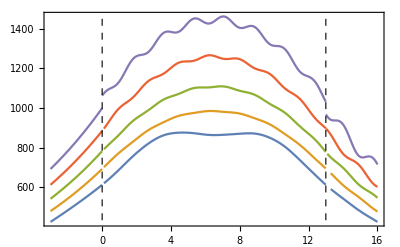

```mathematica
Plot[{Abs[ψ[z]],Abs[ψ'[z]],Abs[ψ''[z]],Abs[ψ'''[z]],Abs[ψ''''[z]]},{z,-3,tc+3},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau","Continuity"},Magnification->1.5],Evaluate@plotStyle]
```

Details of the continuity in the borders of the cavity

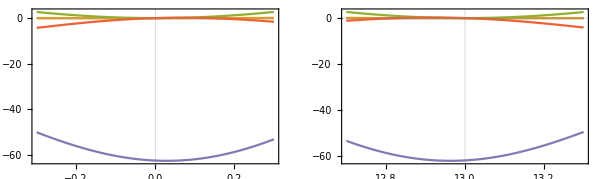

```mathematica
GraphicsRow[{
Plot[{Abs[ψ1t[z]]-Abs[ψ2t[z]],Abs[ψ1t'[z]]-Abs[ψ2t'[z]],Abs[ψ1t''[z]]-Abs[ψ2t''[z]],Abs[ψ1t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ1t''''[z]]-Abs[ψ2t''''[z]]},{z,-0.3,0.3},GridLines->{{0,tc},{}},Frame->True,Axes->False,PlotRange->All],
Plot[{Abs[ψ3t[z]]-Abs[ψ2t[z]],Abs[ψ3t'[z]]-Abs[ψ2t'[z]],Abs[ψ3t''[z]]-Abs[ψ2t''[z]],Abs[ψ3t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ3t''''[z]]-Abs[ψ2t''''[z]]},{z,tc-0.3,tc+.3},GridLines->{{0,tc},{0}},Frame->True,Axes->False,PlotRange->All]},ImageSize->600]
```

### Plot the solution ψ τ_c=13, δn=0.05,a (B)

```mathematica
wTest=0.3489765+I 0.0000145
tc
```

0.348977+0.0000145 ⅈ

13

Calculo de las amplitudes en la región I dadas c1=1 y c2=ρ.  (Recordar que a1=a2=0)

```mathematica
a1t=a1/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a2t=a2/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a3t=a3/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a4t=a4/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
```

-0.010735+0.00163515 ⅈ

8.32667×10^-17+2.22045×10^-16 ⅈ

61.8553-95.4627 ⅈ

-1.83896-1.98704 ⅈ

```mathematica
c1t=1
c2t=rho4[Re[wTest],Im[wTest]]
c3t=0
c4t=0
```

1

-47.7304-103.563 ⅈ

0

0

w11 (ω_(1u))⟶ Im<0.  a1=0. Decae en la región III. c1=1 
w12 (ω_(1ur))⟶ Im<0. a2=0. Decae en la región III. c2=ρ
w13 (ω_(1ul))⟶ Im>0. a3=Free. Decae en la regiónI. c3=0
w14 (ω_(1v))⟶ Im>0. a4=Free. Decae en la regiónI. c3=0
w21 (ω_(2u))⟶  Estado confinado

w22 (ω_(2ur))⟶ Estado confinado 
w23 (ω_(2ul))⟶  Estado confinado 
w24 (ω_(2v))⟶  Estado confinado

```mathematica
{w11[Re[wTest],Im[wTest]],w12[Re[wTest],Im[wTest]],w13[Re[wTest],Im[wTest]],w14[Re[wTest],Im[wTest]]}
{w21[Re[wTest],Im[wTest]],w22[Re[wTest],Im[wTest]],w23[Re[wTest],Im[wTest]],w24[Re[wTest],Im[wTest]]}
```

{-2.30175-0.0000130297 ⅈ,1.07946-0.343429 ⅈ,1.07935+0.343436 ⅈ,0.137327+5.69378×10^-6 ⅈ}

{-2.405-0.0000124297 ⅈ,1.30394-0.000108095 ⅈ,0.960988+0.000114717 ⅈ,0.140077+5.80704×10^-6 ⅈ}

Calculo de las amplitudes en la región I. 
Forma1:ψ_I=ψ_I
Forma 2:  ψ_I=(Jump^-1.P_L.Jump)ψ_III

```mathematica
amp1t={0a1t , 0a2t,a3t,a4t};
ψ1t[τ_]=(amp1t.solsub/.wrule[Re[wTest],Im[wTest]])
amp1t2=ijump.propaL.jump.{c1t,c2t,c3t,c4t};
ψ1t2[τ_]=Chop[amp1t2.solsub/.wrule[Re[wTest],Im[wTest]]]
```

(0.+0. ⅈ)-(1.83896+1.98704 ⅈ) ⅇ^((5.69378×10^-6-0.137327 ⅈ) τ)+(61.8553-95.4627 ⅈ) ⅇ^((0.343436-1.07935 ⅈ) τ)

(-0.010735+0.00163515 ⅈ) ⅇ^((-0.0000130297+2.30175 ⅈ) τ)-(1.83896+1.98704 ⅈ) ⅇ^((5.69378×10^-6-0.137327 ⅈ) τ)+(61.8553-95.4627 ⅈ) ⅇ^((0.343436-1.07935 ⅈ) τ)

Calculo de las amplitudes en la región II. 
Forma1: ψ_II=(P_L.Jump)ψ_III
Forma 2: ψ_II=(Jump)ψ_I

```mathematica
amp2t=jump.{0a1t ,0a2t,a3t,a4t}//Simplify;
amp2t2=propaL.jump.{c1t, c2t,c3t,c4t};
ψ2t[τ_]=amp2t.solsup/.wrule[Re[wTest],Im[wTest]]
ψ2t2[τ_]=amp2t2.solsup/.wrule[Re[wTest],Im[wTest]]
```

(75.1924+62.3734 ⅈ) ⅇ^((-0.000108095-1.30394 ⅈ) τ)+(0.491728-0.20717 ⅈ) ⅇ^((-0.0000124297+2.405 ⅈ) τ)-(21.2725-12.7906 ⅈ) ⅇ^((5.80704×10^-6-0.140077 ⅈ) τ)+(5.60467-172.407 ⅈ) ⅇ^((0.000114717-0.960988 ⅈ) τ)

(75.1864+62.3743 ⅈ) ⅇ^((-0.000108095-1.30394 ⅈ) τ)+(0.482022-0.205691 ⅈ) ⅇ^((-0.0000124297+2.405 ⅈ) τ)-(21.2778-12.7914 ⅈ) ⅇ^((5.80704×10^-6-0.140077 ⅈ) τ)+(5.61497-172.408 ⅈ) ⅇ^((0.000114717-0.960988 ⅈ) τ)

```mathematica
Abs[ψ1t[0]]
Abs[ψ2t[0]]
Abs[ψ1t2[0]]
Abs[ψ2t2[0]]
```

114.448

114.448

114.441

114.441

La funciones en la región III, estaran desfasadas debido al salto entre la región II y III en una cantidad tc. Esto se corrige con el cambio ψ_III(τ)⟶ψ_III(τ-tc) o teniendo en cuenta dicha fase.  ψ_III=(Jump^-1.P_L1.P_R.Jump)ψ_I

```mathematica
propaR1=DiagonalMatrix[{Exp[-I w1sub tc],Exp[-I w2sub tc],Exp[-I w3sub tc],Exp[-I w4sub tc]}];
propaL1=DiagonalMatrix[{Exp[I w1sub tc],Exp[I w2sub tc],Exp[I w3sub tc],Exp[I w4sub tc]}];
```

```mathematica
amp3t=Simplify[propaL1.ijump.propaR.amp2t]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t[τ_]=amp3t.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
amp3t2=Simplify[propaL1.{c1t,c2t,c3t,c4t}]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t2[τ_]=amp3t2.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
```

(8518.19-5060.68 ⅈ) ⅇ^((-0.343429-1.07946 ⅈ) τ)+(0.081655+1.00729 ⅈ) ⅇ^((-0.0000130297+2.30175 ⅈ) τ)+(0.0037374-0.00843408 ⅈ) ⅇ^((5.69378×10^-6-0.137327 ⅈ) τ)-(0.0000696369-0.0000303054 ⅈ) ⅇ^((0.343436-1.07935 ⅈ) τ)

(8518.06-5060.01 ⅈ) ⅇ^((-0.343429-1.07946 ⅈ) τ)+(0.077582+0.997156 ⅈ) ⅇ^((-0.0000130297+2.30175 ⅈ) τ)

```mathematica
Abs[ψ2t[tc]]
Abs[ψ2t2[tc]]
Abs[ψ3t[tc]]
Abs[ψ3t2[tc]]
```

113.62

113.617

113.62

113.617

```mathematica
ψ[τ_]:=Piecewise[{{ψ3t[τ],τ≥tc},{ψ2t[τ],0<τ<tc},{ψ1t[τ],τ≤0}}]
ψ2[τ_]:=Piecewise[{{ψ3t2[τ],τ≥tc},{ψ2t2[τ],0<τ<tc},{ψ1t2[τ],τ≤0}}]
```

Norma del estado ∫n^2|ψ|^2 ⅆx=1,  se integra entre -10tc y 10tc para realizar más rapido el calculo.
Por lo cual n=1/ √(∫| ψ |^2ⅆx)

```mathematica
Norma=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-10tc,10tc}]
Norma=Integrate[ψ[x]*Conjugate[ψ[x]],{x,-2tc,2tc}]
```

722023.+0. ⅈ

721142.+0. ⅈ

```mathematica
NormaI=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-10tc,0}]
```

19282.+0. ⅈ

```mathematica
NormaI=Integrate[ψ1t[x]*Conjugate[ψ1t[x]],{x,-10tc,0}]/Norma (*Propabilidad de encontrar el campo en la zona I*)
NormaII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,0,tc}]/Norma(*Propabilidad de encontrar el campo en la zona II*)
NormaIII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,tc,10tc}]/Norma(*Propabilidad de encontrar el campo en la zona III*)
```

0.0267391+0. ⅈ

0.948158+0. ⅈ

0.0263264+0. ⅈ

```mathematica
NormaI+NormaII+NormaIII(*Propabilidad de encontrar el campo en todo el espacio es aprox 1*)
```

1.00122+0. ⅈ

Para este estado existe una probabilidad del 95% de encontrar el campo dentro de la cavidad y 5% de encontrarlo fuera.

```mathematica
n=1/Sqrt[Norma]
```

0.00117758+0. ⅈ

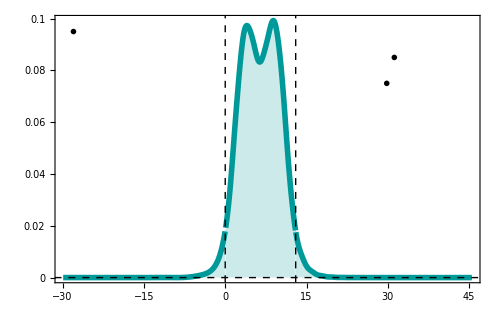

```mathematica
phi213bdn005=Plot[{Abs[ψ2[z]]^2n^2},{z,-2.3tc,3.5tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi_0(\\tau)|^2"},Magnification->1.8],PlotStyle->{{Thickness[0.008],color1}},Filling->Axis,Evaluate@plotStyle,FrameTicks->{{{0,0.02,0.04,0.06,0.08,0.1,0.2},None},{Automatic,None}},ImageSize->500,Epilog->{Inset[MaTeX["\\text{(f)}",Magnification->1.8],{-28,0.095}],Inset[MaTeX["\\tau_\\text{c}=13",Magnification->1.6],{31.2,0.085}],Inset[MaTeX["\\delta \\text{n}_{\\text{max}}=0.05",Magnification->1.6],{29.8,0.075}]}]
```

```mathematica
Export["phi2_tc13b_dn005.pdf",phi213bdn005]
```

phi2_tc13b_dn005.pdf

Continuity of real (color1) , imaginary (color1) and  absolute value (green) of ψ

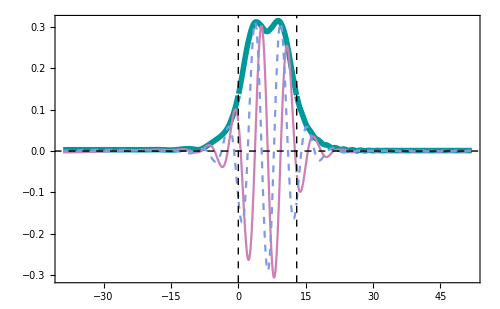

```mathematica
phi13bdn005=Plot[{Abs[ψ2[z]]n,Re[ψ2[z]]n,Im[ψ2[z]]n},{z,-3tc,4tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau","|\\phi(\\tau)|"},Magnification->1.5],PlotStyle->{{Thickness[0.008],color1},{{},color5},{Dashed,color4}},Evaluate@plotStyle,ImageSize->500]
```

```mathematica
Export["phi_tc13b_dn005.pdf",phi13bdn005]
```

phi_tc13b_dn005.pdf

Continuity of the absolute value of ψ (color1), ψ’(color1),ψ’’ (green), ψ’’’ (purple). As expected, only the first three are zero at the borders of the cavity

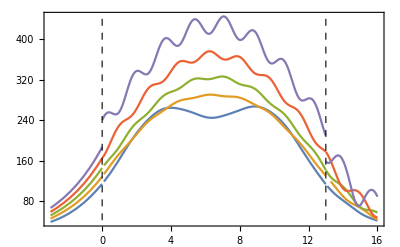

```mathematica
Plot[{Abs[ψ[z]],Abs[ψ'[z]],Abs[ψ''[z]],Abs[ψ'''[z]],Abs[ψ''''[z]]},{z,-3,tc+3},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau","Continuity"},Magnification->1.5],Evaluate@plotStyle]
```

Details of the continuity in the borders of the cavity

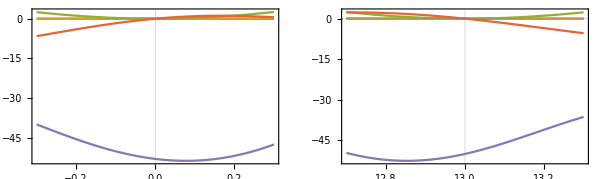

```mathematica
GraphicsRow[{
Plot[{Abs[ψ1t[z]]-Abs[ψ2t[z]],Abs[ψ1t'[z]]-Abs[ψ2t'[z]],Abs[ψ1t''[z]]-Abs[ψ2t''[z]],Abs[ψ1t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ1t''''[z]]-Abs[ψ2t''''[z]]},{z,-0.3,0.3},GridLines->{{0,tc},{}},Frame->True,Axes->False,PlotRange->All],
Plot[{Abs[ψ3t[z]]-Abs[ψ2t[z]],Abs[ψ3t'[z]]-Abs[ψ2t'[z]],Abs[ψ3t''[z]]-Abs[ψ2t''[z]],Abs[ψ3t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ3t''''[z]]-Abs[ψ2t''''[z]]},{z,tc-0.3,tc+.3},GridLines->{{0,tc},{0}},Frame->True,Axes->False,PlotRange->All]},ImageSize->600]
```

### Plot the solution ψ τ_c=13, δn=0.05,b

```mathematica
wTest=0.319695+I 0.0000487
tc
```

0.319695+0.0000487 ⅈ

13

Calculo de las amplitudes en la región I dadas c1=1 y c2=ρ.  (Recordar que a1=a2=0)

```mathematica
a1t=a1/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a2t=a2/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a3t=a3/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a4t=a4/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
```

-0.000719137-0.000302671 ⅈ

1.11022×10^-16+1.38778×10^-16 ⅈ

84.8036+113.872 ⅈ

30.4347+56.3375 ⅈ

```mathematica
c1t=1
c2t=rho4[Re[wTest],Im[wTest]]
c3t=0
c4t=0
```

1

-126.956+62.5226 ⅈ

0

0

```mathematica
Abs[c2t]^2+Abs[1]^2
```

20027.8

```mathematica
Abs[a1t]^2+Abs[a2t]^2+Abs[a3t]^2+Abs[a4t]^2
```

24258.7

w11 (ω_(1u))⟶ Im<0.  a1=Free. Decae en la región I. c1=0 
w12 (ω_(1ur))⟶ Im<0. a2=Free. Decae en la región I. c2=0
w13 (ω_(1ul))⟶ Im>0. a3=0. Decae en la regiónIII. c3=1
w14 (ω_(1v))⟶ Im>0. a4=0. Decae en la regiónIII. c3=ρ
w21 (ω_(2u))⟶  Estado confinado
w22 (ω_(2ur))⟶ Estado confinado 
w23 (ω_(2ul))⟶  Estado confinado 
w24 (ω_(2v))⟶  Estado confinado

```mathematica
{w11[Re[wTest],Im[wTest]],w12[Re[wTest],Im[wTest]],w13[Re[wTest],Im[wTest]],w14[Re[wTest],Im[wTest]]}
{w21[Re[wTest],Im[wTest]],w22[Re[wTest],Im[wTest]],w23[Re[wTest],Im[wTest]],w24[Re[wTest],Im[wTest]]}
```

{-2.27512-0.0000448341 ⅈ,1.07241-0.198961 ⅈ,1.07175+0.198986 ⅈ,0.125826+0.000019133 ⅈ}

{-2.37963-0.0000426822 ⅈ,1.4529-0.000187262 ⅈ,0.798373+0.00021043 ⅈ,0.128347+0.0000195142 ⅈ}

Calculo de las amplitudes en la región I. 
Forma1:ψ_I=ψ_I
Forma 2:  ψ_I=(Jump^-1.P_L.Jump)ψ_III

```mathematica
amp1t={0a1t , 0a2t,a3t,a4t};
ψ1t[τ_]=(amp1t.solsub/.wrule[Re[wTest],Im[wTest]])
amp1t2=ijump.propaL.jump.{c1t,c2t,c3t,c4t};
ψ1t2[τ_]=Chop[amp1t2.solsub/.wrule[Re[wTest],Im[wTest]]]
```

(0.+0. ⅈ)+(30.4347+56.3375 ⅈ) ⅇ^((0.000019133-0.125826 ⅈ) τ)+(84.8036+113.872 ⅈ) ⅇ^((0.198986-1.07175 ⅈ) τ)

(-0.000719137-0.000302671 ⅈ) ⅇ^((-0.0000448341+2.27512 ⅈ) τ)+(30.4347+56.3375 ⅈ) ⅇ^((0.000019133-0.125826 ⅈ) τ)+(84.8036+113.872 ⅈ) ⅇ^((0.198986-1.07175 ⅈ) τ)

Calculo de las amplitudes en la región II. 
Forma1: ψ_II=(P_L.Jump)ψ_III
Forma 2: ψ_II=(Jump)ψ_I

```mathematica
amp2t=jump.{0a1t ,0a2t,a3t,a4t}//Simplify;
amp2t2=propaL.jump.{c1t, c2t,c3t,c4t};
ψ2t[τ_]=amp2t.solsup/.wrule[Re[wTest],Im[wTest]]
ψ2t2[τ_]=amp2t2.solsup/.wrule[Re[wTest],Im[wTest]]
```

(-12.0972+46.6583 ⅈ) ⅇ^((-0.000187262-1.4529 ⅈ) τ)+(0.185484+0.629263 ⅈ) ⅇ^((-0.0000426822+2.37963 ⅈ) τ)+(17.0539+27.5366 ⅈ) ⅇ^((0.0000195142-0.128347 ⅈ) τ)+(110.096+95.3853 ⅈ) ⅇ^((0.00021043-0.798373 ⅈ) τ)

(-12.0974+46.6583 ⅈ) ⅇ^((-0.000187262-1.4529 ⅈ) τ)+(0.184836+0.62899 ⅈ) ⅇ^((-0.0000426822+2.37963 ⅈ) τ)+(17.0535+27.5364 ⅈ) ⅇ^((0.0000195142-0.128347 ⅈ) τ)+(110.097+95.3855 ⅈ) ⅇ^((0.00021043-0.798373 ⅈ) τ)

```mathematica
Abs[ψ1t[0]]
Abs[ψ2t[0]]
Abs[ψ1t2[0]]
Abs[ψ2t2[0]]
```

205.551

205.551

205.55

205.55

La funciones en la región III, estaran desfasadas debido al salto entre la región II y III en una cantidad tc. Esto se corrige con el cambio ψ_III(τ)⟶ψ_III(τ-tc) o teniendo en cuenta dicha fase.  ψ_III=(Jump^-1.P_L1.P_R.Jump)ψ_I

```mathematica
propaR1=DiagonalMatrix[{Exp[-I w1sub tc],Exp[-I w2sub tc],Exp[-I w3sub tc],Exp[-I w4sub tc]}];
propaL1=DiagonalMatrix[{Exp[I w1sub tc],Exp[I w2sub tc],Exp[I w3sub tc],Exp[I w4sub tc]}];
```

```mathematica
amp3t=Simplify[propaL1.ijump.propaR.amp2t]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t[τ_]=amp3t.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
amp3t2=Simplify[propaL1.{c1t,c2t,c3t,c4t}]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t2[τ_]=amp3t2.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
```

(-1142.85-1492.45 ⅈ) ⅇ^((-0.198961-1.07241 ⅈ) τ)-(0.265638-0.965481 ⅈ) ⅇ^((-0.0000448341+2.27512 ⅈ) τ)+(0.000399459-0.000118505 ⅈ) ⅇ^((0.000019133-0.125826 ⅈ) τ)-(7.59121×10^-6-0.0000509894 ⅈ) ⅇ^((0.198986-1.07175 ⅈ) τ)

(-1142.85-1492.45 ⅈ) ⅇ^((-0.198961-1.07241 ⅈ) τ)-(0.265494-0.964717 ⅈ) ⅇ^((-0.0000448341+2.27512 ⅈ) τ)

```mathematica
Abs[ψ2t[tc]]
Abs[ψ2t2[tc]]
Abs[ψ3t[tc]]
Abs[ψ3t2[tc]]
```

140.618

140.62

140.618

140.62

```mathematica
ψ[τ_]:=Piecewise[{{ψ3t[τ],τ≥tc},{ψ2t[τ],0<τ<tc},{ψ1t[τ],τ≤0}}]
ψ2[τ_]:=Piecewise[{{ψ3t2[τ],τ≥tc},{ψ2t2[τ],0<τ<tc},{ψ1t2[τ],τ≤0}}]
```

Norma del estado ∫n^2|ψ|^2 ⅆx=1,  se integra entre -10tc y 10tc para realizar más rapido el calculo.
Por lo cual n=1/ √(∫| ψ |^2ⅆx)

```mathematica
Norma=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-10tc,10tc}]
```

999763.+0. ⅈ

```mathematica
NormaI=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-10tc,0}]
```

588841.+0. ⅈ

```mathematica
NormaI=Integrate[ψ1t[x]*Conjugate[ψ1t[x]],{x,-10tc,0}]/Norma (*Propabilidad de encontrar el campo en la zona I*)
NormaII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,0,tc}]/Norma(*Propabilidad de encontrar el campo en la zona II*)
NormaIII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,tc,10tc}]/Norma(*Propabilidad de encontrar el campo en la zona III*)
```

0.588981+0. ⅈ

0.360529+0. ⅈ

0.0504897+0. ⅈ

```mathematica
NormaI+NormaII+NormaIII(*Propabilidad de encontrar el campo en todo el espacio es aprox 1*)
```

1.+0. ⅈ

Para este estado existe una probabilidad del 36% de encontrar el campo dentro de la cavidad y 64% de encontrarlo fuera.

```mathematica
n=1/Sqrt[Norma]
```

0.00100012+0. ⅈ

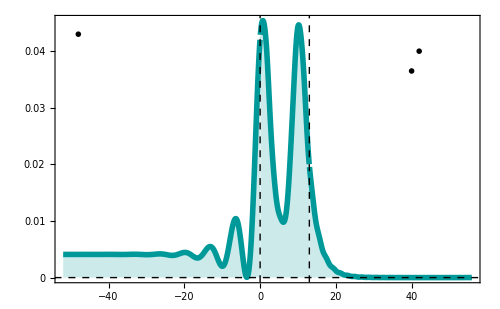

```mathematica
phi213dn005=Plot[{Abs[ψ[z]]^2n^2},{z,-4tc,4.3tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi_1(\\tau)|^2"},Magnification->1.8],PlotStyle->{{Thickness[0.008],color1}},Filling->Axis,Evaluate@plotStyle,FrameTicks->{{{0,0.010,0.020,0.030,0.040,0.050,0.2},None},{Automatic,None}},ImageSize->500,Epilog->{Inset[MaTeX["\\text{(g)}",Magnification->1.8],{-48,0.043}],Inset[MaTeX["\\tau_\\text{c}=13",Magnification->1.6],{42,0.040}],Inset[MaTeX["\\delta \\text{n}_{\\text{max}}=0.05",Magnification->1.6],{40,0.0365}]}]
```

```mathematica
Export["phi^2_tc13a_dn0.05.pdf",phi213dn005]
```

phi^2_tc13a_dn0.05.pdf

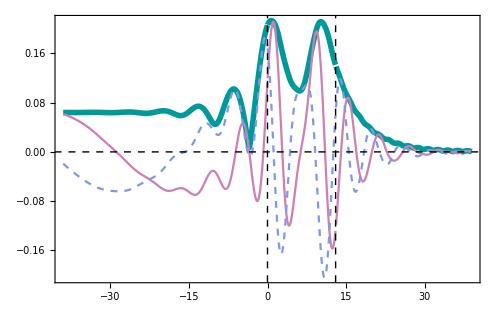

```mathematica
phi13dn005=Plot[{Abs[ψ[z]]n,Re[ψ[z]]n,Im[ψ[z]]n},{z,-3tc,3tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau(\\text{fs})","|\\phi(\\tau)|"},Magnification->1.5],PlotStyle->{{Thickness[0.008],color1},{{},color5},{Dashed,color4}},Evaluate@plotStyle,ImageSize->500]
```

```mathematica
Export["phi_tc13a_dn0.05.pdf",phi13dn005]
```

phi_tc13a_dn0.05.pdf

Continuity of the absolute value of ψ (color1), ψ’(color1),ψ’’ (green), ψ’’’ (purple). As expected, only the first three are zero at the borders of the cavity

```mathematica
Plot[{Abs[ψ[z]],Abs[ψ'[z]],Abs[ψ''[z]],Abs[ψ'''[z]],Abs[ψ''''[z]]},{z,-3,tc+3},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau","Continuity"},Magnification->1.5],Evaluate@plotStyle]
```

-Graphics-

Details of the continuity in the borders of the cavity

```mathematica
GraphicsRow[{
Plot[{Abs[ψ1t[z]]-Abs[ψ2t[z]],Abs[ψ1t'[z]]-Abs[ψ2t'[z]],Abs[ψ1t''[z]]-Abs[ψ2t''[z]],Abs[ψ1t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ1t''''[z]]-Abs[ψ2t''''[z]]},{z,-0.3,0.3},GridLines->{{0,tc},{}},Frame->True,Axes->False,PlotRange->All],
Plot[{Abs[ψ3t[z]]-Abs[ψ2t[z]],Abs[ψ3t'[z]]-Abs[ψ2t'[z]],Abs[ψ3t''[z]]-Abs[ψ2t''[z]],Abs[ψ3t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ3t''''[z]]-Abs[ψ2t''''[z]]},{z,tc-0.3,tc+.3},GridLines->{{0,tc},{0}},Frame->True,Axes->False,PlotRange->All]},ImageSize->600]
```

-Graphics-

### Plot the solution ψ τ_c=20, δn=0.01,a (B)

```mathematica
wTest=0.35655868+I 239/500000000
tc
```

0.356559+4.78×10^-7 ⅈ

20

Calculo de las amplitudes en la región I dadas c1=1 y c2=ρ.  (Recordar que a1=a2=0)

```mathematica
a1t=a1/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a2t=a2/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a3t=a3/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a4t=a4/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
```

-0.00287355+0.00799259 ⅈ

5.55112×10^-17-2.77556×10^-17 ⅈ

286.255+606.615 ⅈ

-16.8119+13.8635 ⅈ

```mathematica
c1t=1
c2t=rho4[Re[wTest],Im[wTest]]
c3t=0
c4t=0
```

1

-413.178-528.64 ⅈ

0

0

w11 (ω_(1u))⟶ Im<0.  a1=0. Decae en la región III. c1=1
w12 (ω_(1ur))⟶ Im<0. a2=0. Decae en la región III. c2=ρ
w13 (ω_(1ul))⟶ Im>0. a3=Free. Decae en la regiónIII. c3=0
w14 (ω_(1v))⟶ Im>0. a4=Free. Decae en la regiónIII. c3=0
w21 (ω_(2u))⟶  Estado confinado
w22 (ω_(2ur))⟶ Estado confinado 
w23 (ω_(2ul))⟶  Estado confinado 
w24 (ω_(2v))⟶  Estado confinado

```mathematica
{w11[Re[wTest],Im[wTest]],w12[Re[wTest],Im[wTest]],w13[Re[wTest],Im[wTest]],w14[Re[wTest],Im[wTest]]}
{w21[Re[wTest],Im[wTest]],w22[Re[wTest],Im[wTest]],w23[Re[wTest],Im[wTest]],w24[Re[wTest],Im[wTest]]}
```

{-2.39092-4.1123×10^-7 ⅈ,1.12362-0.142223 ⅈ,1.12361+0.142224 ⅈ,0.142542+1.90646×10^-7 ⅈ}

{-2.41149-4.07467×10^-7 ⅈ,1.23145-6.34363×10^-6 ⅈ,1.03692+6.55969×10^-6 ⅈ,0.143113+1.91404×10^-7 ⅈ}

Calculo de las amplitudes en la región I. 
Forma1:ψ_I=ψ_I
Forma 2:  ψ_I=(Jump^-1.P_L.Jump)ψ_III

```mathematica
amp1t={0a1t , 0a2t,a3t,a4t};
ψ1t[τ_]=(amp1t.solsub/.wrule[Re[wTest],Im[wTest]])
amp1t2=ijump.propaL.jump.{c1t,c2t,c3t,c4t};
ψ1t2[τ_]=Chop[amp1t2.solsub/.wrule[Re[wTest],Im[wTest]]]
```

(0.+0. ⅈ)-(16.8119-13.8635 ⅈ) ⅇ^((1.90646×10^-7-0.142542 ⅈ) τ)+(286.255+606.615 ⅈ) ⅇ^((0.142224-1.12361 ⅈ) τ)

(-0.00287355+0.00799259 ⅈ) ⅇ^((-4.1123×10^-7+2.39092 ⅈ) τ)-(16.8119-13.8635 ⅈ) ⅇ^((1.90646×10^-7-0.142542 ⅈ) τ)+(286.255+606.615 ⅈ) ⅇ^((0.142224-1.12361 ⅈ) τ)

Calculo de las amplitudes en la región II. 
Forma1: ψ_II=(P_L.Jump)ψ_III
Forma 2: ψ_II=(Jump)ψ_I

```mathematica
amp2t=jump.{0a1t ,0a2t,a3t,a4t}//Simplify;
amp2t2=propaL.jump.{c1t, c2t,c3t,c4t};
ψ2t[τ_]=amp2t.solsup/.wrule[Re[wTest],Im[wTest]]
ψ2t2[τ_]=amp2t2.solsup/.wrule[Re[wTest],Im[wTest]]
```

(-352.318+365.674 ⅈ) ⅇ^((-6.34363×10^-6-1.23145 ⅈ) τ)+(0.119337+0.604139 ⅈ) ⅇ^((-4.07467×10^-7+2.41149 ⅈ) τ)-(25.2012+13.2507 ⅈ) ⅇ^((1.91404×10^-7-0.143113 ⅈ) τ)+(646.844+267.451 ⅈ) ⅇ^((6.55969×10^-6-1.03692 ⅈ) τ)

(-352.319+365.676 ⅈ) ⅇ^((-6.34363×10^-6-1.23145 ⅈ) τ)+(0.116519+0.611976 ⅈ) ⅇ^((-4.07467×10^-7+2.41149 ⅈ) τ)-(25.2015+13.2499 ⅈ) ⅇ^((1.91404×10^-7-0.143113 ⅈ) τ)+(646.845+267.449 ⅈ) ⅇ^((6.55969×10^-6-1.03692 ⅈ) τ)

```mathematica
Abs[ψ1t[0]]
Abs[ψ2t[0]]
Abs[ψ1t2[0]]
Abs[ψ2t2[0]]
```

676.457

676.457

676.463

676.463

La funciones en la región III, estaran desfasadas debido al salto entre la región II y III en una cantidad tc. Esto se corrige con el cambio ψ_III(τ)⟶ψ_III(τ-tc) o teniendo en cuenta dicha fase.  ψ_III=(Jump^-1.P_L1.P_R.Jump)ψ_I

```mathematica
propaR1=DiagonalMatrix[{Exp[-I w1sub tc],Exp[-I w2sub tc],Exp[-I w3sub tc],Exp[-I w4sub tc]}];
propaL1=DiagonalMatrix[{Exp[I w1sub tc],Exp[I w2sub tc],Exp[I w3sub tc],Exp[I w4sub tc]}];
```

```mathematica
amp3t=Simplify[propaL1.ijump.propaR.amp2t]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t[τ_]=amp3t.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
amp3t2=Simplify[propaL1.{c1t,c2t,c3t,c4t}]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t2[τ_]=amp3t2.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
```

(2089.32+11344.4 ⅈ) ⅇ^((-0.142223-1.12362 ⅈ) τ)-(0.762511-0.633871 ⅈ) ⅇ^((-4.1123×10^-7+2.39092 ⅈ) τ)-(0.000650651+0.000376214 ⅈ) ⅇ^((1.90646×10^-7-0.142542 ⅈ) τ)-(0.000102571-0.000100049 ⅈ) ⅇ^((0.142224-1.12361 ⅈ) τ)

(2089.35+11344.5 ⅈ) ⅇ^((-0.142223-1.12362 ⅈ) τ)-(0.768343-0.640052 ⅈ) ⅇ^((-4.1123×10^-7+2.39092 ⅈ) τ)

```mathematica
Abs[ψ2t[tc]]
Abs[ψ2t2[tc]]
Abs[ψ3t[tc]]
Abs[ψ3t2[tc]]
```

670.338

670.336

670.338

670.336

```mathematica
ψ[τ_]:=Piecewise[{{ψ3t[τ],τ≥tc},{ψ2t[τ],0<τ<tc},{ψ1t[τ],τ≤0}}]
ψ2[τ_]:=Piecewise[{{ψ3t2[τ],τ≥tc},{ψ2t2[τ],0<τ<tc},{ψ1t2[τ],τ≤0}}]
```

Norma del estado ∫n^2|ψ|^2 ⅆx=1,  se integra entre -10tc y 10tc para realizar más rapido el calculo.
Por lo cual n=1/ √(∫| ψ |^2ⅆx)

```mathematica
Norma=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-10tc,10tc}]
Norma=Integrate[ψ[x]*Conjugate[ψ[x]],{x,-2tc,2tc}]
```

2.50529×10^7+0. ⅈ

2.49713×10^7+0. ⅈ

```mathematica
NormaI=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-10tc,0}]
```

1.70604×10^6+0. ⅈ

```mathematica
NormaI=Integrate[ψ1t[x]*Conjugate[ψ1t[x]],{x,-10tc,0}]/Norma (*Propabilidad de encontrar el campo en la zona I*)
NormaII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,0,tc}]/Norma(*Propabilidad de encontrar el campo en la zona II*)
NormaIII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,tc,10tc}]/Norma(*Propabilidad de encontrar el campo en la zona III*)
```

0.0683199+0. ⅈ

0.871572+0. ⅈ

0.0633729+0. ⅈ

```mathematica
NormaI+NormaII+NormaIII(*Propabilidad de encontrar el campo en todo el espacio es aprox 1*)
```

1.00326+0. ⅈ

Para este estado existe una probabilidad del 87% de encontrar el campo dentro de la cavidad y 13% de encontrarlo fuera.

```mathematica
n=1/Sqrt[Norma]
```

0.000200115+0. ⅈ

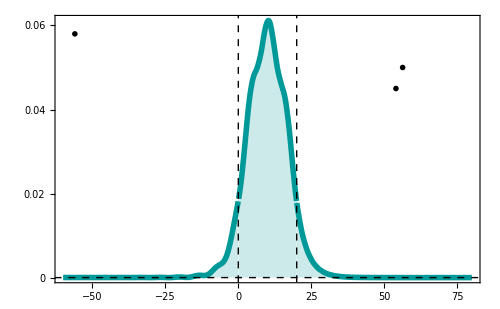

```mathematica
phi220adn001=Plot[{Abs[ψ2[z]]^2n^2},{z,-3tc,4tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi_0(\\tau)|^2"},Magnification->1.8],PlotStyle->{{Thickness[0.008],color1}},Evaluate@plotStyle,FrameTicks->{{{0,0.02,0.04,0.06},None},{Automatic,None}},ImageSize->500,PlotStyle->{{Thickness[0.008],color1}},Filling->Axis,Evaluate@plotStyle,Epilog->{Inset[MaTeX["\\text{(c)}",Magnification->1.8],{-56,0.058}],Inset[MaTeX["\\tau_\\text{c}=20",Magnification->1.6],{56.3,0.05}],Inset[MaTeX["\\delta \\text{n}_{\\text{max}}=0.01",Magnification->1.6],{54,0.045}]}]
```

```mathematica
Export["phi2_tc20a_dn001.pdf",phi220adn001]
```

phi2_tc20a_dn001.pdf

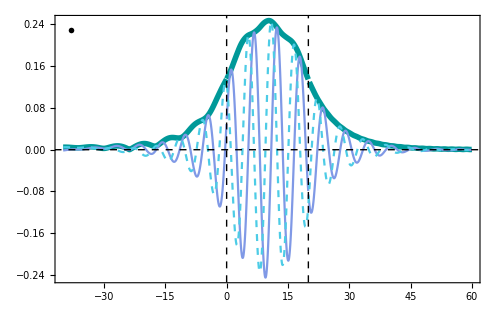

```mathematica
phi20dn001=Plot[{Abs[ψ[z]]n,Re[ψ[z]]n,Im[ψ[z]]n},{z,-2tc,3tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau","|\\phi_0(\\tau)|"},Magnification->1.8],PlotStyle->{{Thickness[0.008],color1},{{},color2},{Dashed,color3}},Evaluate@plotStyle,ImageSize->500,Epilog->{Inset[MaTeX["\\text{(c)}",Magnification->1.8],{-38,0.23}]}]
```

```mathematica
Export["phi_tc20adn001.pdf",phi20dn001]
```

phi_tc20_dn001.pdf

Continuity of the absolute value of ψ (color1), ψ’(color1),ψ’’ (green), ψ’’’ (purple). As expected, only the first three are zero at the borders of the cavity

```mathematica
Plot[{Abs[ψ[z]],Abs[ψ'[z]],Abs[ψ''[z]],Abs[ψ'''[z]],Abs[ψ''''[z]]},{z,-3,tc+3},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau","Continuity"},Magnification->1.5],Evaluate@plotStyle]
```

-Graphics-

Details of the continuity in the borders of the cavity

```mathematica
GraphicsRow[{
Plot[{Abs[ψ1t[z]]-Abs[ψ2t[z]],Abs[ψ1t'[z]]-Abs[ψ2t'[z]],Abs[ψ1t''[z]]-Abs[ψ2t''[z]],Abs[ψ1t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ1t''''[z]]-Abs[ψ2t''''[z]]},{z,-0.3,0.3},GridLines->{{0,tc},{}},Frame->True,Axes->False,PlotRange->All],
Plot[{Abs[ψ3t[z]]-Abs[ψ2t[z]],Abs[ψ3t'[z]]-Abs[ψ2t'[z]],Abs[ψ3t''[z]]-Abs[ψ2t''[z]],Abs[ψ3t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ3t''''[z]]-Abs[ψ2t''''[z]]},{z,tc-0.3,tc+.3},GridLines->{{0,tc},{0}},Frame->True,Axes->False,PlotRange->All]},ImageSize->600]
```

-Graphics-

### Plot the solution ψ τ_c=20, δn=0.01,b (B)

```mathematica
wTest=0.34908428+I 124/250000000
tc
```

0.349084+4.96×10^-7 ⅈ

20

Calculo de las amplitudes en la región I dadas c1=1 y c2=ρ.  (Recordar que a1=a2=0)

```mathematica
a1t=a1/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a2t=a2/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a3t=a3/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a4t=a4/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
```

0.0229329-0.012678 ⅈ

1.11022×10^-16-4.44089×10^-16 ⅈ

-790.527+149.501 ⅈ

-48.7443+36.8061 ⅈ

```mathematica
c1t=1
c2t=rho4[Re[wTest],Im[wTest]]
c3t=0
c4t=0
```

1

-578.34+559.112 ⅈ

0

0

```mathematica
Abs[c2t]^2+Abs[1]^2
```

647085.

```mathematica
Abs[a1t]^2+Abs[a2t]^2+Abs[a3t]^2+Abs[a4t]^2
```

651014.

w11 (ω_(1u))⟶ Im<0.  a1=Free. Decae en la región I. c1=0 
w12 (ω_(1ur))⟶ Im<0. a2=Free. Decae en la región I. c2=0
w13 (ω_(1ul))⟶ Im>0. a3=0. Decae en la regiónIII. c3=1
w14 (ω_(1v))⟶ Im>0. a4=0. Decae en la regiónIII. c3=ρ
w21 (ω_(2u))⟶  Estado confinado
w22 (ω_(2ur))⟶ Estado confinado 
w23 (ω_(2ul))⟶  Estado confinado 
w24 (ω_(2v))⟶  Estado confinado

```mathematica
{w11[Re[wTest],Im[wTest]],w12[Re[wTest],Im[wTest]],w13[Re[wTest],Im[wTest]],w14[Re[wTest],Im[wTest]]}
{w21[Re[wTest],Im[wTest]],w22[Re[wTest],Im[wTest]],w23[Re[wTest],Im[wTest]],w24[Re[wTest],Im[wTest]]}
```

{-2.38447-4.29113×10^-7 ⅈ,1.12192-0.0231871 ⅈ,1.12187+0.0231874 ⅈ,0.139561+1.97853×10^-7 ⅈ}

{-2.4051-4.25147×10^-7 ⅈ,1.30313-3.71594×10^-6 ⅈ,0.961843+3.94245×10^-6 ⅈ,0.14012+1.9864×10^-7 ⅈ}

Calculo de las amplitudes en la región I. 
Forma1:ψ_I=ψ_I
Forma 2:  ψ_I=(Jump^-1.P_L.Jump)ψ_III

```mathematica
amp1t={0a1t , 0a2t,a3t,a4t};
ψ1t[τ_]=(amp1t.solsub/.wrule[Re[wTest],Im[wTest]])
amp1t2=ijump.propaL.jump.{c1t,c2t,c3t,c4t};
ψ1t2[τ_]=Chop[amp1t2.solsub/.wrule[Re[wTest],Im[wTest]]]
```

(0.+0. ⅈ)-(48.7443-36.8061 ⅈ) ⅇ^((1.97853×10^-7-0.139561 ⅈ) τ)-(790.527-149.501 ⅈ) ⅇ^((0.0231874-1.12187 ⅈ) τ)

(0.0229329-0.012678 ⅈ) ⅇ^((-4.29113×10^-7+2.38447 ⅈ) τ)-(48.7443-36.8061 ⅈ) ⅇ^((1.97853×10^-7-0.139561 ⅈ) τ)-(790.527-149.501 ⅈ) ⅇ^((0.0231874-1.12187 ⅈ) τ)

Calculo de las amplitudes en la región II. 
Forma1: ψ_II=(P_L.Jump)ψ_III
Forma 2: ψ_II=(Jump)ψ_I

```mathematica
amp2t=jump.{0a1t ,0a2t,a3t,a4t}//Simplify;
amp2t2=propaL.jump.{c1t, c2t,c3t,c4t};
ψ2t[τ_]=amp2t.solsup/.wrule[Re[wTest],Im[wTest]]
ψ2t2[τ_]=amp2t2.solsup/.wrule[Re[wTest],Im[wTest]]
```

(-306.138+3.95344 ⅈ) ⅇ^((-3.71594×10^-6-1.30313 ⅈ) τ)-(0.727582-0.107984 ⅈ) ⅇ^((-4.25147×10^-7+2.4051 ⅈ) τ)-(14.7794-31.2226 ⅈ) ⅇ^((1.9864×10^-7-0.14012 ⅈ) τ)-(517.626-151.023 ⅈ) ⅇ^((3.94245×10^-6-0.961843 ⅈ) τ)

(-306.136+3.95194 ⅈ) ⅇ^((-3.71594×10^-6-1.30313 ⅈ) τ)-(0.7051-0.0955551 ⅈ) ⅇ^((-4.25147×10^-7+2.4051 ⅈ) τ)-(14.777-31.2213 ⅈ) ⅇ^((1.9864×10^-7-0.14012 ⅈ) τ)-(517.63-151.025 ⅈ) ⅇ^((3.94245×10^-6-0.961843 ⅈ) τ)

```mathematica
Abs[ψ1t[0]]
Abs[ψ2t[0]]
Abs[ψ1t2[0]]
Abs[ψ2t2[0]]
```

859.701

859.701

859.676

859.676

La funciones en la región III, estaran desfasadas debido al salto entre la región II y III en una cantidad tc. Esto se corrige con el cambio ψ_III(τ)⟶ψ_III(τ-tc) o teniendo en cuenta dicha fase.  ψ_III=(Jump^-1.P_L1.P_R.Jump)ψ_I

```mathematica
propaR1=DiagonalMatrix[{Exp[-I w1sub tc],Exp[-I w2sub tc],Exp[-I w3sub tc],Exp[-I w4sub tc]}];
propaL1=DiagonalMatrix[{Exp[I w1sub tc],Exp[I w2sub tc],Exp[I w3sub tc],Exp[I w4sub tc]}];
```

```mathematica
amp3t=Simplify[propaL1.ijump.propaR.amp2t]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t[τ_]=amp3t.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
amp3t2=Simplify[propaL1.{c1t,c2t,c3t,c4t}]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t2[τ_]=amp3t2.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
```

(1213.62-403.701 ⅈ) ⅇ^((-0.0231871-1.12192 ⅈ) τ)-(0.870369-0.538342 ⅈ) ⅇ^((-4.29113×10^-7+2.38447 ⅈ) τ)+(0.000206848+0.00171078 ⅈ) ⅇ^((1.97853×10^-7-0.139561 ⅈ) τ)+(0.00155465-0.0255133 ⅈ) ⅇ^((0.0231874-1.12187 ⅈ) τ)

(1213.63-403.762 ⅈ) ⅇ^((-0.0231871-1.12192 ⅈ) τ)-(0.844279-0.53592 ⅈ) ⅇ^((-4.29113×10^-7+2.38447 ⅈ) τ)

```mathematica
Abs[ψ2t[tc]]
Abs[ψ2t2[tc]]
Abs[ψ3t[tc]]
Abs[ψ3t2[tc]]
```

803.683

803.696

803.683

803.696

```mathematica
ψ[τ_]:=Piecewise[{{ψ3t[τ],τ≥tc},{ψ2t[τ],0<τ<tc},{ψ1t[τ],τ≤0}}]
ψ2[τ_]:=Piecewise[{{ψ3t2[τ],τ≥tc},{ψ2t2[τ],0<τ<tc},{ψ1t2[τ],τ≤0}}]
```

Norma del estado ∫n^2|ψ|^2 ⅆx=1,  se integra entre -10tc y 10tc para realizar más rapido el calculo.
Por lo cual n=1/ √(∫| ψ |^2ⅆx)

```mathematica
Norma=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-50tc,50tc}]
```

3.9885×10^7+0. ⅈ

```mathematica
NormaI=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-50tc,0}]/Norma (*Propabilidad de encontrar el campo en la zona I*)
NormaII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,0,tc}]/Norma(*Propabilidad de encontrar el campo en la zona II*)
NormaIII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,tc,50tc}]/Norma(*Propabilidad de encontrar el campo en la zona III*)
```

0.442406+0. ⅈ

0.207719+0. ⅈ

0.349876+0. ⅈ

```mathematica
NormaI+NormaII+NormaIII(*Propabilidad de encontrar el campo en todo el espacio es aprox 1*)
```

1.+0. ⅈ

Para este estado existe una probabilidad del 21% de encontrar el campo dentro de la cavidad y 79% de encontrarlo fuera.

```mathematica
n=1/Sqrt[Norma]
```

0.000158342+0. ⅈ

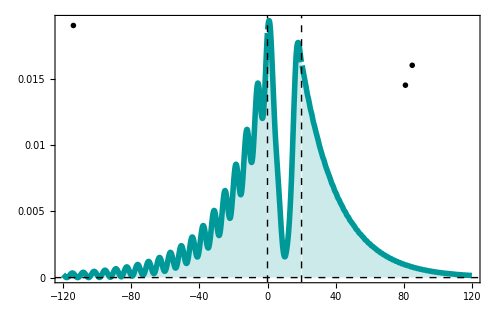

```mathematica
phi220bdn001=Plot[{Abs[ψ2[z]]^2n^2},{z,-6tc,6tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi_1(\\tau)|^2"},Magnification->1.8],PlotStyle->{{Thickness[0.008],color1}},Evaluate@plotStyle,ImageSize->500,PlotStyle->{{Thickness[0.008],color1}},Filling->Axis,Evaluate@plotStyle,FrameTicks->{{{0,0.005,0.01,0.015,0.02,0.06},None},{Automatic,None}},Epilog->{Inset[MaTeX["\\text{(d)}",Magnification->1.8],{-114,0.019}],Inset[MaTeX["\\tau_\\text{c}=20",Magnification->1.6],{85,0.016}],Inset[MaTeX["\\delta \\text{n}_{\\text{max}}=0.01",Magnification->1.6],{81,0.0145}]}]
```

```mathematica
Export["phi2_tc20b_dn001.pdf",phi220bdn001]
```

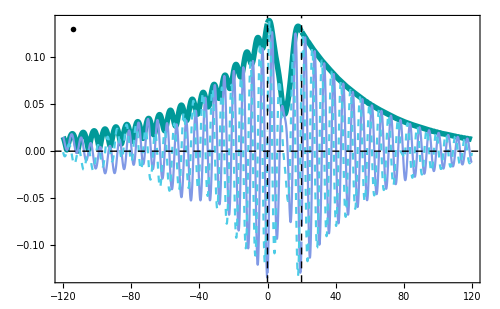

```mathematica
phi20bdn001=Plot[{Abs[ψ[z]]n,Re[ψ[z]]n,Im[ψ[z]]n},{z,-6tc,6tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau","|\\phi_1(\\tau)|"},Magnification->1.8],PlotStyle->{{Thickness[0.008],color1},{{},color2},{Dashed,color3}},Evaluate@plotStyle,ImageSize->500,Epilog->{Inset[MaTeX["\\text{(d)}",Magnification->1.8],{-114,0.13}]}]
```

```mathematica
Export["phi_tc20b_dn001.pdf",phi20bdn001]
```

phi_tc6_dn0.05.pdf

Continuity of the absolute value of ψ (color1), ψ’(color1),ψ’’ (green), ψ’’’ (purple). As expected, only the first three are zero at the borders of the cavity

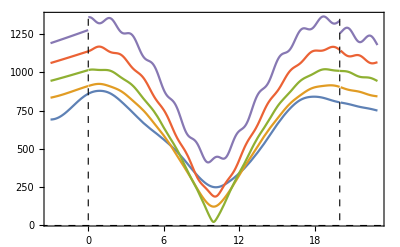

```mathematica
Plot[{Abs[ψ[z]],Abs[ψ'[z]],Abs[ψ''[z]],Abs[ψ'''[z]],Abs[ψ''''[z]]},{z,-3,tc+3},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau","Continuity"},Magnification->1.5],Evaluate@plotStyle]
```

Details of the continuity in the borders of the cavity

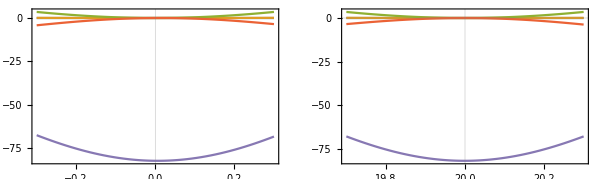

```mathematica
GraphicsRow[{
Plot[{Abs[ψ1t[z]]-Abs[ψ2t[z]],Abs[ψ1t'[z]]-Abs[ψ2t'[z]],Abs[ψ1t''[z]]-Abs[ψ2t''[z]],Abs[ψ1t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ1t''''[z]]-Abs[ψ2t''''[z]]},{z,-0.3,0.3},GridLines->{{0,tc},{}},Frame->True,Axes->False,PlotRange->All],
Plot[{Abs[ψ3t[z]]-Abs[ψ2t[z]],Abs[ψ3t'[z]]-Abs[ψ2t'[z]],Abs[ψ3t''[z]]-Abs[ψ2t''[z]],Abs[ψ3t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ3t''''[z]]-Abs[ψ2t''''[z]]},{z,tc-0.3,tc+.3},GridLines->{{0,tc},{0}},Frame->True,Axes->False,PlotRange->All]},ImageSize->600]
```

### Plot the solution ψ τ_c=20, δn=0.05,a (B)

```mathematica
wTest=0.3542527+I 5.025*^-6
tc
```

0.354253+5.025×10^-6 ⅈ

20

Calculo de las amplitudes en la región I dadas c1=1 y c2=ρ.  (Recordar que a1=a2=0)

```mathematica
a1t=a1/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a2t=a2/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a3t=a3/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a4t=a4/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
```

0.00256958+0.00559717 ⅈ

0.-5.55112×10^-17 ⅈ

86.9583+85.4926 ⅈ

-10.447+8.07893 ⅈ

```mathematica
c1t=1
c2t=rho4[Re[wTest],Im[wTest]]
c3t=0
c4t=0
```

1

-32.2422-118.062 ⅈ

0

0

w11 (ω_(1u))⟶ Im<0.  a1=0. Decae en la región III. c1=01
w12 (ω_(1ur))⟶ Im<0. a2=0. Decae en la región III. c2=ρ
w13 (ω_(1ul))⟶ Im>0. a3=Free. Decae en la regiónI. c3=0
w14 (ω_(1v))⟶ Im>0. a4=Free. Decae en la regiónI. c3=0
w21 (ω_(2u))⟶  Estado confinado
w22 (ω_(2ur))⟶ Estado confinado 
w23 (ω_(2ul))⟶  Estado confinado 
w24 (ω_(2v))⟶  Estado confinado

```mathematica
{w11[Re[wTest],Im[wTest]],w12[Re[wTest],Im[wTest]],w13[Re[wTest],Im[wTest]],w14[Re[wTest],Im[wTest]]}
{w21[Re[wTest],Im[wTest]],w22[Re[wTest],Im[wTest]],w23[Re[wTest],Im[wTest]],w24[Re[wTest],Im[wTest]]}
```

{-2.30648-4.49636×10^-6 ⅈ,1.08071-0.363233 ⅈ,1.08068+0.363235 ⅈ,0.139398+1.973×10^-6 ⅈ}

{-2.40952-4.29078×10^-6 ⅈ,1.25824-0.0000518735 ⅈ,1.00909+0.000054152 ⅈ,0.14219+2.01223×10^-6 ⅈ}

Calculo de las amplitudes en la región I. 
Forma1:ψ_I=ψ_I
Forma 2:  ψ_I=(Jump^-1.P_L.Jump)ψ_III

```mathematica
amp1t={0a1t , 0a2t,a3t,a4t};
ψ1t[τ_]=(amp1t.solsub/.wrule[Re[wTest],Im[wTest]])
amp1t2=ijump.propaL.jump.{c1t,c2t,c3t,c4t};
ψ1t2[τ_]=Chop[amp1t2.solsub/.wrule[Re[wTest],Im[wTest]]]
```

(0.+0. ⅈ)-(10.447-8.07893 ⅈ) ⅇ^((1.973×10^-6-0.139398 ⅈ) τ)+(86.9583+85.4926 ⅈ) ⅇ^((0.363235-1.08068 ⅈ) τ)

(0.00256958+0.00559717 ⅈ) ⅇ^((-4.49636×10^-6+2.30648 ⅈ) τ)-(10.447-8.07893 ⅈ) ⅇ^((1.973×10^-6-0.139398 ⅈ) τ)+(86.9583+85.4926 ⅈ) ⅇ^((0.363235-1.08068 ⅈ) τ)

Calculo de las amplitudes en la región II. 
Forma1: ψ_II=(P_L.Jump)ψ_III
Forma 2: ψ_II=(Jump)ψ_I

```mathematica
amp2t=jump.{0a1t ,0a2t,a3t,a4t}//Simplify;
amp2t2=propaL.jump.{c1t, c2t,c3t,c4t};
ψ2t[τ_]=amp2t.solsup/.wrule[Re[wTest],Im[wTest]]
ψ2t2[τ_]=amp2t2.solsup/.wrule[Re[wTest],Im[wTest]]
```

(-136.087+77.0364 ⅈ) ⅇ^((-0.0000518735-1.25824 ⅈ) τ)+(0.093191+0.56703 ⅈ) ⅇ^((-4.29078×10^-6+2.40952 ⅈ) τ)-(21.3155+15.4637 ⅈ) ⅇ^((2.01223×10^-6-0.14219 ⅈ) τ)+(233.82+31.4318 ⅈ) ⅇ^((0.000054152-1.00909 ⅈ) τ)

(-136.085+77.041 ⅈ) ⅇ^((-0.0000518735-1.25824 ⅈ) τ)+(0.0955154+0.572092 ⅈ) ⅇ^((-4.29078×10^-6+2.40952 ⅈ) τ)-(21.3142+15.461 ⅈ) ⅇ^((2.01223×10^-6-0.14219 ⅈ) τ)+(233.817+31.4249 ⅈ) ⅇ^((0.000054152-1.00909 ⅈ) τ)

```mathematica
Abs[ψ1t[0]]
Abs[ψ2t[0]]
Abs[ψ1t2[0]]
Abs[ψ2t2[0]]
```

120.87

120.87

120.876

120.876

La funciones en la región III, estaran desfasadas debido al salto entre la región II y III en una cantidad tc. Esto se corrige con el cambio ψ_III(τ)⟶ψ_III(τ-tc) o teniendo en cuenta dicha fase.  ψ_III=(Jump^-1.P_L1.P_R.Jump)ψ_I

```mathematica
propaR1=DiagonalMatrix[{Exp[-I w1sub tc],Exp[-I w2sub tc],Exp[-I w3sub tc],Exp[-I w4sub tc]}];
propaL1=DiagonalMatrix[{Exp[I w1sub tc],Exp[I w2sub tc],Exp[I w3sub tc],Exp[I w4sub tc]}];
```

```mathematica
amp3t=Simplify[propaL1.ijump.propaR.amp2t]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t[τ_]=amp3t.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
amp3t2=Simplify[propaL1.{c1t,c2t,c3t,c4t}]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t2[τ_]=amp3t2.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
```

(104918.+139906. ⅈ) ⅇ^((-0.363233-1.08071 ⅈ) τ)-(0.539014+0.838051 ⅈ) ⅇ^((-4.49636×10^-6+2.30648 ⅈ) τ)-(0.00251714-0.001571 ⅈ) ⅇ^((1.973×10^-6-0.139398 ⅈ) τ)+(2.11848×10^-6+7.78974×10^-7 ⅈ) ⅇ^((0.363235-1.08068 ⅈ) τ)

(104924.+139903. ⅈ) ⅇ^((-0.363233-1.08071 ⅈ) τ)-(0.545202+0.838412 ⅈ) ⅇ^((-4.49636×10^-6+2.30648 ⅈ) τ)

```mathematica
Abs[ψ2t[tc]]
Abs[ψ2t2[tc]]
Abs[ψ3t[tc]]
Abs[ψ3t2[tc]]
```

122.124

122.126

122.124

122.126

```mathematica
ψ[τ_]:=Piecewise[{{ψ3t[τ],τ≥tc},{ψ2t[τ],0<τ<tc},{ψ1t[τ],τ≤0}}]
ψ2[τ_]:=Piecewise[{{ψ3t2[τ],τ≥tc},{ψ2t2[τ],0<τ<tc},{ψ1t2[τ],τ≤0}}]
```

Norma del estado ∫n^2|ψ|^2 ⅆx=1,  se integra entre -10tc y 10tc para realizar más rapido el calculo.
Por lo cual n=1/ √(∫| ψ |^2ⅆx)

```mathematica
Norma=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-10tc,10tc}]
```

2.05917×10^6+0. ⅈ

```mathematica
NormaI=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-10tc,0}]
```

58133.6+0. ⅈ

```mathematica
NormaI=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-10tc,0}]/Norma (*Propabilidad de encontrar el campo en la zona I*)
NormaII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,0,tc}]/Norma(*Propabilidad de encontrar el campo en la zona II*)
NormaIII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,tc,10tc}]/Norma(*Propabilidad de encontrar el campo en la zona III*)
```

0.0282316+0. ⅈ

0.961703+0. ⅈ

0.0100657+0. ⅈ

```mathematica
NormaI+NormaII+NormaIII(*Propabilidad de encontrar el campo en todo el espacio es aprox 1*)
```

1.+0. ⅈ

Para este estado existe una probabilidad del 97% de encontrar el campo dentro de la cavidad y 13% de encontrarlo fuera.

```mathematica
n=1/Sqrt[Norma]
```

0.000696873+0. ⅈ

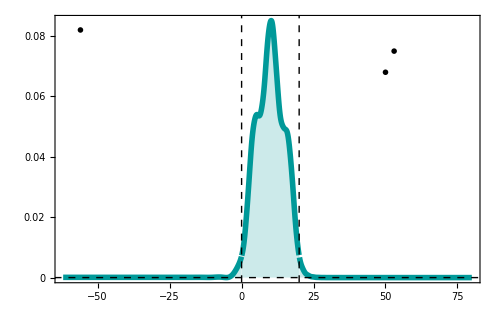

```mathematica
phi220adn005=Plot[{Abs[ψ2[z]]^2n^2},{z,-3.1tc,4tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi_0(\\tau)|^2"},Magnification->1.8],PlotStyle->{{Thickness[0.008],color1}},Filling->Axis,Evaluate@plotStyle,FrameTicks->{{{0,0.02,0.04,0.06,0.08,0.1,0.2},None},{Automatic,None}},ImageSize->500,Epilog->{Inset[MaTeX["\\text{(h)}",Magnification->1.8],{-56,0.082}],Inset[MaTeX["\\tau_\\text{c}=20",Magnification->1.6],{53,0.075}],Inset[MaTeX["\\delta \\text{n}_{\\text{max}}=0.05",Magnification->1.6],{50,0.068}]}]
```

```mathematica
Export["phi2_tc20a_dn005.pdf",phi220adn005]
```

phi2_tc20a_dn005.pdf

Continuity of real (color1) , imaginary (color1) and  absolute value (green) of ψ

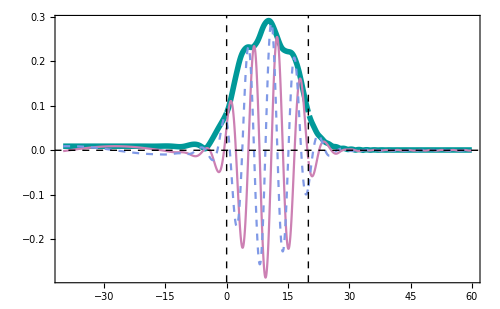

```mathematica
phi20adn005=Plot[{Abs[ψ2[z]]n,Re[ψ2[z]]n,Im[ψ2[z]]n},{z,-2tc,3tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi(\\tau)|"},Magnification->1.5],PlotStyle->{{Thickness[0.008],color1},{{},color5},{Dashed,color4}},Evaluate@plotStyle,ImageSize->500]
```

```mathematica
Export["phi_tc20_dn005.pdf",phi20adn005]
```

phi_tc20_dn005.pdf

Continuity of the absolute value of ψ (color1), ψ’(color1),ψ’’ (green), ψ’’’ (purple). As expected, only the first three are zero at the borders of the cavity

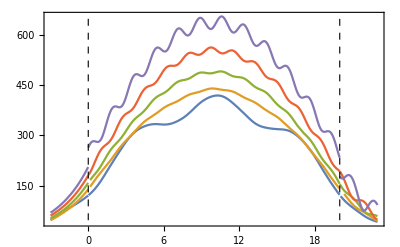

```mathematica
Plot[{Abs[ψ[z]],Abs[ψ'[z]],Abs[ψ''[z]],Abs[ψ'''[z]],Abs[ψ''''[z]]},{z,-3,tc+3},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau","Continuity"},Magnification->1.5],Evaluate@plotStyle]
```

Details of the continuity in the borders of the cavity

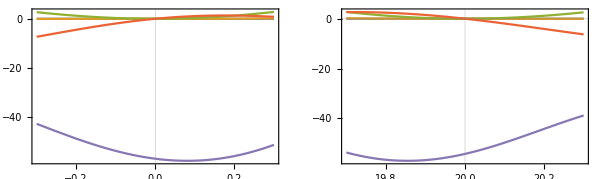

```mathematica
GraphicsRow[{
Plot[{Abs[ψ1t[z]]-Abs[ψ2t[z]],Abs[ψ1t'[z]]-Abs[ψ2t'[z]],Abs[ψ1t''[z]]-Abs[ψ2t''[z]],Abs[ψ1t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ1t''''[z]]-Abs[ψ2t''''[z]]},{z,-0.3,0.3},GridLines->{{0,tc},{}},Frame->True,Axes->False,PlotRange->All],
Plot[{Abs[ψ3t[z]]-Abs[ψ2t[z]],Abs[ψ3t'[z]]-Abs[ψ2t'[z]],Abs[ψ3t''[z]]-Abs[ψ2t''[z]],Abs[ψ3t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ3t''''[z]]-Abs[ψ2t''''[z]]},{z,tc-0.3,tc+.3},GridLines->{{0,tc},{0}},Frame->True,Axes->False,PlotRange->All]},ImageSize->600]
```

### Plot the solution ψ τ_c=20, δn=0.05,b

```mathematica
wTest=0.33726325+I 0.0000258
tc
```

0.337263+0.0000258 ⅈ

20

Calculo de las amplitudes en la región I dadas c1=1 y c2=ρ.  (Recordar que a1=a2=0)

```mathematica
a1t=a1/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a2t=a2/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a3t=a3/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a4t=a4/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
```

-0.0033453-0.000932852 ⅈ

1.11022×10^-16-2.22045×10^-16 ⅈ

-106.213+70.5171 ⅈ

-43.6237+30.2974 ⅈ

```mathematica
c1t=1
c2t=rho4[Re[wTest],Im[wTest]]
c3t=0
c4t=0
```

1

-124.522+25.0514 ⅈ

0

0

```mathematica
Abs[c2t]^2+Abs[1]^2
```

16134.4

```mathematica
Abs[a1t]^2+Abs[a2t]^2+Abs[a3t]^2+Abs[a4t]^2
```

19074.9

w11 (ω_(1u))⟶ Im<0.  a1=Free. Decae en la región I. c1=0 
w12 (ω_(1ur))⟶ Im<0. a2=Free. Decae en la región I. c2=0
w13 (ω_(1ul))⟶ Im>0. a3=0. Decae en la regiónIII. c3=1
w14 (ω_(1v))⟶ Im>0. a4=0. Decae en la regiónIII. c3=ρ
w21 (ω_(2u))⟶  Estado confinado
w22 (ω_(2ur))⟶ Estado confinado 
w23 (ω_(2ul))⟶  Estado confinado 
w24 (ω_(2v))⟶  Estado confinado

```mathematica
{w11[Re[wTest],Im[wTest]],w12[Re[wTest],Im[wTest]],w13[Re[wTest],Im[wTest]],w14[Re[wTest],Im[wTest]]}
{w21[Re[wTest],Im[wTest]],w22[Re[wTest],Im[wTest]],w23[Re[wTest],Im[wTest]],w24[Re[wTest],Im[wTest]]}
```

{-2.29118-0.0000234064 ⅈ,1.07663-0.29452 ⅈ,1.0764+0.294533 ⅈ,0.132727+0.0000101331 ⅈ}

{-2.39492-0.0000223107 ⅈ,1.37544-0.000133145 ⅈ,0.884098+0.000145121 ⅈ,0.135385+0.0000103348 ⅈ}

Calculo de las amplitudes en la región I. 
Forma1:ψ_I=ψ_I
Forma 2:  ψ_I=(Jump^-1.P_L.Jump)ψ_III

```mathematica
amp1t={0a1t , 0a2t,a3t,a4t};
ψ1t[τ_]=(amp1t.solsub/.wrule[Re[wTest],Im[wTest]])
amp1t2=ijump.propaL.jump.{c1t,c2t,c3t,c4t};
ψ1t2[τ_]=Chop[amp1t2.solsub/.wrule[Re[wTest],Im[wTest]]]
```

(0.+0. ⅈ)-(43.6237-30.2974 ⅈ) ⅇ^((0.0000101331-0.132727 ⅈ) τ)-(106.213-70.5171 ⅈ) ⅇ^((0.294533-1.0764 ⅈ) τ)

(-0.0033453-0.000932852 ⅈ) ⅇ^((-0.0000234064+2.29118 ⅈ) τ)-(43.6237-30.2974 ⅈ) ⅇ^((0.0000101331-0.132727 ⅈ) τ)-(106.213-70.5171 ⅈ) ⅇ^((0.294533-1.0764 ⅈ) τ)

Calculo de las amplitudes en la región II. 
Forma1: ψ_II=(P_L.Jump)ψ_III
Forma 2: ψ_II=(Jump)ψ_I

```mathematica
amp2t=jump.{0a1t ,0a2t,a3t,a4t}//Simplify;
amp2t2=propaL.jump.{c1t, c2t,c3t,c4t};
ψ2t[τ_]=amp2t.solsup/.wrule[Re[wTest],Im[wTest]]
ψ2t2[τ_]=amp2t2.solsup/.wrule[Re[wTest],Im[wTest]]
```

(-47.0509-47.7758 ⅈ) ⅇ^((-0.000133145-1.37544 ⅈ) τ)-(0.595291-0.0431074 ⅈ) ⅇ^((-0.0000223107+2.39492 ⅈ) τ)-(17.0612-22.5272 ⅈ) ⅇ^((0.0000103348-0.135385 ⅈ) τ)-(85.1298-126.02 ⅈ) ⅇ^((0.000145121-0.884098 ⅈ) τ)

(-47.052-47.7761 ⅈ) ⅇ^((-0.000133145-1.37544 ⅈ) τ)-(0.598313-0.0422649 ⅈ) ⅇ^((-0.0000223107+2.39492 ⅈ) τ)-(17.0629-22.5267 ⅈ) ⅇ^((0.0000103348-0.135385 ⅈ) τ)-(85.1272-126.021 ⅈ) ⅇ^((0.000145121-0.884098 ⅈ) τ)

```mathematica
Abs[ψ1t[0]]
Abs[ψ2t[0]]
Abs[ψ1t2[0]]
Abs[ψ2t2[0]]
```

180.596

180.596

180.598

180.598

La funciones en la región III, estaran desfasadas debido al salto entre la región II y III en una cantidad tc. Esto se corrige con el cambio ψ_III(τ)⟶ψ_III(τ-tc) o teniendo en cuenta dicha fase.  ψ_III=(Jump^-1.P_L1.P_R.Jump)ψ_I

```mathematica
propaR1=DiagonalMatrix[{Exp[-I w1sub tc],Exp[-I w2sub tc],Exp[-I w3sub tc],Exp[-I w4sub tc]}];
propaL1=DiagonalMatrix[{Exp[I w1sub tc],Exp[I w2sub tc],Exp[I w3sub tc],Exp[I w4sub tc]}];
```

```mathematica
amp3t=Simplify[propaL1.ijump.propaR.amp2t]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t[τ_]=amp3t.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
amp3t2=Simplify[propaL1.{c1t,c2t,c3t,c4t}]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t2[τ_]=amp3t2.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
```

(36361.1-28050.2 ⅈ) ⅇ^((-0.29452-1.07663 ⅈ) τ)-(0.269691+0.961638 ⅈ) ⅇ^((-0.0000234064+2.29118 ⅈ) τ)+(0.000859864+0.0000341794 ⅈ) ⅇ^((0.0000101331-0.132727 ⅈ) τ)+(3.46731×10^-6+5.05469×10^-6 ⅈ) ⅇ^((0.294533-1.0764 ⅈ) τ)

(36360.4-28050.7 ⅈ) ⅇ^((-0.29452-1.07663 ⅈ) τ)-(0.267273+0.964107 ⅈ) ⅇ^((-0.0000234064+2.29118 ⅈ) τ)

```mathematica
Abs[ψ2t[tc]]
Abs[ψ2t2[tc]]
Abs[ψ3t[tc]]
Abs[ψ3t2[tc]]
```

126.039

126.037

126.039

126.037

```mathematica
ψ[τ_]:=Piecewise[{{ψ3t[τ],τ≥tc},{ψ2t[τ],0<τ<tc},{ψ1t[τ],τ≤0}}]
ψ2[τ_]:=Piecewise[{{ψ3t2[τ],τ≥tc},{ψ2t2[τ],0<τ<tc},{ψ1t2[τ],τ≤0}}]
```

Norma del estado ∫n^2|ψ|^2 ⅆx=1,  se integra entre -10tc y 10tc para realizar más rapido el calculo.
Por lo cual n=1/ √(∫| ψ |^2ⅆx)

```mathematica
Norma=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-100tc,100tc}]
```

6.24759×10^6+0. ⅈ

594451.+0. ⅈ

```mathematica
NormaI=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-100tc,0}]/Norma (*Propabilidad de encontrar el campo en la zona I*)
NormaII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,0,100tc}]/Norma(*Propabilidad de encontrar el campo en la zona II*)
NormaIII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,tc,100tc}]/Norma(*Propabilidad de encontrar el campo en la zona III*)
```

0.890025+0. ⅈ

0.109975+0. ⅈ

0.00468799+0. ⅈ

```mathematica
NormaI+NormaII+NormaIII(*Propabilidad de encontrar el campo en todo el espacio es aprox 1*)
```

1.00469+0. ⅈ

Para este estado existe una probabilidad del 10% de encontrar el campo dentro de la cavidad y 90% de encontrarlo fuera.

```mathematica
n=1/Sqrt[Norma]
```

0.000400077+0. ⅈ

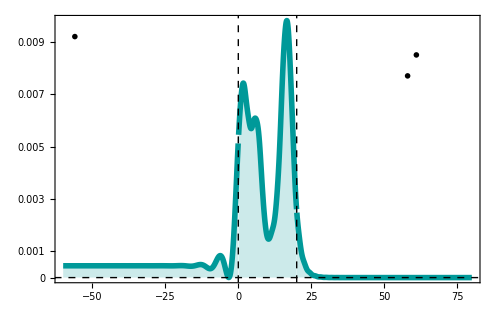

```mathematica
phi220bdn005=Plot[{Abs[ψ2[z]]^2n^2},{z,-3tc,4tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi_1(\\tau)|^2"},Magnification->1.8],PlotStyle->{{Thickness[0.008],color1}},Filling->Axis,Evaluate@plotStyle,FrameTicks->{{{0,0.001,0.003,0.005,0.007,0.009,0.2},None},{Automatic,None}},ImageSize->500,Epilog->{Inset[MaTeX["\\text{(i)}",Magnification->1.8],{-56,0.0092}],Inset[MaTeX["\\tau_\\text{c}=20",Magnification->1.6],{61,0.0085}],Inset[MaTeX["\\delta \\text{n}_{\\text{max}}=0.05",Magnification->1.6],{58,0.0077}]},GridLines->{{0,tc},{0}}]
```

```mathematica
Export["phi2_tc20b_dn0.05.pdf",phi220bdn005]
```

phi2_tc20b_dn0.05.pdf

Continuity of real (color1) , imaginary (color1) and  absolute value (green) of ψ

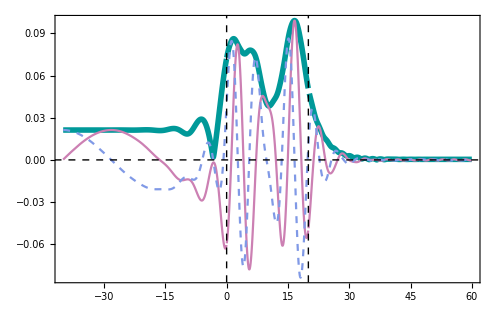

```mathematica
phi20bdn005=Plot[{Abs[ψ2[z]]n,Re[ψ2[z]]n,Im[ψ2[z]]n},{z,-2tc,3tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi(\\tau)|"},Magnification->1.5],PlotStyle->{{Thickness[0.008],color1},{{},color5},{Dashed,color4}},Evaluate@plotStyle,ImageSize->500]
```

```mathematica
Export["phi_tc20b_dn005.pdf",phi20bdn005]
```

phi_tc20b_dn005.pdf

Continuity of the absolute value of ψ (color1), ψ’(color1),ψ’’ (green), ψ’’’ (purple). As expected, only the first three are zero at the borders of the cavity

```mathematica
Plot[{Abs[ψ[z]],Abs[ψ'[z]],Abs[ψ''[z]],Abs[ψ'''[z]],Abs[ψ''''[z]]},{z,-3,tc+3},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau","Continuity"},Magnification->1.5],Evaluate@plotStyle]
```

-Graphics-

Details of the continuity in the borders of the cavity

```mathematica
GraphicsRow[{
Plot[{Abs[ψ1t[z]]-Abs[ψ2t[z]],Abs[ψ1t'[z]]-Abs[ψ2t'[z]],Abs[ψ1t''[z]]-Abs[ψ2t''[z]],Abs[ψ1t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ1t''''[z]]-Abs[ψ2t''''[z]]},{z,-0.3,0.3},GridLines->{{0,tc},{}},Frame->True,Axes->False,PlotRange->All],
Plot[{Abs[ψ3t[z]]-Abs[ψ2t[z]],Abs[ψ3t'[z]]-Abs[ψ2t'[z]],Abs[ψ3t''[z]]-Abs[ψ2t''[z]],Abs[ψ3t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ3t''''[z]]-Abs[ψ2t''''[z]]},{z,tc-0.3,tc+.3},GridLines->{{0,tc},{0}},Frame->True,Axes->False,PlotRange->All]},ImageSize->600]
```

-Graphics-

```mathematica
ContourPlot[Abs[1/a1/.wrule[wpRe,wpIm]/.ρ->rho4[wpRe,wpIm]]^(1/4),{wpRe,0.31,0.33},{wpIm,0,0.002},PlotLegends->Automatic,PlotPoints->10,FrameLabel->{"Re(W')","Im(W')"},ColorFunction->ColorData["color1GreenYellow"],Contours->{Automatic,10}]
```

### Plot the solution ψ τ_c=20, δn=0.05,c

```mathematica
wTest=0.312921+I 0.0000116
tc
```

0.312921+0.0000116 ⅈ

20

Calculo de las amplitudes en la región I dadas c1=1 y c2=ρ.  (Recordar que a1=a2=0)

```mathematica
a1t=a1/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a2t=a2/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a3t=a3/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a4t=a4/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
```

0.00575582-0.00221985 ⅈ

0.-3.33067×10^-16 ⅈ

42.6431+232.645 ⅈ

-42.663+22.8107 ⅈ

```mathematica
c1t=1
c2t=rho4[Re[wTest],Im[wTest]]
c3t=0
c4t=0
```

1

-40.2229-233.299 ⅈ

0

0

```mathematica
Abs[c2t]^2+Abs[1]^2
```

56047.3

```mathematica
Abs[a1t]^2+Abs[a2t]^2+Abs[a3t]^2+Abs[a4t]^2
```

58282.7

w11 (ω_(1u))⟶ Im<0.  a1=Free. Decae en la región I. c1=0 
w12 (ω_(1ur))⟶ Im<0. a2=Free. Decae en la región I. c2=0
w13 (ω_(1ul))⟶ Im>0. a3=0. Decae en la regiónIII. c3=1
w14 (ω_(1v))⟶ Im>0. a4=0. Decae en la regiónIII. c3=ρ
w21 (ω_(2u))⟶  Estado confinado
w22 (ω_(2ur))⟶ Estado confinado 
w23 (ω_(2ul))⟶  Estado confinado 
w24 (ω_(2v))⟶  Estado confinado

```mathematica
{w11[Re[wTest],Im[wTest]],w12[Re[wTest],Im[wTest]],w13[Re[wTest],Im[wTest]],w14[Re[wTest],Im[wTest]]}
{w21[Re[wTest],Im[wTest]],w22[Re[wTest],Im[wTest]],w23[Re[wTest],Im[wTest]],w24[Re[wTest],Im[wTest]]}
```

{-2.26887-0.0000107409 ⅈ,1.07044-0.145905 ⅈ,1.07023+0.145911 ⅈ,0.123164+4.55787×10^-6 ⅈ}

{-2.37367-0.0000102203 ⅈ,1.47791-0.0000411633 ⅈ,0.770132+0.0000467349 ⅈ,0.125632+4.64871×10^-6 ⅈ}

Calculo de las amplitudes en la región I. 
Forma1:ψ_I=ψ_I
Forma 2:  ψ_I=(Jump^-1.P_L.Jump)ψ_III

```mathematica
amp1t={0a1t , 0a2t,a3t,a4t};
ψ1t[τ_]=(amp1t.solsub/.wrule[Re[wTest],Im[wTest]])
amp1t2=ijump.propaL.jump.{c1t,c2t,c3t,c4t};
ψ1t2[τ_]=Chop[amp1t2.solsub/.wrule[Re[wTest],Im[wTest]]]
```

(0.+0. ⅈ)-(42.663-22.8107 ⅈ) ⅇ^((4.55787×10^-6-0.123164 ⅈ) τ)+(42.6431+232.645 ⅈ) ⅇ^((0.145911-1.07023 ⅈ) τ)

(0.00575582-0.00221985 ⅈ) ⅇ^((-0.0000107409+2.26887 ⅈ) τ)-(42.663-22.8107 ⅈ) ⅇ^((4.55787×10^-6-0.123164 ⅈ) τ)+(42.6431+232.645 ⅈ) ⅇ^((0.145911-1.07023 ⅈ) τ)

Calculo de las amplitudes en la región II. 
Forma1: ψ_II=(P_L.Jump)ψ_III
Forma 2: ψ_II=(Jump)ψ_I

```mathematica
amp2t=jump.{0a1t ,0a2t,a3t,a4t}//Simplify;
amp2t2=propaL.jump.{c1t, c2t,c3t,c4t};
ψ2t[τ_]=amp2t.solsup/.wrule[Re[wTest],Im[wTest]]
ψ2t2[τ_]=amp2t2.solsup/.wrule[Re[wTest],Im[wTest]]
```

(-31.7949+63.0068 ⅈ) ⅇ^((-0.0000411633-1.47791 ⅈ) τ)-(0.0899478-1.07742 ⅈ) ⅇ^((-0.0000102203+2.37367 ⅈ) τ)-(44.5021+31.1362 ⅈ) ⅇ^((4.64871×10^-6-0.125632 ⅈ) τ)+(76.367+222.508 ⅈ) ⅇ^((0.0000467349-0.770132 ⅈ) τ)

(-31.7937+63.0063 ⅈ) ⅇ^((-0.0000411633-1.47791 ⅈ) τ)-(0.0847622-1.07542 ⅈ) ⅇ^((-0.0000102203+2.37367 ⅈ) τ)-(44.4989+31.1374 ⅈ) ⅇ^((4.64871×10^-6-0.125632 ⅈ) τ)+(76.3632+222.509 ⅈ) ⅇ^((0.0000467349-0.770132 ⅈ) τ)

```mathematica
Abs[ψ1t[0]]
Abs[ψ2t[0]]
Abs[ψ1t2[0]]
Abs[ψ2t2[0]]
```

255.456

255.456

255.454

255.454

La funciones en la región III, estaran desfasadas debido al salto entre la región II y III en una cantidad tc. Esto se corrige con el cambio ψ_III(τ)⟶ψ_III(τ-tc) o teniendo en cuenta dicha fase.  ψ_III=(Jump^-1.P_L1.P_R.Jump)ψ_I

```mathematica
propaR1=DiagonalMatrix[{Exp[-I w1sub tc],Exp[-I w2sub tc],Exp[-I w3sub tc],Exp[-I w4sub tc]}];
propaL1=DiagonalMatrix[{Exp[I w1sub tc],Exp[I w2sub tc],Exp[I w3sub tc],Exp[I w4sub tc]}];
```

```mathematica
amp3t=Simplify[propaL1.ijump.propaR.amp2t]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t[τ_]=amp3t.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
amp3t2=Simplify[propaL1.{c1t,c2t,c3t,c4t}]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t2[τ_]=amp3t2.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
```

(2996.16+3196.53 ⅈ) ⅇ^((-0.145905-1.07044 ⅈ) τ)+(0.17587-0.99091 ⅈ) ⅇ^((-0.0000107409+2.26887 ⅈ) τ)+(0.000079262-0.000782278 ⅈ) ⅇ^((4.55787×10^-6-0.123164 ⅈ) τ)+(0.0000710701-0.000232621 ⅈ) ⅇ^((0.145911-1.07023 ⅈ) τ)

(2996.16+3196.45 ⅈ) ⅇ^((-0.145905-1.07044 ⅈ) τ)+(0.17489-0.984806 ⅈ) ⅇ^((-0.0000107409+2.26887 ⅈ) τ)

```mathematica
Abs[ψ2t[tc]]
Abs[ψ2t2[tc]]
Abs[ψ3t[tc]]
Abs[ψ3t2[tc]]
```

236.573

236.573

236.573

«1 more identical outputs»

```mathematica
ψ[τ_]:=Piecewise[{{ψ3t[τ],τ≥tc},{ψ2t[τ],0<τ<tc},{ψ1t[τ],τ≤0}}]
ψ2[τ_]:=Piecewise[{{ψ3t2[τ],τ≥tc},{ψ2t2[τ],0<τ<tc},{ψ1t2[τ],τ≤0}}]
```

Norma del estado ∫n^2|ψ|^2 ⅆx=1,  se integra entre -10tc y 10tc para realizar más rapido el calculo.
Por lo cual n=1/ √(∫| ψ |^2ⅆx)

```mathematica
Norma=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-10tc,10tc}]
Norma1=Integrate[ψ[x]*Conjugate[ψ[x]],{x,-3tc,3tc}]
```

2.18886×10^6+0. ⅈ

1.86142×10^6+0. ⅈ

```mathematica
NormaI=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-10tc,0}]
```

682955.+0. ⅈ

```mathematica
NormaI=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-10tc,0}]/Norma (*Propabilidad de encontrar el campo en la zona I*)
NormaII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,0,tc}]/Norma(*Propabilidad de encontrar el campo en la zona II*)
NormaIII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,tc,10tc}]/Norma(*Propabilidad de encontrar el campo en la zona III*)
```

0.312014+0. ⅈ

0.600222+0. ⅈ

0.0877642+0. ⅈ

```mathematica
NormaI+NormaII+NormaIII(*Propabilidad de encontrar el campo en todo el espacio es aprox 1*)
```

1.+0. ⅈ

Para este estado existe una probabilidad del 60% de encontrar el campo dentro de la cavidad y 40% de encontrarlo fuera.

```mathematica
n=1/Sqrt[Norma]
```

0.000675913+0. ⅈ

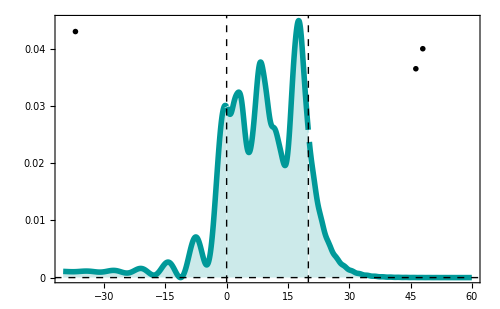

```mathematica
phi220cdn005=Plot[{Abs[ψ2[z]]^2n^2},{z,-2tc,3tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi_2(\\tau)|^2"},Magnification->1.8],PlotStyle->{{Thickness[0.008],color1}},Filling->Axis,Evaluate@plotStyle,FrameTicks->{{{0,0.01,0.02,0.03,0.04,0.05,0.06},None},{Automatic,None}},ImageSize->500,Epilog->{Inset[MaTeX["\\text{(j)}",Magnification->1.8],{-37,0.043}],Inset[MaTeX["\\tau_\\text{c}=20",Magnification->1.6],{48,0.040}],Inset[MaTeX["\\delta \\text{n}_{\\text{max}}=0.05",Magnification->1.6],{46.3,0.0365}]},GridLines->{{0,tc},{0}}]
```

```mathematica
Export["phi2_tc20c_dn005.pdf",phi220cdn005]
```

phi2_tc20c_dn005.pdf

```mathematica
Plot[{Abs[ψ2[z]]n,Re[ψ2[z]]n,Im[ψ2[z]]n},{z,-4tc,4tc},PlotRange-> {-3,3},GridLines->{{0,tc},{}},
PlotRange ->All,Frame->True,AspectRatio->1/GoldenRatio,ImageSize->500,FrameLabel->{"τ","|ϕ(τ)|"},FrameTicksStyle->Directive[FontFamily->"Helvetica",20,Plain],
LabelStyle->Directive[FontFamily->"Helvetica",25],GridLinesStyle->Directive[{color1,Dashed,Thickness[0.002]}]];
```

Continuity of real (color1) , imaginary (color1) and  absolute value (green) of ψ

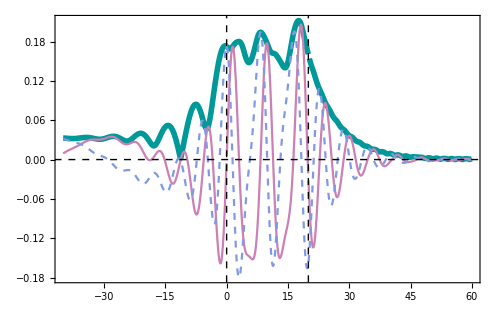

```mathematica
phi20cdn005=Plot[{Abs[ψ[z]]n,Re[ψ[z]]n,Im[ψ[z]]n},{z,-2tc,3tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi(\\tau)|"},Magnification->1.5],PlotStyle->{{Thickness[0.008],color1},{{},color5},{Dashed,color4}},Evaluate@plotStyle,ImageSize->500]
```

```mathematica
Export["phi_tc20c_dn0.05.pdf",phi20cdn005]
```

phi_tc20c_dn0.05.pdf

Continuity of the absolute value of ψ (color1), ψ’(color1),ψ’’ (green), ψ’’’ (purple). As expected, only the first three are zero at the borders of the cavity

```mathematica
Plot[{Abs[ψ[z]],Abs[ψ'[z]],Abs[ψ''[z]],Abs[ψ'''[z]],Abs[ψ''''[z]]},{z,-3,tc+3},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau","Continuity"},Magnification->1.5],Evaluate@plotStyle]
```

-Graphics-

Details of the continuity in the borders of the cavity

```mathematica
GraphicsRow[{
Plot[{Abs[ψ1t[z]]-Abs[ψ2t[z]],Abs[ψ1t'[z]]-Abs[ψ2t'[z]],Abs[ψ1t''[z]]-Abs[ψ2t''[z]],Abs[ψ1t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ1t''''[z]]-Abs[ψ2t''''[z]]},{z,-0.3,0.3},GridLines->{{0,tc},{}},Frame->True,Axes->False,PlotRange->All],
Plot[{Abs[ψ3t[z]]-Abs[ψ2t[z]],Abs[ψ3t'[z]]-Abs[ψ2t'[z]],Abs[ψ3t''[z]]-Abs[ψ2t''[z]],Abs[ψ3t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ3t''''[z]]-Abs[ψ2t''''[z]]},{z,tc-0.3,tc+.3},GridLines->{{0,tc},{0}},Frame->True,Axes->False,PlotRange->All]},ImageSize->600]
```

-Graphics-

```mathematica
ContourPlot[Abs[1/a1/.wrule[wpRe,wpIm]/.ρ->rho4[wpRe,wpIm]]^(1/4),{wpRe,0.31,0.33},{wpIm,0,0.002},PlotLegends->Automatic,PlotPoints->10,FrameLabel->{"Re(W')","Im(W')"},ColorFunction->ColorData["color1GreenYellow"],Contours->{Automatic,10}]
```

### Plot the solution ψ τ_c=20, δn=0.1,a

```mathematica
wTest=0.333575+I 0.00002128
tc
```

0.333575+0.00002128 ⅈ

20

Calculo de las amplitudes en la región I dadas c1=1 y c2=ρ.  (Recordar que a1=a2=0)

```mathematica
a1t=a1/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a2t=a2/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a3t=a3/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a4t=a4/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
```

0.464716-0.990429 ⅈ

-1.11022×10^-16-2.22045×10^-16 ⅈ

-51.6786+97.5249 ⅈ

-66.5161+69.7531 ⅈ

```mathematica
c1t=1
c2t=rho4[Re[wTest],Im[wTest]]
c3t=0
c4t=0
```

1

-53.6147-8.22783 ⅈ

0

0

w11 (ω_(1u))⟶ Im<0.  a1=0. Decae en la región III. c1=01
w12 (ω_(1ur))⟶ Im<0. a2=0. Decae en la región III. c2=ρ
w13 (ω_(1ul))⟶ Im>0. a3=Free. Decae en la regiónI. c3=0
w14 (ω_(1v))⟶ Im>0. a4=Free. Decae en la regiónI. c3=0
w21 (ω_(2u))⟶  Estado confinado
w22 (ω_(2ur))⟶ Estado confinado 
w23 (ω_(2ul))⟶  Estado confinado 
w24 (ω_(2v))⟶  Estado confinado

```mathematica
{w11[Re[wTest],Im[wTest]],w12[Re[wTest],Im[wTest]],w13[Re[wTest],Im[wTest]],w14[Re[wTest],Im[wTest]]}
{w21[Re[wTest],Im[wTest]],w22[Re[wTest],Im[wTest]],w23[Re[wTest],Im[wTest]],w24[Re[wTest],Im[wTest]]}
```

{-2.18355-0.0000203594 ⅈ,1.02209-0.470891 ⅈ,1.02196+0.470903 ⅈ,0.139495+8.87814×10^-6 ⅈ}

{-2.39173-0.0000184534 ⅈ,1.39374-0.00010168 ⅈ,0.864079+0.000111609 ⅈ,0.133908+8.52482×10^-6 ⅈ}

Calculo de las amplitudes en la región I. 
Forma1:ψ_I=ψ_I
Forma 2:  ψ_I=(Jump^-1.P_L.Jump)ψ_III

```mathematica
amp1t={0a1t , 0a2t,a3t,a4t};
ψ1t[τ_]=(amp1t.solsub/.wrule[Re[wTest],Im[wTest]])
amp1t2=ijump.propaL.jump.{c1t,c2t,c3t,c4t};
ψ1t2[τ_]=Chop[amp1t2.solsub/.wrule[Re[wTest],Im[wTest]]]
```

(0.+0. ⅈ)-(66.5161-69.7531 ⅈ) ⅇ^((8.87814×10^-6-0.139495 ⅈ) τ)-(51.6786-97.5249 ⅈ) ⅇ^((0.470903-1.02196 ⅈ) τ)

(-0.00522382+0.000548762 ⅈ) ⅇ^((-0.0000203594+2.18355 ⅈ) τ)-(40.387-26.9009 ⅈ) ⅇ^((8.87814×10^-6-0.139495 ⅈ) τ)-(35.1502-41.6658 ⅈ) ⅇ^((0.470903-1.02196 ⅈ) τ)

Calculo de las amplitudes en la región II. 
Forma1: ψ_II=(P_L.Jump)ψ_III
Forma 2: ψ_II=(Jump)ψ_I

```mathematica
amp2t=jump.{0a1t ,0a2t,a3t,a4t}//Simplify;
amp2t2=propaL.jump.{c1t, c2t,c3t,c4t};
ψ2t[τ_]=amp2t.solsup/.wrule[Re[wTest],Im[wTest]]
ψ2t2[τ_]=amp2t2.solsup/.wrule[Re[wTest],Im[wTest]]
```

(-52.6886-53.6093 ⅈ) ⅇ^((-0.00010168-1.39374 ⅈ) τ)-(1.01774-0.252764 ⅈ) ⅇ^((-0.0000184534+2.39173 ⅈ) τ)-(25.653-41.4472 ⅈ) ⅇ^((8.52482×10^-6-0.133908 ⅈ) τ)-(38.8353-179.187 ⅈ) ⅇ^((0.000111609-0.864079 ⅈ) τ)

(-19.821-31.3906 ⅈ) ⅇ^((-0.00010168-1.39374 ⅈ) τ)-(0.52178-0.0159157 ⅈ) ⅇ^((-0.0000184534+2.39173 ⅈ) τ)-(17.6963-17.5129 ⅈ) ⅇ^((8.52482×10^-6-0.133908 ⅈ) τ)-(37.5033-82.429 ⅈ) ⅇ^((0.000111609-0.864079 ⅈ) τ)

```mathematica
Abs[ψ1t[0]]
Abs[ψ2t[0]]
Abs[ψ1t2[0]]
Abs[ψ2t2[0]]
```

204.822

204.822

102.02

102.02

La funciones en la región III, estaran desfasadas debido al salto entre la región II y III en una cantidad tc. Esto se corrige con el cambio ψ_III(τ)⟶ψ_III(τ-tc) o teniendo en cuenta dicha fase.  ψ_III=(Jump^-1.P_L1.P_R.Jump)ψ_I

```mathematica
propaR1=DiagonalMatrix[{Exp[-I w1sub tc],Exp[-I w2sub tc],Exp[-I w3sub tc],Exp[-I w4sub tc]}];
propaL1=DiagonalMatrix[{Exp[I w1sub tc],Exp[I w2sub tc],Exp[I w3sub tc],Exp[I w4sub tc]}];
```

```mathematica
amp3t=Simplify[propaL1.ijump.propaR.amp2t]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t[τ_]=amp3t.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
amp3t2=Simplify[propaL1.{c1t,c2t,c3t,c4t}]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t2[τ_]=amp3t2.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
```

(-53895.2-1.35034×10^6 ⅈ) ⅇ^((-0.470891-1.02209 ⅈ) τ)+(2.00757+0.190986 ⅈ) ⅇ^((-0.0000203594+2.18355 ⅈ) τ)+(1.92889-0.593623 ⅈ) ⅇ^((8.87814×10^-6-0.139495 ⅈ) τ)-(1.09023×10^-7-7.60941×10^-7 ⅈ) ⅇ^((0.470903-1.02196 ⅈ) τ)

(115333.-657453. ⅈ) ⅇ^((-0.470891-1.02209 ⅈ) τ)+(0.952305+0.306479 ⅈ) ⅇ^((-0.0000203594+2.18355 ⅈ) τ)

```mathematica
Abs[ψ2t[tc]]
Abs[ψ2t2[tc]]
Abs[ψ3t[tc]]
Abs[ψ3t2[tc]]
```

109.826

53.2541

109.826

53.2541

```mathematica
ψ[τ_]:=Piecewise[{{ψ3t[τ],τ≥tc},{ψ2t[τ],0<τ<tc},{ψ1t[τ],τ≤0}}]
ψ2[τ_]:=Piecewise[{{ψ3t2[τ],τ≥tc},{ψ2t2[τ],0<τ<tc},{ψ1t2[τ],τ≤0}}]
```

Norma del estado ∫n^2|ψ|^2 ⅆx=1,  se integra entre -10tc y 10tc para realizar más rapido el calculo.
Por lo cual n=1/ √(∫| ψ |^2ⅆx)

```mathematica
Norma=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,0,tc}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {0.005, 0, 20}.

∫_0^20 (10427.5+0. ⅈ)ⅆ0.005

```mathematica
NormaI=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-10tc,0}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {0.005, -200, 0}.

∫_-200^0 (2542.58+0. ⅈ)ⅆ0.005

```mathematica
NormaI=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-10tc,0}]/Norma (*Propabilidad de encontrar el campo en la zona I*)
NormaII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,0,tc}]/Norma(*Propabilidad de encontrar el campo en la zona II*)
NormaIII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,tc,10tc}]/Norma(*Propabilidad de encontrar el campo en la zona III*)
```

Integrate::ilim: Invalid integration variable or limit(s) in {0.005, -200, 0}.

(∫_-200^0 (10427.5+0. ⅈ)ⅆ0.005)/(∫_0^20 (10427.5+0. ⅈ)ⅆ0.005)

Integrate::ilim: Invalid integration variable or limit(s) in {0.005, 0, 20}.

1

Integrate::ilim: Invalid integration variable or limit(s) in {0.005, 20, 200}.

(∫_20^200 (10427.5+0. ⅈ)ⅆ0.005)/(∫_0^20 (10427.5+0. ⅈ)ⅆ0.005)

```mathematica
NormaI+NormaII+NormaIII(*Propabilidad de encontrar el campo en todo el espacio es aprox 1*)
```

1.+0. ⅈ

Para este estado existe una probabilidad del 97% de encontrar el campo dentro de la cavidad y 13% de encontrarlo fuera.

```mathematica
n=1/Sqrt[Norma]
```

0.000696873+0. ⅈ

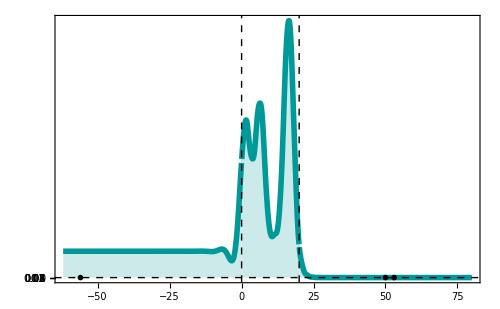

```mathematica
phi220adn005=Plot[{Abs[ψ2[z]]^2},{z,-3.1tc,4tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi_0(\\tau)|^2"},Magnification->1.8],PlotStyle->{{Thickness[0.008],color1}},Filling->Axis,Evaluate@plotStyle,FrameTicks->{{{0,0.02,0.04,0.06,0.08,0.1,0.2},None},{Automatic,None}},ImageSize->500,Epilog->{Inset[MaTeX["\\text{(h)}",Magnification->1.8],{-56,0.082}],Inset[MaTeX["\\tau_\\text{c}=20",Magnification->1.6],{53,0.075}],Inset[MaTeX["\\delta \\text{n}_{\\text{max}}=0.05",Magnification->1.6],{50,0.068}]}]
```

```mathematica
Export["phi2_tc20a_dn005.pdf",phi220adn005]
```

phi2_tc20a_dn005.pdf

```mathematica
n=1
```

1

Continuity of real (color1) , imaginary (color1) and  absolute value (green) of ψ

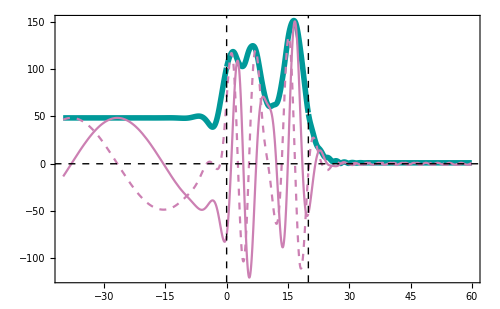

```mathematica
phi20adn005=Plot[{Abs[ψ2[z]]n,Re[ψ2[z]]n,Im[ψ2[z]]n},{z,-2tc,3tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi(\\tau)|"},Magnification->1.5],PlotStyle->{{Thickness[0.008],color1},{{},color5},{Dashed,color4}},Evaluate@plotStyle,ImageSize->500]
```

```mathematica
Export["phi_tc20_dn005.pdf",phi20adn005]
```

phi_tc20_dn005.pdf

Continuity of the absolute value of ψ (color1), ψ’(color1),ψ’’ (green), ψ’’’ (purple). As expected, only the first three are zero at the borders of the cavity

```mathematica
Plot[{Abs[ψ[z]],Abs[ψ'[z]],Abs[ψ''[z]],Abs[ψ'''[z]],Abs[ψ''''[z]]},{z,-3,tc+3},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau","Continuity"},Magnification->1.5],Evaluate@plotStyle]
```

-Graphics-

Details of the continuity in the borders of the cavity

```mathematica
GraphicsRow[{
Plot[{Abs[ψ1t[z]]-Abs[ψ2t[z]],Abs[ψ1t'[z]]-Abs[ψ2t'[z]],Abs[ψ1t''[z]]-Abs[ψ2t''[z]],Abs[ψ1t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ1t''''[z]]-Abs[ψ2t''''[z]]},{z,-0.3,0.3},GridLines->{{0,tc},{}},Frame->True,Axes->False,PlotRange->All],
Plot[{Abs[ψ3t[z]]-Abs[ψ2t[z]],Abs[ψ3t'[z]]-Abs[ψ2t'[z]],Abs[ψ3t''[z]]-Abs[ψ2t''[z]],Abs[ψ3t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ3t''''[z]]-Abs[ψ2t''''[z]]},{z,tc-0.3,tc+.3},GridLines->{{0,tc},{0}},Frame->True,Axes->False,PlotRange->All]},ImageSize->600]
```

-Graphics-

### Plot the solution ψ τ_c=20, δn=0.03,a

```mathematica
wTest=0.3549427+I 0.000002176
tc=20
```

0.354943+2.176×10^-6 ⅈ

20

Calculo de las amplitudes en la región I dadas c1=1 y c2=ρ.  (Recordar que a1=a2=0)

```mathematica
a1t=a1/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a2t=a2/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a3t=a3/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a4t=a4/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
```

0.178168+0.0514971 ⅈ

-5.55112×10^-17-1.11022×10^-16 ⅈ

104.57+201.362 ⅈ

-15.5965+8.6269 ⅈ

```mathematica
c1t=1
c2t=rho4[Re[wTest],Im[wTest]]
c3t=0
c4t=0
```

1

-91.6062-198.358 ⅈ

0

0

w11 (ω_(1u))⟶ Im<0.  a1=0. Decae en la región III. c1=01
w12 (ω_(1ur))⟶ Im<0. a2=0. Decae en la región III. c2=ρ
w13 (ω_(1ul))⟶ Im>0. a3=Free. Decae en la regiónI. c3=0
w14 (ω_(1v))⟶ Im>0. a4=Free. Decae en la regiónI. c3=0
w21 (ω_(2u))⟶  Estado confinado
w22 (ω_(2ur))⟶ Estado confinado 
w23 (ω_(2ul))⟶  Estado confinado 
w24 (ω_(2v))⟶  Estado confinado

```mathematica
{w11[Re[wTest],Im[wTest]],w12[Re[wTest],Im[wTest]],w13[Re[wTest],Im[wTest]],w14[Re[wTest],Im[wTest]]}
{w21[Re[wTest],Im[wTest]],w22[Re[wTest],Im[wTest]],w23[Re[wTest],Im[wTest]],w24[Re[wTest],Im[wTest]]}
```

{-2.34834-1.90955×10^-6 ⅈ,1.10208-0.27396 ⅈ,1.10206+0.273961 ⅈ,0.144198+8.81874×10^-7 ⅈ}

{-2.41011-1.85711×10^-6 ⅈ,1.25089-0.0000239271 ⅈ,1.01675+0.0000249129 ⅈ,0.142466+8.71355×10^-7 ⅈ}

Calculo de las amplitudes en la región I. 
Forma1:ψ_I=ψ_I
Forma 2:  ψ_I=(Jump^-1.P_L.Jump)ψ_III

```mathematica
amp1t={0a1t , 0a2t,a3t,a4t};
ψ1t[τ_]=(amp1t.solsub/.wrule[Re[wTest],Im[wTest]])
amp1t2=ijump.propaL.jump.{c1t,c2t,c3t,c4t};
ψ1t2[τ_]=Chop[amp1t2.solsub/.wrule[Re[wTest],Im[wTest]]]
```

(0.+0. ⅈ)-(15.5965-8.6269 ⅈ) ⅇ^((8.81874×10^-7-0.144198 ⅈ) τ)+(104.57+201.362 ⅈ) ⅇ^((0.273961-1.10206 ⅈ) τ)

(0.000844344-0.0133682 ⅈ) ⅇ^((-1.90955×10^-6+2.34834 ⅈ) τ)-(13.3303-10.8355 ⅈ) ⅇ^((8.81874×10^-7-0.144198 ⅈ) τ)+(133.264+172.847 ⅈ) ⅇ^((0.273961-1.10206 ⅈ) τ)

Calculo de las amplitudes en la región II. 
Forma1: ψ_II=(P_L.Jump)ψ_III
Forma 2: ψ_II=(Jump)ψ_I

```mathematica
amp2t=jump.{0a1t ,0a2t,a3t,a4t}//Simplify;
amp2t2=propaL.jump.{c1t, c2t,c3t,c4t};
ψ2t[τ_]=amp2t.solsup/.wrule[Re[wTest],Im[wTest]]
ψ2t2[τ_]=amp2t2.solsup/.wrule[Re[wTest],Im[wTest]]
```

(-219.414+99.217 ⅈ) ⅇ^((-0.0000239271-1.25089 ⅈ) τ)+(0.0040891+0.632066 ⅈ) ⅇ^((-1.85711×10^-6+2.41011 ⅈ) τ)-(21.4486+19.697 ⅈ) ⅇ^((8.71355×10^-7-0.142466 ⅈ) τ)+(329.832+129.837 ⅈ) ⅇ^((0.0000249129-1.01675 ⅈ) τ)

(-190.848+131.26 ⅈ) ⅇ^((-0.0000239271-1.25089 ⅈ) τ)+(0.112216+0.585119 ⅈ) ⅇ^((-1.85711×10^-6+2.41011 ⅈ) τ)-(23.6898+14.9886 ⅈ) ⅇ^((8.71355×10^-7-0.142466 ⅈ) τ)+(334.36+66.8128 ⅈ) ⅇ^((0.0000249129-1.01675 ⅈ) τ)

```mathematica
Abs[ψ1t[0]]
Abs[ψ2t[0]]
Abs[ψ1t2[0]]
Abs[ψ2t2[0]]
```

228.061

228.061

219.36

219.36

La funciones en la región III, estaran desfasadas debido al salto entre la región II y III en una cantidad tc. Esto se corrige con el cambio ψ_III(τ)⟶ψ_III(τ-tc) o teniendo en cuenta dicha fase.  ψ_III=(Jump^-1.P_L1.P_R.Jump)ψ_I

```mathematica
propaR1=DiagonalMatrix[{Exp[-I w1sub tc],Exp[-I w2sub tc],Exp[-I w3sub tc],Exp[-I w4sub tc]}];
propaL1=DiagonalMatrix[{Exp[I w1sub tc],Exp[I w2sub tc],Exp[I w3sub tc],Exp[I w4sub tc]}];
```

```mathematica
amp3t=Simplify[propaL1.ijump.propaR.amp2t]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t[τ_]=amp3t.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
amp3t2=Simplify[propaL1.{c1t,c2t,c3t,c4t}]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t2[τ_]=amp3t2.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
```

(11047.4+53303.6 ⅈ) ⅇ^((-0.27396-1.10208 ⅈ) τ)-(0.995771+0.340367 ⅈ) ⅇ^((-1.90955×10^-6+2.34834 ⅈ) τ)+(0.0395841-0.00623428 ⅈ) ⅇ^((8.81874×10^-7-0.144198 ⅈ) τ)+(9.92046×10^-7-0.0000253852 ⅈ) ⅇ^((0.273961-1.10206 ⅈ) τ)

(19526.8+48584.9 ⅈ) ⅇ^((-0.27396-1.10208 ⅈ) τ)-(0.987728+0.15643 ⅈ) ⅇ^((-1.90955×10^-6+2.34834 ⅈ) τ)

```mathematica
Abs[ψ2t[tc]]
Abs[ψ2t2[tc]]
Abs[ψ3t[tc]]
Abs[ψ3t2[tc]]
```

226.719

218.072

226.719

218.072

```mathematica
ψ[τ_]:=Piecewise[{{ψ3t[τ],τ≥tc},{ψ2t[τ],0<τ<tc},{ψ1t[τ],τ≤0}}]
ψ2[τ_]:=Piecewise[{{ψ3t2[τ],τ≥tc},{ψ2t2[τ],0<τ<tc},{ψ1t2[τ],τ≤0}}]
```

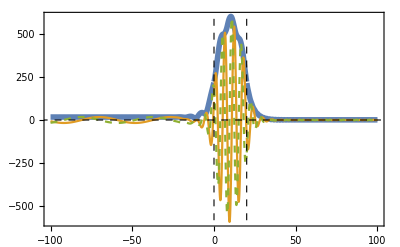

```mathematica
Plot[{Abs[ψ2[z]],Re[ψ2[z]],Im[ψ2[z]]},{z,-5tc,5tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"x","|\\phi(x)|"},Magnification->1.5],PlotStyle->{Thickness[0.01],{},Dashed},Evaluate@plotStyle]
```

Norma del estado ∫n^2|ψ|^2 ⅆx=1,  se integra entre -10tc y 10tc para realizar más rapido el calculo.
Por lo cual n=1/ √(∫| ψ |^2ⅆx)

```mathematica
Norma=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,0,tc}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {0.005, 0, 20}.

∫_0^20 (48213.8+0. ⅈ)ⅆ0.005

```mathematica
ψ2[x]
```

121.077+183.178 ⅈ

```mathematica
NormaI=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-10tc,0}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {0.005, -200, 0}.

∫_-200^0 (48213.8+0. ⅈ)ⅆ0.005

```mathematica
NormaI=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-10tc,0}]/Norma (*Propabilidad de encontrar el campo en la zona I*)
NormaII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,0,tc}]/Norma(*Propabilidad de encontrar el campo en la zona II*)
NormaIII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,tc,10tc}]/Norma(*Propabilidad de encontrar el campo en la zona III*)
```

Integrate::ilim: Invalid integration variable or limit(s) in {0.005, -200, 0}.

(∫_-200^0 (48213.8+0. ⅈ)ⅆ0.005)/(∫_0^20 (48213.8+0. ⅈ)ⅆ0.005)

Integrate::ilim: Invalid integration variable or limit(s) in {0.005, 0, 20}.

1

Integrate::ilim: Invalid integration variable or limit(s) in {0.005, 20, 200}.

(∫_20^200 (48213.8+0. ⅈ)ⅆ0.005)/(∫_0^20 (48213.8+0. ⅈ)ⅆ0.005)

```mathematica
NormaI+NormaII+NormaIII(*Propabilidad de encontrar el campo en todo el espacio es aprox 1*)
```

1+(∫_-200^0 (48213.8+0. ⅈ)ⅆ0.005)/(∫_0^20 (48213.8+0. ⅈ)ⅆ0.005)+(∫_20^200 (48213.8+0. ⅈ)ⅆ0.005)/(∫_0^20 (48213.8+0. ⅈ)ⅆ0.005)

Para este estado existe una probabilidad del 97% de encontrar el campo dentro de la cavidad y 13% de encontrarlo fuera.

```mathematica
n=1/Sqrt[Norma]
```

1/(√(∫_0^20 (48213.8+0. ⅈ)ⅆ0.005))

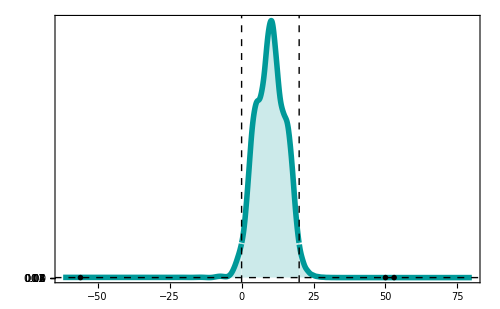

```mathematica
phi220adn005=Plot[{Abs[ψ2[z]]^2},{z,-3.1tc,4tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi_0(\\tau)|^2"},Magnification->1.8],PlotStyle->{{Thickness[0.008],color1}},Filling->Axis,Evaluate@plotStyle,FrameTicks->{{{0,0.02,0.04,0.06,0.08,0.1,0.2},None},{Automatic,None}},ImageSize->500,Epilog->{Inset[MaTeX["\\text{(h)}",Magnification->1.8],{-56,0.082}],Inset[MaTeX["\\tau_\\text{c}=20",Magnification->1.6],{53,0.075}],Inset[MaTeX["\\delta \\text{n}_{\\text{max}}=0.05",Magnification->1.6],{50,0.068}]}]
```

```mathematica
Export["phi2_tc20a_dn005.pdf",phi220adn005]
```

phi2_tc20a_dn005.pdf

```mathematica
n=1
```

1

Continuity of real (color1) , imaginary (color1) and  absolute value (green) of ψ

NIntegrate::itraw: Raw object 0.005 cannot be used as an iterator.

General::stop: Further output of NIntegrate :: itraw will be suppressed during this calculation.

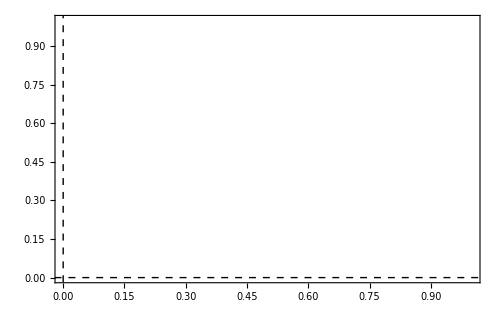

```mathematica
phi20adn005=Plot[{Abs[ψ2[z]]n,Re[ψ2[z]]n,Im[ψ2[z]]n},{z,-2tc,3tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi(\\tau)|"},Magnification->1.5],PlotStyle->{{Thickness[0.008],color1},{{},color5},{Dashed,color4}},Evaluate@plotStyle,ImageSize->500]
```

```mathematica
Export["phi_tc20_dn005.pdf",phi20adn005]
```

phi_tc20_dn005.pdf

Continuity of the absolute value of ψ (color1), ψ’(color1),ψ’’ (green), ψ’’’ (purple). As expected, only the first three are zero at the borders of the cavity

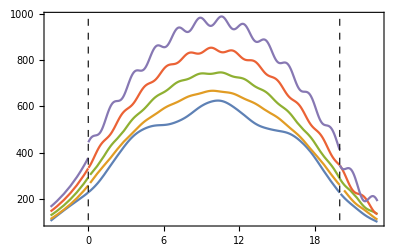

```mathematica
Plot[{Abs[ψ[z]],Abs[ψ'[z]],Abs[ψ''[z]],Abs[ψ'''[z]],Abs[ψ''''[z]]},{z,-3,tc+3},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau","Continuity"},Magnification->1.5],Evaluate@plotStyle]
```

Details of the continuity in the borders of the cavity

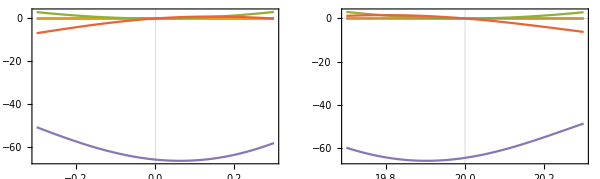

```mathematica
GraphicsRow[{
Plot[{Abs[ψ1t[z]]-Abs[ψ2t[z]],Abs[ψ1t'[z]]-Abs[ψ2t'[z]],Abs[ψ1t''[z]]-Abs[ψ2t''[z]],Abs[ψ1t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ1t''''[z]]-Abs[ψ2t''''[z]]},{z,-0.3,0.3},GridLines->{{0,tc},{}},Frame->True,Axes->False,PlotRange->All],
Plot[{Abs[ψ3t[z]]-Abs[ψ2t[z]],Abs[ψ3t'[z]]-Abs[ψ2t'[z]],Abs[ψ3t''[z]]-Abs[ψ2t''[z]],Abs[ψ3t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ3t''''[z]]-Abs[ψ2t''''[z]]},{z,tc-0.3,tc+.3},GridLines->{{0,tc},{0}},Frame->True,Axes->False,PlotRange->All]},ImageSize->600]
```

### Plot the solution ψ τ_c=20, δn=0.03,b

```mathematica
wTest=0.340478+I 3.36*10^(-6)
tc=20
```

0.340478+3.36×10^-6 ⅈ

20

Calculo de las amplitudes en la región I dadas c1=1 y c2=ρ.  (Recordar que a1=a2=0)

```mathematica
a1t=a1/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a2t=a2/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a3t=a3/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
a4t=a4/.wrulea[Re[wTest],Im[wTest]]/.ρ->rho4a[Re[wTest],Im[wTest]]
```

-0.079815-1.1135 ⅈ

-8.32667×10^-17+0. ⅈ

-292.999+338.205 ⅈ

-53.9839+94.0233 ⅈ

```mathematica
c1t=1
c2t=rho4[Re[wTest],Im[wTest]]
c3t=0
c4t=0
```

1

-210.62+88.9393 ⅈ

0

0

w11 (ω_(1u))⟶ Im<0.  a1=0. Decae en la región III. c1=01
w12 (ω_(1ur))⟶ Im<0. a2=0. Decae en la región III. c2=ρ
w13 (ω_(1ul))⟶ Im>0. a3=Free. Decae en la regiónI. c3=0
w14 (ω_(1v))⟶ Im>0. a4=Free. Decae en la regiónI. c3=0
w21 (ω_(2u))⟶  Estado confinado
w22 (ω_(2ur))⟶ Estado confinado 
w23 (ω_(2ul))⟶  Estado confinado 
w24 (ω_(2v))⟶  Estado confinado

```mathematica
{w11[Re[wTest],Im[wTest]],w12[Re[wTest],Im[wTest]],w13[Re[wTest],Im[wTest]],w14[Re[wTest],Im[wTest]]}
{w21[Re[wTest],Im[wTest]],w22[Re[wTest],Im[wTest]],w23[Re[wTest],Im[wTest]],w24[Re[wTest],Im[wTest]]}
```

{-2.33558-2.9821×10^-6 ⅈ,1.09864-0.191664 ⅈ,1.0986+0.191666 ⅈ,0.138335+1.36211×10^-6 ⅈ}

{-2.3977-2.89857×10^-6 ⅈ,1.3582-0.0000187442 ⅈ,0.902823+0.0000202969 ⅈ,0.136673+1.34585×10^-6 ⅈ}

Calculo de las amplitudes en la región I. 
Forma1:ψ_I=ψ_I
Forma 2:  ψ_I=(Jump^-1.P_L.Jump)ψ_III

```mathematica
amp1t={0a1t , 0a2t,a3t,a4t};
ψ1t[τ_]=(amp1t.solsub/.wrule[Re[wTest],Im[wTest]])
amp1t2=ijump.propaL.jump.{c1t,c2t,c3t,c4t};
ψ1t2[τ_]=Chop[amp1t2.solsub/.wrule[Re[wTest],Im[wTest]]]
```

(0.+0. ⅈ)-(53.9839-94.0233 ⅈ) ⅇ^((1.36211×10^-6-0.138335 ⅈ) τ)-(292.999-338.205 ⅈ) ⅇ^((0.191666-1.0986 ⅈ) τ)

(-0.00519343+0.0100586 ⅈ) ⅇ^((-2.9821×10^-6+2.33558 ⅈ) τ)-(45.5805-32.1556 ⅈ) ⅇ^((1.36211×10^-6-0.138335 ⅈ) τ)-(208.542-94.0529 ⅈ) ⅇ^((0.191666-1.0986 ⅈ) τ)

Calculo de las amplitudes en la región II. 
Forma1: ψ_II=(P_L.Jump)ψ_III
Forma 2: ψ_II=(Jump)ψ_I

```mathematica
amp2t=jump.{0a1t ,0a2t,a3t,a4t}//Simplify;
amp2t2=propaL.jump.{c1t, c2t,c3t,c4t};
ψ2t[τ_]=amp2t.solsup/.wrule[Re[wTest],Im[wTest]]
ψ2t2[τ_]=amp2t2.solsup/.wrule[Re[wTest],Im[wTest]]
```

(-198.555-34.119 ⅈ) ⅇ^((-0.0000187442-1.3582 ⅈ) τ)-(1.06822-0.610647 ⅈ) ⅇ^((-2.89857×10^-6+2.3977 ⅈ) τ)-(7.81388-57.7881 ⅈ) ⅇ^((1.34585×10^-6-0.136673 ⅈ) τ)-(139.546-407.949 ⅈ) ⅇ^((0.0000202969-0.902823 ⅈ) τ)

(-84.8122-58.4424 ⅈ) ⅇ^((-0.0000187442-1.3582 ⅈ) τ)-(0.631603-0.0635604 ⅈ) ⅇ^((-2.89857×10^-6+2.3977 ⅈ) τ)-(16.3807-25.2532 ⅈ) ⅇ^((1.34585×10^-6-0.136673 ⅈ) τ)-(152.303-159.344 ⅈ) ⅇ^((0.0000202969-0.902823 ⅈ) τ)

```mathematica
Abs[ψ1t[0]]
Abs[ψ2t[0]]
Abs[ψ1t2[0]]
Abs[ψ2t2[0]]
```

554.273

554.273

283.746

283.746

La funciones en la región III, estaran desfasadas debido al salto entre la región II y III en una cantidad tc. Esto se corrige con el cambio ψ_III(τ)⟶ψ_III(τ-tc) o teniendo en cuenta dicha fase.  ψ_III=(Jump^-1.P_L1.P_R.Jump)ψ_I

```mathematica
propaR1=DiagonalMatrix[{Exp[-I w1sub tc],Exp[-I w2sub tc],Exp[-I w3sub tc],Exp[-I w4sub tc]}];
propaL1=DiagonalMatrix[{Exp[I w1sub tc],Exp[I w2sub tc],Exp[I w3sub tc],Exp[I w4sub tc]}];
```

```mathematica
amp3t=Simplify[propaL1.ijump.propaR.amp2t]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t[τ_]=amp3t.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
amp3t2=Simplify[propaL1.{c1t,c2t,c3t,c4t}]/.wrule[Re[wTest],Im[wTest]]//FullSimplify;
ψ3t2[τ_]=amp3t2.solsub/.wrule[Re[wTest],Im[wTest]]//FullSimplify
```

(13623.5-15541.1 ⅈ) ⅇ^((-0.191664-1.09864 ⅈ) τ)-(1.93446-0.0345187 ⅈ) ⅇ^((-2.9821×10^-6+2.33558 ⅈ) τ)+(0.54656-0.473138 ⅈ) ⅇ^((1.36211×10^-6-0.138335 ⅈ) τ)+(0.000194594-0.0000878529 ⅈ) ⅇ^((0.191666-1.0986 ⅈ) τ)

(9656.87-4287.45 ⅈ) ⅇ^((-0.191664-1.09864 ⅈ) τ)-(0.916226+0.40081 ⅈ) ⅇ^((-2.9821×10^-6+2.33558 ⅈ) τ)

```mathematica
Abs[ψ2t[tc]]
Abs[ψ2t2[tc]]
Abs[ψ3t[tc]]
Abs[ψ3t2[tc]]
```

446.068

227.708

446.068

227.708

```mathematica
ψ[τ_]:=Piecewise[{{ψ3t[τ],τ≥tc},{ψ2t[τ],0<τ<tc},{ψ1t[τ],τ≤0}}]
ψ2[τ_]:=Piecewise[{{ψ3t2[τ],τ≥tc},{ψ2t2[τ],0<τ<tc},{ψ1t2[τ],τ≤0}}]
```

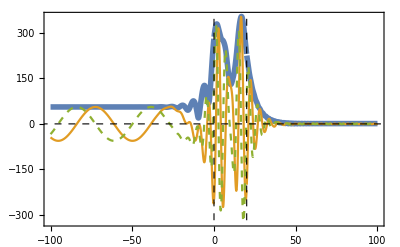

```mathematica
Plot[{Abs[ψ2[z]],Re[ψ2[z]],Im[ψ2[z]]},{z,-5tc,5tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"x","|\\phi(x)|"},Magnification->1.5],PlotStyle->{Thickness[0.01],{},Dashed},Evaluate@plotStyle]
```

Norma del estado ∫n^2|ψ|^2 ⅆx=1,  se integra entre -10tc y 10tc para realizar más rapido el calculo.
Por lo cual n=1/ √(∫| ψ |^2ⅆx)

```mathematica
Norma=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,0,tc}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {0.005, 0, 20}.

∫_0^20 (80659.3+0. ⅈ)ⅆ0.005

```mathematica
ψ2[x]
```

121.077+183.178 ⅈ

```mathematica
NormaI=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-10tc,0}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {0.005, -200, 0}.

∫_-200^0 (48213.8+0. ⅈ)ⅆ0.005

```mathematica
NormaI=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,-10tc,0}]/Norma (*Propabilidad de encontrar el campo en la zona I*)
NormaII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,0,tc}]/Norma(*Propabilidad de encontrar el campo en la zona II*)
NormaIII=Integrate[ψ2[x]*Conjugate[ψ2[x]],{x,tc,10tc}]/Norma(*Propabilidad de encontrar el campo en la zona III*)
```

Integrate::ilim: Invalid integration variable or limit(s) in {0.005, -200, 0}.

(∫_-200^0 (48213.8+0. ⅈ)ⅆ0.005)/(∫_0^20 (48213.8+0. ⅈ)ⅆ0.005)

Integrate::ilim: Invalid integration variable or limit(s) in {0.005, 0, 20}.

1

Integrate::ilim: Invalid integration variable or limit(s) in {0.005, 20, 200}.

(∫_20^200 (48213.8+0. ⅈ)ⅆ0.005)/(∫_0^20 (48213.8+0. ⅈ)ⅆ0.005)

```mathematica
NormaI+NormaII+NormaIII(*Propabilidad de encontrar el campo en todo el espacio es aprox 1*)
```

1+(∫_-200^0 (48213.8+0. ⅈ)ⅆ0.005)/(∫_0^20 (48213.8+0. ⅈ)ⅆ0.005)+(∫_20^200 (48213.8+0. ⅈ)ⅆ0.005)/(∫_0^20 (48213.8+0. ⅈ)ⅆ0.005)

Para este estado existe una probabilidad del 97% de encontrar el campo dentro de la cavidad y 13% de encontrarlo fuera.

```mathematica
n=1/Sqrt[Norma]
```

1/(√(∫_0^20 (48213.8+0. ⅈ)ⅆ0.005))

```mathematica
phi220adn005=Plot[{Abs[ψ2[z]]^2},{z,-3.1tc,4tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi_0(\\tau)|^2"},Magnification->1.8],PlotStyle->{{Thickness[0.008],color1}},Filling->Axis,Evaluate@plotStyle,FrameTicks->{{{0,0.02,0.04,0.06,0.08,0.1,0.2},None},{Automatic,None}},ImageSize->500,Epilog->{Inset[MaTeX["\\text{(h)}",Magnification->1.8],{-56,0.082}],Inset[MaTeX["\\tau_\\text{c}=20",Magnification->1.6],{53,0.075}],Inset[MaTeX["\\delta \\text{n}_{\\text{max}}=0.05",Magnification->1.6],{50,0.068}]}]
```

-Graphics-

```mathematica
Export["phi2_tc20a_dn005.pdf",phi220adn005]
```

phi2_tc20a_dn005.pdf

```mathematica
n=1
```

1

Continuity of real (color1) , imaginary (color1) and  absolute value (green) of ψ

```mathematica
phi20adn005=Plot[{Abs[ψ2[z]]n,Re[ψ2[z]]n,Im[ψ2[z]]n},{z,-2tc,3tc},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau\\text{(fs)}","|\\phi(\\tau)|"},Magnification->1.5],PlotStyle->{{Thickness[0.008],color1},{{},color5},{Dashed,color4}},Evaluate@plotStyle,ImageSize->500]
```

NIntegrate::itraw: Raw object 0.005 cannot be used as an iterator.

General::stop: Further output of NIntegrate :: itraw will be suppressed during this calculation.

-Graphics-

```mathematica
Export["phi_tc20_dn005.pdf",phi20adn005]
```

phi_tc20_dn005.pdf

Continuity of the absolute value of ψ (color1), ψ’(color1),ψ’’ (green), ψ’’’ (purple). As expected, only the first three are zero at the borders of the cavity

```mathematica
Plot[{Abs[ψ[z]],Abs[ψ'[z]],Abs[ψ''[z]],Abs[ψ'''[z]],Abs[ψ''''[z]]},{z,-3,tc+3},GridLines->{{0,tc},{0}},Axes->False,PlotRange->All,FrameLabel->MaTeX[{"\\tau","Continuity"},Magnification->1.5],Evaluate@plotStyle]
```

-Graphics-

Details of the continuity in the borders of the cavity

```mathematica
GraphicsRow[{
Plot[{Abs[ψ1t[z]]-Abs[ψ2t[z]],Abs[ψ1t'[z]]-Abs[ψ2t'[z]],Abs[ψ1t''[z]]-Abs[ψ2t''[z]],Abs[ψ1t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ1t''''[z]]-Abs[ψ2t''''[z]]},{z,-0.3,0.3},GridLines->{{0,tc},{}},Frame->True,Axes->False,PlotRange->All],
Plot[{Abs[ψ3t[z]]-Abs[ψ2t[z]],Abs[ψ3t'[z]]-Abs[ψ2t'[z]],Abs[ψ3t''[z]]-Abs[ψ2t''[z]],Abs[ψ3t'''[z]]-Abs[ψ2t'''[z]],Abs[ψ3t''''[z]]-Abs[ψ2t''''[z]]},{z,tc-0.3,tc+.3},GridLines->{{0,tc},{0}},Frame->True,Axes->False,PlotRange->All]},ImageSize->600]
```

-Graphics-

## Reflexion and Transimission

```mathematica
ClearAll
```

ClearAll

```mathematica
m=1;h=1; V0=1; k=2;
```

```mathematica
sigma=-0.092;
```

```mathematica
wf=sigma/2
```

-0.046

```mathematica
Wpv[ωIN,0]
```

1.78979

```mathematica
Rw[x_]:=(Gamma[-I wf x] Gamma[I wf x+sigma+1]Gamma[I  wf x-sigma])/(Gamma[I wf x] Gamma[sigma+1] Gamma[-sigma])
```

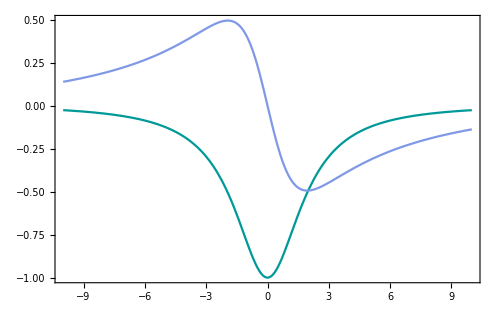

```mathematica
Plot[{Re[Rw[t]],Im[Rw[t]]},{t,-10,10},Evaluate@plotStyle,PlotStyle->{{color1},{color2}},FrameLabel->MaTeX[{"\\text{w'tc}","\\text{Rw}"},Magnification->m],ImageSize->500,PlotRange->All]
```

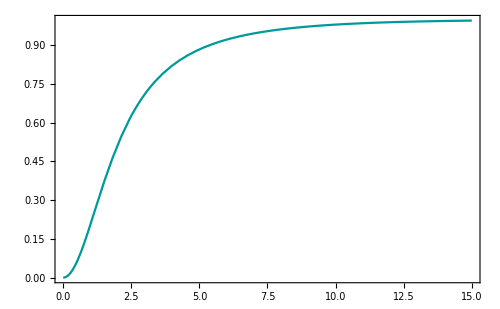

```mathematica
Plot[{1-Abs[Rw[t]]^2},{t,0,15},Evaluate@plotStyle,PlotStyle->{{color1},{color2}},FrameLabel->MaTeX[{"\\text{tc}","\\text{Rw}"},Magnification->m],ImageSize->500,PlotRange->All]
```

```mathematica
beta2=2/(Ω0 SOL);
V=(2δn)/ng0 whor[0];
wp=V/2;
```

```mathematica
whor[0]
```

1.135

```mathematica
Tc[t_]:=(4wp(V-wp))/(4wp(V-wp)+V^2Sinh[2/(u beta2)(wp-V)t]^2)
```

```mathematica
Solve[Tc[t]==0.01,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-14.1648},{t→14.1648}}

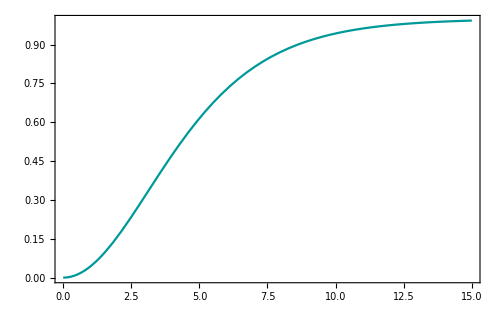

```mathematica
Plot[{1-Tc[t]},{t,0,15},Evaluate@plotStyle,PlotStyle->{{color1},{color2}},FrameLabel->MaTeX[{"\\text{tc}","\\text{R}"},Magnification->m],ImageSize->500,PlotRange->All]
```

```mathematica
(*En un ciclo Energia almacenada en un ciclo/ Potencia en un ciclo, a esa frecuencia.*)
```

```mathematica
Q=1/Tc[20]
```

1172.26

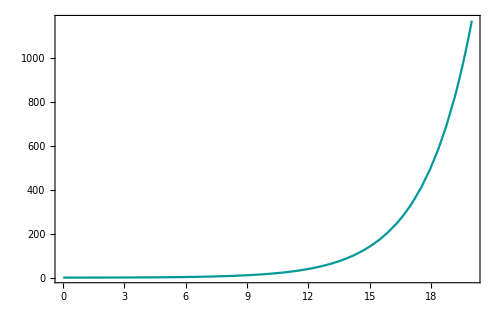

```mathematica
Plot[{1/Tc[t]},{t,0,20},Evaluate@plotStyle,PlotStyle->{{color1},{color2}},FrameLabel->MaTeX[{"\\text{tc}","\\text{Q}"},Magnification->m],ImageSize->500,PlotRange->All]
```

```mathematica
Tc[20]
```

0.000853056

```mathematica
1-Tc[20]
```

0.999147